# Research Notebook

## Created by Vasil Saroka on 20 of January 2019

in Mathematica 10.4.1 for Microsoft Windows (64-bit) (April 11, 2016)

```mathematica
"Last modified on "<>DateString[FileDate[NotebookFileName[],"Modification"]]//Style[#,FontSize->22]&
"Today is "<>DateString[Today]//Style[#,FontSize->22]&
```

Last modified on Sun 17 Nov 2019 01:04:50

Today is Mon 18 Nov 2019

```mathematica
Needs["MaTeX`"]
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor}","\\definecolor{darkgreen}{rgb}{0,0.5,0}"}];
Needs["CustomTicks`"]

(* parent directory for the manuscript code and data files *)
parentDir=Nest[DirectoryName,NotebookDirectory[],2];
```

## Functions

### Analysing first principle programmes data in Mathematica

#### Quantum Espresso Output to Mathematica data

```mathematica
(* 2019/03/22: Note that for compatibility of the output with some plotting functions the number of bands must be even. *)
```

```mathematica
Clear[QE1DBands2Mathematica];
QE1DBands2Mathematica[path_,bandsfname_,scffname_]:=Module[
{
bdata,
scfdata,
list1,
list2,
pairlist,
fun,
ef (* eV *)
},
(* 02/02/2019: adjusted to PWSCF v.6.3 output *)
bdata=ReadList[FileNameJoin[{path,bandsfname}],Word,RecordLists->True];
scfdata=ReadList[FileNameJoin[{path,scffname}],Word,RecordLists->True];

list1=Position[bdata,{"k","=",__,"(ev):"}]//Flatten;
list2=Position[bdata,{"occupation","numbers"}]//Flatten;

If[
list2==={},
pairlist=Partition[list1,2,1],
pairlist=MapThread[{#1,#2}&,{list1,list2}];
];

fun=Append[ToExpression[Flatten[bdata⟦(#⟦1⟧+1);;(#⟦2⟧-1)⟧]],(√(*Print[counter++];Print[StringQ[bdata⟦#⟦1⟧,3⟧]];*)Total[ToExpression[bdata⟦#⟦1⟧,{3,4,5}⟧]^2])]&;
ef=ToExpression[Cases[scfdata,{"the","Fermi","energy", "is",__}]⟦1,-2⟧];
{(fun/@pairlist)ᵀ,ef}
](* end Module *)
```

### Preparing input data for quantum chemistry programmes in Mathematica

#### XYZ-file generation+X passivation, carbon (silicon etc.) skeleton extraction

Functions:(UnitCell2XYxyz, XYxyz2UnitCell)

```mathematica
Clear[UnitCell2XYxyz];
UnitCell2XYxyz[unitcell_,translationvector_,XXbondlength_,XYbondlength_,Xlabel_,Ylabel_,path_,fname_]:=Module[
{
δ=0.3,
dir={1,0,0},
numberofdigits=6,
rt,
rm,unitcellnew,T,
adjacentunitcell,
hydrogenatomspos={},
nnatoms,v,vec,
coordinates,
vert,
firstline,body,text,str,

nd,ps,
},

(* subfunctions *)
ps= Row[#,"\t"]&;(* parts separation function *)
(* nd=PaddedForm[Chop@#,{9,6},ExponentFunction->(If[-6<#<6,Null,#]&)]&; (* number display function *) *)
nd=PaddedForm[#,{9,6}]&; (* number display function *)


(* Rotation to make "dir"-direction the translation one *)
rt=Cross[translationvector,dir];
If[
	rt.rt==0,
	unitcellnew=unitcell;
	T=translationvector,
	rm=RotationMatrix[{translationvector,dir}];
	unitcellnew=(rm.#)&/@unitcell;
	T=rm.translationvector
](* end If *);


adjacentunitcell=Flatten[Table[(#+i T)&/@unitcellnew,{i,-1,1}],1];
Do[
nnatoms={};
Do[v=unitcellnew⟦i⟧-adjacentunitcell⟦j⟧;If[Abs[√(v.v)-XXbondlength]<δ,AppendTo[nnatoms,adjacentunitcell⟦j⟧]];If[Length@nnatoms>2,Break[]],{j,1,Length@adjacentunitcell}];

Switch[Length@nnatoms,2,vec=-(nnatoms⟦1⟧-unitcellnew⟦i⟧+nnatoms⟦2⟧-unitcellnew⟦i⟧);AppendTo[hydrogenatomspos,unitcellnew⟦i⟧+vec/(√(vec.vec)) XYbondlength](* AppendTo *),1,vec=-(nnatoms⟦1⟧-unitcellnew⟦i⟧);AppendTo[hydrogenatomspos,unitcellnew⟦i⟧+(vec/(√(vec.vec)) XYbondlength). RotationMatrix[π/3,{0,0,1}]];AppendTo[hydrogenatomspos,unitcellnew⟦i⟧+(vec/(√(vec.vec)) XYbondlength). RotationMatrix[-π/3,{0,0,1}]]],
{i,1,Length@unitcellnew}];

(* Export to text file *)
(* coo file creation *)
vert=Flatten[{ConstantArray[Xlabel,Length@unitcellnew],ConstantArray[Ylabel,Length@hydrogenatomspos]},1];
coordinates=Flatten[{unitcellnew,hydrogenatomspos},1];

firstline=ToString[Length[unitcellnew]+Length[hydrogenatomspos]];

body=ps/@Table[{vert⟦i⟧,nd@coordinates⟦i,1⟧,nd@coordinates⟦i,2⟧,nd@coordinates⟦i,3⟧},{i,1,Length@coordinates}];

text=Flatten@{firstline,body};
str=OpenWrite[FileNameJoin[{path,fname<>".xyz"}],FormatType-> OutputForm,CharacterEncoding->"ASCII"];
Do[Write[str,text⟦i⟧],{i,1,Length@text}];
Close[str];

Chop@T

](* end Module *);

Clear[XYxyz2UnitCell];
XYxyz2UnitCell[path_,fname_,ftype_,Xlabel_]:=Module[
{
data,unitcell
},
data=ReadList[FileNameJoin[{path,fname~~ftype}],Word,RecordLists->True];
data=Drop[data,2];
unitcell={};
If[#⟦1⟧===Xlabel,AppendTo[unitcell,Read[StringToStream[#],Real]&/@Drop[#,1]];#,#]&/@data;
unitcell
];
```

### Fitting first principle data with the tight-binding (TB) model in Mathematica

#### TB model parameterization to QE DFT: FitTBParametersToQEDataVersion5, with Fitting_Log file for tracking its performance (03/03/2019)

test 26/02/2019 showed that compilation is not efficient for Eigenvalues function

FitTBParametersToQEDataVersion5 (23/03/2019)

```mathematica
(* 03/04/2019 I have added the exeptions for the bands2fitspec argument. Sometimes the number of dft bands is less than the number of bands to fit specified in this argument. In this case the updated funciton simply takes all the dft bands and proceed with evaluation. 
However, if the number of bands in thus taken dft data is less then the number of bands or any band number specified in the second element of the bands2fitspec argument the exeption is thrown. *)
(* 22/03/2019 Unlike in the version 4 of this function, in version 5 I use Plotbandx2Mathematica instead of QE1DBands2Mathematica20190310. This
allows supplying of refined DFT data to the optimization function. Refined data means that some bands that are not present in TB model are excluded
thereby increasing propability of find good TB parameters by excluding superfluous data that cannot be fitted by default. *)
(* 13/03/2019 To make evaluation faster I should add option of switching of the step monitor, so that only final results is written into the log file *)
(* 12/03/2019 The problem of Complex eigenvalues is resolved by updating the minimized function. In particular now it has the following form (x-Re(z))^2+Im(z)^2, where x stands for the DFT results
 and z is the TB model which may results in the complex eigenvalues for some sets of the TB parameters. The presented functions favors both the reduction of the imaginary part and the deviation of the real part
  from the DFT model *)
(* 11/03/2019 I have added Option to switch minimization procedure between NMinimize and FindMinimum functions. The latter allows one to look for a local minimum and has a larger number of available methods. *)
(* 09/03/2019 I want to create a log file to track performance of the NMinimize function. This can be done with the StepMonitor option. I will also add path2write variable. *)
(* 07/03/2019 Tutorials say that FindMinimum function can be compiled via something like Compilation->True option *)
(* 03/03/2019 *)
(* this funciton is under development
using step monitor option you can write the current values of the parameter with the current date and time into the log file so that data are not lost and can be retrieved even if evaluation has been aborted
Note: FitTBParametersToQEData verstion 2 does not seem to be faster than its verstion 1, this neeeds to be properly tested.
  *)
(* 20/12/2018 *)
(* The problem of complex eigenvalues for generalized eigenproblem of Hermitian matrices is resolved for this function. *)

(* 15/12/2018 *)
(* selection of krange, where fitting is curried out, can be useful in some applications, therefore FitTBParametersToQEData function is updated to version 1 called FitTBParametersToQEDataVersion1. New variable with the following structure: kpointinterval={kmin,kmax}, is added. *)

(* This function is similar to the function TBParametrization that was written for Siesta output data. Unlike TBParametrization that is based on SiestaOut2DataAndEFw, TBParametrizationWithQE uses QE1DBands2Mathematica function. *)
ClearAll[FitTBParametersToQEDataVersion5];
Unprotect[MinimizationFunction];
ClearAll[MinimizationFunction];
Protect[MinimizationFunction];
Unprotect[GoFast];
ClearAll[GoFast];
Protect[GoFast];
FitTBParametersToQEDataVersion5[path2data_?StringQ,plotbandxfname_,bandsxfname_,scffname_,path2write_?StringQ,kpointinterval_,system_,parflag_,bands2fitspec_,
OptionsPattern[{MinimizationFunction->NMinimize,WorkingPrecision->4,MaxIterations->100,Method->Automatic,GoFast->True}]]:=Catch[Module[
{
dftdata,bslen,bs,ef,
nf,n0,n1,n2,δ1,δ2,
data,kmin,kmax,

k,numberofkpoints,
len,par1,par2,x,

β,parQ,
fvQ,parflagQ,
fun2minimize,
mindata,

stepcount,logstream,text,
numberoffittedparameters,

numberofbands,
bands2show,
numberofbands2fit,

previousparvalues,
pr,

currentminvalue,
previousminvalue,

standarddeviation,


outputfname,

(* subfunctions *)
nd
},
(* Error Messages *)
FitTBParametersToQEDataVersion5::parflagstructure="The first `1` and the second `2` part of parflag argument must have the same lengths.";
FitTBParametersToQEDataVersion5::parflagelements="The argument `1` must consist of flags 'x' or numbers only, where flags stand for parameters to be found for the best fit of TBmodel to given data.";
FitTBParametersToQEDataVersion5::ElectronicBandsHSE1DOptimized="The encountered tight-binding parameters result in the complex eigenvalues for generalized eigenproblem.";
FitTBParametersToQEDataVersion5::numofbandsspec="The number of bands in DFT data is less than the specified number of bands in the first element of bands2fitspec argument or one of the band numbers given in the second element of the bands2fitspec exceeds the number of bands specified in the first element of the bands2fitspec";

(* subfuncitons *)
(*
precision=Cases[{nminimizeoptions},HoldPattern[WorkingPrecision->_]];
pr=Floor@If[precision==={},$MachinePrecision,precision⟦1,2⟧];
*)

pr=Floor@OptionValue[FitTBParametersToQEDataVersion5,WorkingPrecision];
nd=PaddedForm[1.0 #,{pr+2,pr},ExponentFunction->(If[-16<#<16,Null,#]&)]&; (* number display function *)

fvQ=(#==="x"||NumericQ@#)&; (* flag-value test. "x" = flag; numeric = "parameter value" *)
parflagQ=And@@Map[fvQ,Flatten[#]]&;

If[
	!parflagQ@parflag,
	Throw[Message[FitTBParametersToQEDataVersion5::parflagelements,parflag]]
];
len=If[
		Length[parflag⟦1⟧]==Length[parflag⟦2⟧]≤Length[system⟦3⟧],
		Length[parflag⟦1⟧],
		Throw[Message[FitTBParametersToQEDataVersion5::parflagstructure,parflag⟦1⟧,parflag⟦2⟧]]
];
(* fittedbandsspecification = {range of bands around the Fermi level, numbers of bands to be fitted} *)
(* kpointinterval = {kmin, kmax} *)

(* DFT section *)
dftdata=Plotbandx2Mathematica[path2data,plotbandxfname,bandsxfname,scffname];
bs=dftdata⟦1⟧;(* band structure *)

(* 15/12/2018: selection of the band structure data that fall into interval of k points as specified by input variable kpointinterval *)
kmin=kpointinterval⟦1⟧;
kmax=kpointinterval⟦2⟧;
bs=Select[bsᵀ,kmin≤Last[#]≤kmax&]ᵀ;
(*-------------------------------------------------------------------------------------------------------------------------*)


(* 03/03/2019: performance optimization -----------------------------------------------------------------------------------*)
numberofbands=bands2fitspec⟦1⟧;
(*-------------------------------------------------------------------------------------------------------------------------*)

ef=dftdata⟦2⟧; (* fermi energy level *)
nf=Nearest[First/@Most@bs-> Automatic];(* nearest function *)
n0=nf[ef]⟦1⟧;(* the nearest (to fermi energy) level *)
δ1=bs⟦n0,1⟧-ef;
δ2=bs⟦n0+1,1⟧-ef;
If[
	δ1 δ2<0,
	n1=n0-numberofbands/2+1;
	n2=n0+numberofbands/2,
	n1=n0-numberofbands/2;
	n2=n0+numberofbands/2-1
];
(* Note: I have checked that in Plotbandx2Mathematica function bands are sorted in the accending order. See section "Plotbandx2Mathematica function test" *)
bslen=Length[bs]-1;
If[
	n2≤bslen,
	(* n bands which are the nearest to the fermi energy level *)
	data=(#-ef)&/@bs⟦n1;;n2⟧,
	data=(#-ef)&/@bs⟦n1;;bslen⟧;
	numberofbands=Length[data]
](* end If *);

(* system = {unitcell,translationvectors,nnlengthlist} *)

(* parameters = {hoppingintegrals, overlappingintegrals, β, edge corrections} *)
(* 
   parflag={list,list,number} 
list={n,n,...n}, n = "x" or number
 *)
{par1,par2}=Reap[parflag/.{"x",a_,b_}:> (x=Unique["x"];Sow@{x,a,b};x)];(* end Reap *)
par1⟦2,1⟧=1+par1⟦2,1⟧;(* Correction in order to make overlapping matrix S at least IdentityMatrix *)
numberoffittedparameters=Length[par2⟦1,;;,1⟧]; (* number of fitted parameters *)
(* var = k *)
(* for QE K_POINTS I use tpiba_b mode *)

k=(2 π system⟦2⟧ #)/(system⟦2⟧.system⟦2⟧)&/@ Last@bs;
numberofkpoints=Length[k];

parQ=And@@Map[NumericQ,Flatten[#]]&;

(* 03/03/2019: performance optimization ----------------*) 
bands2show=bands2fitspec⟦2⟧;
numberofbands2fit=Length[bands2show];
If[numberofbands2fit>numberofbands||!And@@((#≤numberofbands)&/@bands2show),Throw[Message[FitTBParametersToQEDataVersion5::numofbandsspec]]];
data=data⟦bands2show⟧;
(*------------------------------------------------------*)



fun2minimize[dftbands2fit_,systemgeometricalparameters_,tbparameters_?parQ,kpoints_,rangeoftbbands_,selectedtbbands_]:=Block[
{
tbfittedbands
},
tbfittedbands=ElectronicBandsHSE1DOptimized[
{systemgeometricalparameters⟦1⟧,systemgeometricalparameters⟦1⟧},
{{systemgeometricalparameters⟦2⟧},{systemgeometricalparameters⟦2⟧}},
tbparameters⟦1⟧,
tbparameters⟦2⟧,
systemgeometricalparameters⟦3⟧,
tbparameters⟦3⟧,
kpoints,
tbparameters⟦4⟧,
rangeoftbbands,
selectedtbbands];

Total[(dftbands2fit-Re[tbfittedbands])^2+Im[tbfittedbands]^2,2]
](* end Block *);

(*------------------------------------- Log file header ----------------------------------*)
(* open stream for the log file *)
logstream=OpenWrite[FileNameJoin[{path2write,"Fitting_Log_"<>DateString[{"Year","Month","Day","_time_","Hour","_","Minute","_","Second"}]<>".txt"}],FormatType-> OutputForm,CharacterEncoding->"ASCII"];

Write[logstream,"# Created by Vasil Saroka \n# Wolfram Mathematica "<>$Version];
Write[logstream,"# FitTBParametersToQEDataVersion5 started on "<>DateString[]];

text=Flatten@{
"\n# Hopping integrals, eV",
Table["t"<>ToString[i-1]<>" = "<>ToString[par1⟦1,i⟧],{i,Length[par1⟦1⟧]}],
"\n# Overlapping integrals",
Table["s"<>ToString[i-1]<>" = "<>ToString[par1⟦2,i⟧],{i,Length[par1⟦2⟧]}],
"\n# Strain exponent","beta = "<>ToString[par1⟦3⟧],
"\n# Edge corrections to the hopping integrals, eV",
Table["dt"<>ToString[i-1]<>"_"<>ToString[j]<>" = "<>ToString[par1⟦4,i,j⟧],{i,Length[par1⟦4⟧]},{j,2}],"\n"};
Scan[Write[logstream,#]&,text];

Write[logstream,"# Initial ranges for fitted parameters"];
Write[logstream,StringPadRight["parameter",19],"\t",StringPadLeft["min value",19],"\t",StringPadLeft["max value",19]];
text=Row[{StringPadRight[ToString[#⟦1⟧],19],StringPadLeft[ToString@nd[#⟦2⟧],19],StringPadLeft[ToString@nd[#⟦3⟧],19]},"\t"]&/@(par2⟦1⟧);
Scan[Write[logstream,#]&,text];

Write[logstream,"\n# Minimization function options"];
Scan[Write[logstream,StringPadRight[ToString[#⟦1⟧],30],"\t",StringPadLeft[ToString[#⟦2⟧],30]]&,{
MinimizationFunction->OptionValue[FitTBParametersToQEDataVersion5,MinimizationFunction],
WorkingPrecision->OptionValue[FitTBParametersToQEDataVersion5,WorkingPrecision],
Method->OptionValue[FitTBParametersToQEDataVersion5,Method],
MaxIterations->OptionValue[FitTBParametersToQEDataVersion5,MaxIterations]}];

text=Flatten@{"\n# Range of bands around the Fermi level: E_f-n/2 to Ef+n/2:",numberofbands,"\n#Which of "<>ToString[numberofbands]<>" selected bands shall be fitted to ab initio data?",
bands2show};
Scan[Write[logstream,#]&,text];

Write[logstream,"\n# Ab initio data to fit"];
(* k values *)
Scan[Write[logstream,#]&,Flatten@{"k values, tpiba_b",Row[nd/@#,"\t"]&/@k}];
(* energies *)
text=Flatten@{Table[{"band "<>ToString[bands2show⟦i⟧]<>", eV",nd/@(data⟦i⟧)},{i,Length[bands2show]}]};
Scan[Write[logstream,#]&,text];

(* system under consideration *)
Write[logstream,"\n# System under consideration"];
(* unit cell *)
Scan[Write[logstream,#]&,Flatten@{"unit cell atoms (x, y, z), Angstrom",Row[nd/@#,"\t"]&/@(system⟦1⟧)}];
(* translation vector *)
text=Flatten@{"\ntranslation vector (x, y, z), Angstrom",Row[nd/@(system⟦2⟧),"\t"]};
Scan[Write[logstream,#]&,text];
(* distances to the n-th order nearest-neighbors *)
text=Flatten@{"\ndistances to the n-th order nearest-neighbors, Angstrom",Table[Row[{ToString[i-1]<>" order :",nd[system⟦3,i⟧]},"\t"],{i,Length[system⟦3⟧]}]};
Scan[Write[logstream,#]&,text];

(*------------------------------------- Log file header end ----------------------------------*)


(*------------------------------------ Minimization procedure --------------------------------*)
stepcount=0;
previousparvalues=#⟦2⟧&/@(par2⟦1⟧);
previousminvalue=0;

If[OptionValue[GoFast],
mindata=Apply[OptionValue[MinimizationFunction],{fun2minimize[data,system,par1,k,numberofbands,bands2show],par2⟦1⟧,
	WorkingPrecision->OptionValue[WorkingPrecision],
	Method->OptionValue[Method],
	MaxIterations->OptionValue[MaxIterations]}
]
,
mindata=Apply[OptionValue[MinimizationFunction],{fun2minimize[data,system,par1,k,numberofbands,bands2show],par2⟦1⟧,
	StepMonitor:>(stepcount++;
		Write[logstream,"\nstep "<>ToString[stepcount]<>" "<>DateString[]];
		Write[logstream,"fitted parameters"];
		Do[Write[logstream,nd[par2⟦1,i,1⟧]],{i,numberoffittedparameters}](* end Do *);
		Write[logstream,"deviations from the previous step"];
		Do[Write[logstream,nd[par2⟦1,i,1⟧-previousparvalues⟦i⟧]],{i,numberoffittedparameters}](* end Do *);
		previousparvalues=par2⟦1,;;,1⟧;
		Write[logstream,"minimum value"];
		currentminvalue=fun2minimize[data,system,par1,k,numberofbands,bands2show];
		Write[logstream,nd@currentminvalue];
		Write[logstream,"deviation from the previous step"];
		Write[logstream,nd[currentminvalue-previousminvalue]];
		previousminvalue=currentminvalue;
	),
	WorkingPrecision->OptionValue[WorkingPrecision],
	Method->OptionValue[Method],
	MaxIterations->OptionValue[MaxIterations]}
]
](* end If *);
standarddeviation=√(mindata⟦1⟧/(numberofkpoints numberofbands2fit));
Write[logstream,"\n#The result of minimization"];
Write[logstream,"Stantard deviation"];
Write[logstream,nd[standarddeviation]];

par1=par1/.mindata⟦2⟧;
text=Flatten@{
"\n# Hopping integrals, eV",
Table["t"<>ToString[i-1]<>" = "<>ToString[nd[par1⟦1,i⟧]],{i,Length[par1⟦1⟧]}],
"\n# Overlapping integrals",
Table["s"<>ToString[i-1]<>" = "<>ToString[nd[par1⟦2,i⟧]],{i,Length[par1⟦2⟧]}],
"\n# Strain exponent","beta = "<>ToString[nd[par1⟦3⟧]],
"\n# Edge corrections to the hopping integrals, eV",
Table["dt"<>ToString[i-1]<>"_"<>ToString[j]<>" = "<>ToString[nd[par1⟦4,i,j⟧]],{i,Length[par1⟦4⟧]},{j,2}],"\n"};
Scan[Write[logstream,#]&,text];

Write[logstream,"\n#FitTBParametersToQEDataVersion5 finished fitting on "<>DateString[]];
Close[logstream];
(*--------------------------------- Minimization procedure end ------------------------------*)

(*-------------------------------------------------------------------------------------------*)
mindata={standarddeviation,par1};
Remove@@{"par1*","par2*","x*"};(* delete these symbols forever *)
mindata
](* end Module *)](* end Catch *);
```

(10/03/2019) HSE1DOptimized is a HUSE1DOptimized function but with electric field being removed because it is superfluous in optimization of the TB parameters.

```mathematica
(* 10/03/2019 we remove E field from HUSE1DOptimized function. *)
Clear[HSE1DOptimized];
HSE1DOptimized[unitcell_,translationvectors_,hoppingintegrals_,overlappingintegrals_,nnlengthlist_,β_,k_,edgecorrections_]:=Block[
{
Tvec,len,hlen,aplen,
adjacentunitcells,
coordinationnumberslist,
aplist,counter,v,
bondvector,bondlength,phase,
straining,hij,sij,ε,
h,s,δ=0.1,
lim,r1,r2
},
(* first argument structure: unitcell={idealunitcell,optimizedunitcell};
   second argument structure: translationvectors={idealtranslationvectors,optimizedtranslationvectors} *)
Tvec=translationvectors;
len=Dimensions[unitcell]⟦2⟧;
hlen=Length[hoppingintegrals];

adjacentunitcells=Table[
Table[(#1+i Tvec⟦o,1⟧&)/@(unitcell⟦o⟧),{i,-1,1}],
{o,1,2}](* end Table *);


(* Coordination numbers list generation *)
aplist=Flatten[adjacentunitcells⟦1⟧,1];(* atom positions list *)
aplen=Length@aplist;
coordinationnumberslist=Table[
counter=0;
Do[
	v=unitcell⟦1,i⟧-aplist⟦j⟧;
	If[Abs[√(v.v)-nnlengthlist⟦2⟧]<δ,counter++],
	{j,1,aplen}
];(* end Do *)
counter,
{i,1,len}];(* end Table *)

h=ConstantArray[0,{len,len}];
s=ConstantArray[0,{len,len}];


Do[
	hij=0;
	sij=0;
	Do[
		bondvector=unitcell⟦1,i⟧-adjacentunitcells⟦1,c,j⟧;
		bondlength=√(bondvector.bondvector);
	
		Do[
			If[
				Abs[nnlengthlist⟦l⟧-bondlength]<δ,
				bondvector=unitcell⟦2,i⟧-adjacentunitcells⟦2,c,j⟧;
				bondlength=√(bondvector.bondvector);
				straining=If[l==1,1,Exp[β (nnlengthlist⟦l⟧-bondlength)/nnlengthlist⟦l⟧]];
				phase=Cos[k.bondvector]+ⅈ Sin[k.bondvector];
				ε=Switch[coordinationnumberslist⟦i⟧,1,edgecorrections⟦l,1⟧,2,edgecorrections⟦l,2⟧,3,0];

				hij=hij+straining (hoppingintegrals⟦l⟧+ε) phase;
				sij=sij+straining overlappingintegrals⟦l⟧ phase;
				Break[];
			](* end If *),
		{l,1,hlen}
		](* end Do *)
		,
		{c,1,3}
	](* end Do *);
	h⟦i,j⟧=If[i==j,1/2 hij,hij];
	s⟦i,j⟧=If[i==j,1/2 sij,sij];,
{i,1,len},
{j,i,len}
](* end Do *);
{h+ConjugateTranspose@h,s+ConjugateTranspose@s}
](* end Module *);
```

(10/03/2019) ElectronicBandsHSE1DOptimized with HSE1DOptimized

```mathematica
Clear[ElectronicBandsHSE1DOptimized];
ElectronicBandsHSE1DOptimized[unitcell_,translationvectors_,hoppingintegrals_,overlappingintegrals_,nnlengthlist_,β_,klist_,edgecorrections_,numberofbands_,bands2show_]:=
Module[
{(*--------------------------- Variables and constants ---------------------------*)
len,
bands,m,
k,range
},
(*--------------------------- Body of the fucntion ---------------------------------*)
len=Dimensions[unitcell]⟦2⟧;

m=HSE1DOptimized[unitcell,translationvectors,hoppingintegrals,overlappingintegrals,nnlengthlist,β,k,edgecorrections];
bands=ParallelTable[
				Sort@Chop[Eigenvalues[m/.k-> klist⟦i⟧]],
				{i,1,Length[klist]}
](* end ParallelTable *);

If[
	numberofbands≤len,
		   range=Table[(len-numberofbands)/2+bands2show⟦i⟧,{i,Length[bands2show]}];
	Transpose[bands]⟦range⟧,
	Transpose[bands]
](* end If *)
](* end Module *);
```

#### Read bands after bands.x re-ordering and processing by plotband.x (21/03/2019)

Function Bandsx2Mathematica

```mathematica
Clear[Bandsx2Mathematica];
Bandsx2Mathematica[path_,bandsxfname_,scffname_]:=Module[
{
bdata,
scfdata,
nbnd,
ef (* eV *)
},
bdata=ReadList[FileNameJoin[{path,bandsxfname}],Word,RecordLists->True];
scfdata=ReadList[FileNameJoin[{path,scffname}],Word,RecordLists->True];

nbnd=ToExpression[StringReplace[bdata⟦1,3⟧,","->""]];

bdata=Partition[Flatten[bdata⟦2;;All⟧],nbnd+3];

ef=ToExpression[Cases[scfdata,{"the","Fermi","energy", "is",__}]⟦1,-2⟧];
{Append[Transpose[ToExpression[Drop[#,3]&/@bdata]],√Total[ToExpression[#⟦1;;3⟧]^2]&/@bdata],ef}
](* end Module *)
```

Bandsx2Mathematica function test

```mathematica
d⟦1⟧//Dimensions
```

{49,31}

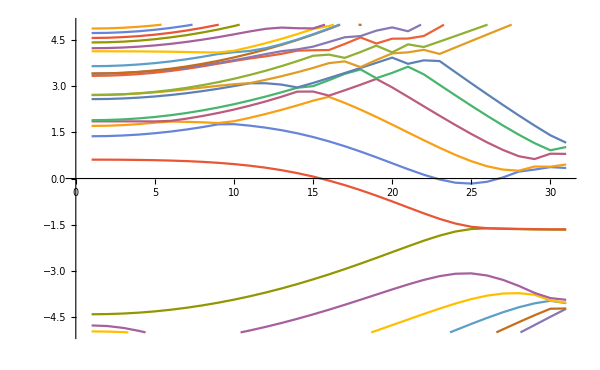

```mathematica
path="D:\\Dropbox\\Linux_NTNU\\QE_docs\\GNRs\\ZGNR_6\\";
fname1="ZGNR6_bands.dat";
fname2="scf.out";
d=Bandsx2Mathematica[path,fname1,fname2];

lim=5;
ListLinePlot[d⟦1,1;;48⟧,PlotRange->{-lim,lim},ImageSize->600]
```

```mathematica
(* as follows from the picture the re-ordering of the bands did not happen. Perhaps the spacing between the k poins is too large to do such a reodering based on the wave fucntion overlapping. *)
```

```mathematica
path="D:\\Dropbox\\Linux_NTNU\\QE_docs\\GNRs\\ZGNR_6\\";
fname1="ZGNR6_bands.dat";
fname2="scf.out";
d=Bandsx2Mathematica[path,fname1,fname2];
d⟦2⟧

lim=6;

fig=CompareElectronicBands1D[{d⟦1⟧,bdata},{"\\text{ZGNR"<>ToString@w<>"}",{"k","E-E_{F},\\text{ eV}"},{"\\text{DFT:QE sorted}","\\text{TB:Partoens2006}"}},{{0,π},{-lim,lim}},{Directive[Red],Directive[Blue]},{2 π,√(T.T)},{d⟦2⟧,FermiEnergyAndBandGap[bdata]⟦1⟧},1,ImageSize->{Automatic,380}]
```

-1.6219

-Graphics-

Bandsx output file analysis

```mathematica
path="D:\\Dropbox\\Linux_NTNU\\QE_docs\\GNRs\\ZGNR_6\\";
fname="ZGNR6_bands.dat";
data=ReadList[FileNameJoin[{path,fname}],Word,RecordLists->True];

data⟦1;;4⟧

data⟦1,3⟧

nbnd=ToExpression[StringReplace[data⟦1,3⟧,","->""]]
%//NumberQ

data⟦1,5⟧
nks=ToExpression[StringReplace[data⟦1,5⟧,","->""]]
%//NumberQ

Flatten[data⟦2;;All⟧]⟦1;;3⟧
Flatten[data⟦2;;All⟧]⟦4;;53⟧
Flatten[data⟦2;;All⟧]//Length
%/nks

data=Partition[Flatten[data⟦2;;All⟧],nbnd+3];

kdata=√Total[ToExpression[#⟦1;;3⟧]^2]&/@data;
edata=Transpose[ToExpression[Drop[#,3]&/@data]];

AppendTo[edata,kdata];

edata//Dimensions
```

{{&plot,nbnd=,48,,nks=,31,/},{0.000000,0.000000,0.000000},{-20.986,-20.533,-19.823,-18.865,-17.697,-16.467,-14.169,-12.601,-10.808,-9.045},{-8.997,-8.532,-7.853,-7.737,-7.420,-7.322,-6.783,-6.696,-6.022,-5.927}}

48,

48

True

31

31

True

{0.000000,0.000000,0.000000}

{-20.986,-20.533,-19.823,-18.865,-17.697,-16.467,-14.169,-12.601,-10.808,-9.045,-8.997,-8.532,-7.853,-7.737,-7.420,-7.322,-6.783,-6.696,-6.022,-5.927,-5.504,-5.282,-4.968,-4.774,-4.411,0.614,1.374,1.710,1.857,1.896,2.580,2.711,2.717,3.336,3.407,3.414,3.650,4.135,4.234,4.422,4.568,4.727,4.874,5.210,5.515,5.788,6.013,6.073,0.016667,0.000000}

1581

51

{49,31}

```mathematica
path="D:\\Dropbox\\Linux_NTNU\\QE_docs\\GNRs\\ZGNR_6\\";
fname1="bands.out";
fname2="scf.out";
d=QE1DBands2Mathematica[path,fname1,fname2];

lim=6;

fig=CompareElectronicBands1D[{edata,bdata},{"\\text{ZGNR"<>ToString@w<>"}",{"k","E-E_{F},\\text{ eV}"},{"\\text{DFT:QE sorted}","\\text{TB:Partoens2006}"}},{{0,π},{-lim,lim}},{Directive[Red],Directive[Blue]},{2 π,√(T.T)},{d⟦2⟧,FermiEnergyAndBandGap[bdata]⟦1⟧},1,ImageSize->{Automatic,380}]
```

-Graphics-

Function Plotbandx2Mathematica

```mathematica
Clear[Plotbandx2Mathematica];
Plotbandx2Mathematica[path_,plotbandXoutputfname_,bandsXfname_,scffname_]:=Module[
{
bandsx,
nks,
scfdata,
ef (* eV *),
plotbandx,

fun

},
bandsx=ReadList[FileNameJoin[{path,bandsXfname}],Word,RecordLists->True];
nks=ToExpression[StringReplace[bandsx⟦1,5⟧,","->""]];
scfdata=ReadList[FileNameJoin[{path,scffname}],Word,RecordLists->True];
ef=ToExpression[Cases[scfdata,{"the","Fermi","energy", "is",__}]⟦1,-2⟧];

plotbandx=ReadList[FileNameJoin[{path,plotbandXoutputfname}],Word,RecordLists->True];
fun=Function[{x},Sort[x,#1⟦1⟧<#2⟦1⟧&]];
plotbandx=Map[fun,Partition[ToExpression[plotbandx],nks]];
plotbandx=If[Length[plotbandx]//OddQ,Most@plotbandx,plotbandx](* end If *);

(* 22/03/2019: I sorted eigenvalues for each value of k in accending order from the top to the bottom of the matrix. 
This is done to ensure compartibility with TB data in fitting TB parameters to the given DFT results.
It may be that the energy levels are already sorted in this way in the plotband output. At least they are sorted like this right after band structure calculation carried out by pw.x
{Append[Transpose[Sort/@Transpose[plotbandx⟦;;,;;,2⟧]],plotbandx⟦1,;;,1⟧],ef}
Note: indeed they are sorted like this therefore correction is not needed.
*)
{Append[plotbandx⟦;;,;;,2⟧,plotbandx⟦1,;;,1⟧],ef}
](* end Module *)
```

Plotbandx2Mathematica function test

```mathematica
d⟦1⟧//Length
```

15

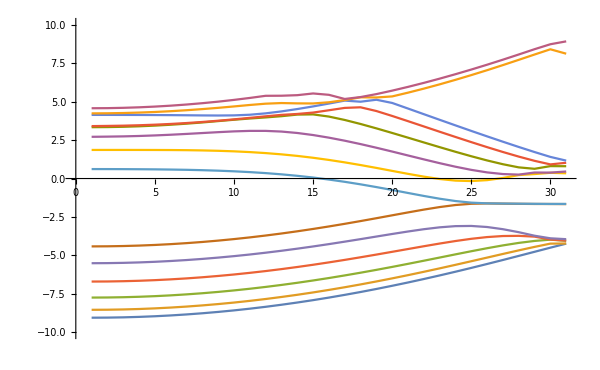

```mathematica
path="D:\\Dropbox\\Linux_NTNU\\QE_docs\\GNRs\\ZGNR_6\\";
fname1="ZGNR6_bands_2d.dat.1.2";
fname2="ZGNR6_bands.dat";
fname3="scf.out";
d=Plotbandx2Mathematica[path,fname1,fname2,fname3];

lim=10;
ListLinePlot[d⟦1,1;;14⟧,PlotRange->{-lim,lim},ImageSize->600]
```

```mathematica
Transpose[d⟦1⟧]
```

{{-9.045,-8.532,-7.737,-6.696,-5.504,-4.411,0.614,1.857,2.711,3.336,3.407,4.135,4.234,4.568,0.},{-9.039,-8.526,-7.731,-6.691,-5.498,-4.405,0.613,1.858,2.723,3.343,3.419,4.135,4.24,4.574,0.0167},{-9.022,-8.509,-7.714,-6.673,-5.481,-4.387,0.61,1.858,2.739,3.362,3.435,4.133,4.257,4.595,0.0333},{-8.992,-8.48,-7.685,-6.645,-5.452,-4.358,0.604,1.857,2.765,3.394,3.462,4.131,4.286,4.628,0.05},{-8.951,-8.439,-7.645,-6.605,-5.412,-4.317,0.596,1.855,2.801,3.439,3.499,4.126,4.325,4.675,0.0667},{-8.898,-8.386,-7.593,-6.553,-5.36,-4.264,0.583,1.851,2.846,3.496,3.547,4.12,4.376,4.735,0.0833},{-8.833,-8.322,-7.529,-6.491,-5.298,-4.199,0.566,1.842,2.899,3.565,3.606,4.111,4.439,4.809,0.1},{-8.757,-8.246,-7.455,-6.417,-5.224,-4.123,0.542,1.826,2.956,3.644,3.676,4.101,4.512,4.896,0.1167},{-8.669,-8.159,-7.369,-6.332,-5.139,-4.035,0.51,1.802,3.013,3.732,3.756,4.095,4.594,4.996,0.1333},{-8.57,-8.061,-7.272,-6.237,-5.044,-3.936,0.469,1.767,3.064,3.82,3.845,4.104,4.685,5.11,0.15},{-8.459,-7.951,-7.164,-6.13,-4.938,-3.826,0.417,1.718,3.096,3.901,3.942,4.146,4.78,5.237,0.1667},{-8.337,-7.83,-7.045,-6.014,-4.821,-3.705,0.352,1.653,3.096,3.971,4.043,4.235,4.864,5.376,0.1833},{-8.203,-7.698,-6.916,-5.887,-4.695,-3.573,0.272,1.571,3.052,4.051,4.137,4.362,4.905,5.381,0.2},{-8.059,-7.556,-6.776,-5.75,-4.559,-3.43,0.176,1.47,2.96,4.155,4.196,4.515,4.884,5.417,0.2167},{-7.904,-7.403,-6.626,-5.605,-4.415,-3.277,0.064,1.349,2.826,4.168,4.286,4.686,4.878,5.528,0.2333},{-7.738,-7.239,-6.467,-5.45,-4.263,-3.115,-0.067,1.208,2.656,4.026,4.437,4.872,4.955,5.44,0.25},{-7.561,-7.066,-6.298,-5.288,-4.103,-2.944,-0.214,1.05,2.458,3.806,4.59,5.064,5.098,5.17,0.2667},{-7.375,-6.883,-6.121,-5.118,-3.939,-2.765,-0.378,0.876,2.238,3.545,4.629,4.992,5.279,5.294,0.2833},{-7.178,-6.69,-5.936,-4.943,-3.771,-2.58,-0.556,0.69,2.001,3.26,4.387,5.12,5.267,5.486,0.3},{-6.971,-6.489,-5.744,-4.763,-3.604,-2.391,-0.744,0.496,1.753,2.961,4.066,4.911,5.336,5.712,0.3167},{-6.756,-6.28,-5.545,-4.582,-3.443,-2.203,-0.939,0.304,1.498,2.655,3.728,4.548,5.58,5.956,0.3333},{-6.531,-6.062,-5.342,-4.401,-3.294,-2.02,-1.132,0.123,1.245,2.346,3.385,4.182,5.842,6.216,0.35},{-6.298,-5.839,-5.136,-4.226,-3.172,-1.855,-1.312,-0.031,0.998,2.039,3.041,3.817,6.12,6.491,0.3667},{-6.057,-5.609,-4.929,-4.062,-3.094,-1.722,-1.463,-0.136,0.767,1.738,2.701,3.454,6.414,6.78,0.3833},{-5.809,-5.375,-4.725,-3.918,-3.082,-1.641,-1.568,-0.165,0.563,1.448,2.366,3.094,6.721,7.082,0.4},{-5.554,-5.139,-4.529,-3.805,-3.151,-1.62,-1.614,-0.105,0.398,1.175,2.039,2.74,7.04,7.397,0.4167},{-5.294,-4.902,-4.346,-3.737,-3.293,-1.634,-1.626,0.035,0.291,0.929,1.724,2.392,7.372,7.724,0.4333},{-5.029,-4.669,-4.184,-3.725,-3.488,-1.645,-1.636,0.225,0.254,0.725,1.425,2.051,7.713,8.061,0.45},{-4.762,-4.443,-4.056,-3.776,-3.717,-1.654,-1.644,0.291,0.39,0.632,1.15,1.721,8.059,8.405,0.4667},{-4.494,-4.231,-3.973,-3.965,-3.885,-1.656,-1.652,0.371,0.384,0.806,0.918,1.405,8.399,8.727,0.4833},{-4.232,-4.223,-3.942,-4.033,-4.049,-1.662,-1.65,0.342,0.456,0.8,1.023,1.163,8.113,8.914,0.5}}

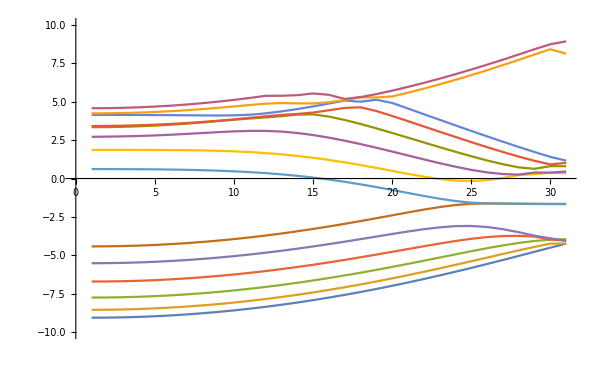

```mathematica
path="D:\\Dropbox\\Linux_NTNU\\QE_docs\\GNRs\\ZGNR_6\\";
fname1="ZGNR6_bands_2d.dat.1.2";
fname2="ZGNR6_bands.dat";
fname3="scf.out";
d=Plotbandx2Mathematica[path,fname1,fname2,fname3];

lim=10;
ListLinePlot[d⟦1,1;;14⟧,PlotRange->{-lim,lim},ImageSize->600]
```

```mathematica
(* as follows from the picture the re-ordering of the bands did not happen. Perhaps the spacing between the k poins is too large to do such a reodering based on the wave fucntion overlapping. *)
```

```mathematica
path="D:\\Dropbox\\Linux_NTNU\\QE_docs\\GNRs\\ZGNR_6\\";
fname1="ZGNR6_bands_2d.dat.1.2";
fname2="ZGNR6_bands.dat";
fname3="scf.out";
d=Plotbandx2Mathematica[path,fname1,fname2,fname3];
dd=Bandsx2Mathematica[path,fname2,fname3];

d⟦1⟧//Dimensions

lim=4;

fig=CompareElectronicBands1D[{d⟦1⟧,dd⟦1⟧,bdata},{"\\text{ZGNR"<>ToString@6<>"}",{"k","E-E_{F},\\text{ eV}"},{"\\text{DFT:QE plotband.x}","\\text{DFT:QE bands.x}","\\text{TB: fit step 34}"}},{{0,π},{-lim,lim}},{Directive[Red],Directive[Dashed,Opacity[0.7],Blue],Directive[DotDashed,Darker[Green,0.5]]},{2 π,2 π,√(T.T)},{d⟦2⟧,dd⟦2⟧,FermiEnergyAndBandGap[bdata]⟦1⟧},1,ImageSize->{Automatic,380}]
```

{15,31}

-Graphics-

```mathematica
path="D:\\Dropbox\\Linux_NTNU\\QE_docs\\GNRs\\ZGNR_6\\";
fname1="ZGNR6_bands_2d.dat.1.2";
fname2="ZGNR6_bands.dat";
fname3="scf.out";
d=Plotbandx2Mathematica[path,fname1,fname2,fname3];
dd=Bandsx2Mathematica[path,fname2,fname3];

d⟦1⟧//Dimensions

lim=4;

fig=CompareElectronicBands1D[{d⟦1⟧,dd⟦1⟧,bdata},{"\\text{ZGNR"<>ToString@6<>"}",{"k","E-E_{F},\\text{ eV}"},{"\\text{DFT:QE plotband.x}","\\text{DFT:QE bands.x}","\\text{TB: fit step 34}"}},{{0,π},{-lim,lim}},{Directive[Red],Directive[Dashed,Opacity[0.7],Blue],Directive[DotDashed,Darker[Green,0.5]]},{2 π,2 π,√(T.T)},{d⟦2⟧,dd⟦2⟧,FermiEnergyAndBandGap[bdata]⟦1⟧},1,ImageSize->{Automatic,380}]
```

{15,31}

-Graphics-

plotband.x output file analysis

48

True

31

31

True

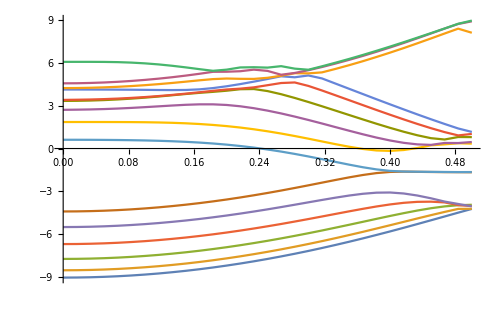

-Graphics-

{{-9.045,-9.039,-9.022,-8.992,-8.951,-8.898,-8.833,-8.757,-8.669,-8.57,-8.459,-8.337,-8.203,-8.059,-7.904,-7.738,-7.561,-7.375,-7.178,-6.971,-6.756,-6.531,-6.298,-6.057,-5.809,-5.554,-5.294,-5.029,-4.762,-4.494,-4.232},{-8.532,-8.526,-8.509,-8.48,-8.439,-8.386,-8.322,-8.246,-8.159,-8.061,-7.951,-7.83,-7.698,-7.556,-7.403,-7.239,-7.066,-6.883,-6.69,-6.489,-6.28,-6.062,-5.839,-5.609,-5.375,-5.139,-4.902,-4.669,-4.443,-4.231,-4.223},{-7.737,-7.731,-7.714,-7.685,-7.645,-7.593,-7.529,-7.455,-7.369,-7.272,-7.164,-7.045,-6.916,-6.776,-6.626,-6.467,-6.298,-6.121,-5.936,-5.744,-5.545,-5.342,-5.136,-4.929,-4.725,-4.529,-4.346,-4.184,-4.056,-3.973,-3.942},{-6.696,-6.691,-6.673,-6.645,-6.605,-6.553,-6.491,-6.417,-6.332,-6.237,-6.13,-6.014,-5.887,-5.75,-5.605,-5.45,-5.288,-5.118,-4.943,-4.763,-4.582,-4.401,-4.226,-4.062,-3.918,-3.805,-3.737,-3.725,-3.776,-3.965,-4.033},{-5.504,-5.498,-5.481,-5.452,-5.412,-5.36,-5.298,-5.224,-5.139,-5.044,-4.938,-4.821,-4.695,-4.559,-4.415,-4.263,-4.103,-3.939,-3.771,-3.604,-3.443,-3.294,-3.172,-3.094,-3.082,-3.151,-3.293,-3.488,-3.717,-3.885,-4.049},{-4.411,-4.405,-4.387,-4.358,-4.317,-4.264,-4.199,-4.123,-4.035,-3.936,-3.826,-3.705,-3.573,-3.43,-3.277,-3.115,-2.944,-2.765,-2.58,-2.391,-2.203,-2.02,-1.855,-1.722,-1.641,-1.62,-1.634,-1.645,-1.654,-1.656,-1.662},{0.614,0.613,0.61,0.604,0.596,0.583,0.566,0.542,0.51,0.469,0.417,0.352,0.272,0.176,0.064,-0.067,-0.214,-0.378,-0.556,-0.744,-0.939,-1.132,-1.312,-1.463,-1.568,-1.614,-1.626,-1.636,-1.644,-1.652,-1.65},{1.857,1.858,1.858,1.857,1.855,1.851,1.842,1.826,1.802,1.767,1.718,1.653,1.571,1.47,1.349,1.208,1.05,0.876,0.69,0.496,0.304,0.123,-0.031,-0.136,-0.165,-0.105,0.035,0.225,0.291,0.371,0.342},{2.711,2.723,2.739,2.765,2.801,2.846,2.899,2.956,3.013,3.064,3.096,3.096,3.052,2.96,2.826,2.656,2.458,2.238,2.001,1.753,1.498,1.245,0.998,0.767,0.563,0.398,0.291,0.254,0.39,0.384,0.456},{3.336,3.343,3.362,3.394,3.439,3.496,3.565,3.644,3.732,3.82,3.901,3.971,4.051,4.155,4.168,4.026,3.806,3.545,3.26,2.961,2.655,2.346,2.039,1.738,1.448,1.175,0.929,0.725,0.632,0.806,0.8},{3.407,3.419,3.435,3.462,3.499,3.547,3.606,3.676,3.756,3.845,3.942,4.043,4.137,4.196,4.286,4.437,4.59,4.629,4.387,4.066,3.728,3.385,3.041,2.701,2.366,2.039,1.724,1.425,1.15,0.918,1.023},{4.135,4.135,4.133,4.131,4.126,4.12,4.111,4.101,4.095,4.104,4.146,4.235,4.362,4.515,4.686,4.872,5.064,4.992,5.12,4.911,4.548,4.182,3.817,3.454,3.094,2.74,2.392,2.051,1.721,1.405,1.163},{4.234,4.24,4.257,4.286,4.325,4.376,4.439,4.512,4.594,4.685,4.78,4.864,4.905,4.884,4.878,4.955,5.098,5.279,5.267,5.336,5.58,5.842,6.12,6.414,6.721,7.04,7.372,7.713,8.059,8.399,8.113},{4.568,4.574,4.595,4.628,4.675,4.735,4.809,4.896,4.996,5.11,5.237,5.376,5.381,5.417,5.528,5.44,5.17,5.294,5.486,5.712,5.956,6.216,6.491,6.78,7.082,7.397,7.724,8.061,8.405,8.727,8.914},{6.073,6.074,6.074,6.069,6.054,6.021,5.968,5.894,5.799,5.686,5.562,5.446,5.527,5.682,5.697,5.67,5.772,5.598,5.521,5.762,6.015,6.28,6.558,6.846,7.144,7.451,7.767,8.087,8.411,8.743,8.965},{0.,0.0167,0.0333,0.05,0.0667,0.0833,0.1,0.1167,0.1333,0.15,0.1667,0.1833,0.2,0.2167,0.2333,0.25,0.2667,0.2833,0.3,0.3167,0.3333,0.35,0.3667,0.3833,0.4,0.4167,0.4333,0.45,0.4667,0.4833,0.5}}

{0.,0.0167,0.0333,0.05,0.0667,0.0833,0.1,0.1167,0.1333,0.15,0.1667,0.1833,0.2,0.2167,0.2333,0.25,0.2667,0.2833,0.3,0.3167,0.3333,0.35,0.3667,0.3833,0.4,0.4167,0.4333,0.45,0.4667,0.4833,0.5}

{0.5,0.4833,0.4667,0.45,0.4333,0.4167,0.4,0.3833,0.3667,0.35,0.3333,0.3167,0.3,0.2833,0.2667,0.25,0.2333,0.2167,0.2,0.1833,0.1667,0.15,0.1333,0.1167,0.1,0.0833,0.0667,0.05,0.0333,0.0167,0.}

{0.,0.0167,0.0333,0.05,0.0667,0.0833,0.1,0.1167,0.1333,0.15,0.1667,0.1833,0.2,0.2167,0.2333,0.25,0.2667,0.2833,0.3,0.3167,0.3333,0.35,0.3667,0.3833,0.4,0.4167,0.4333,0.45,0.4667,0.4833,0.5}

{0.,0.0167,0.0333,0.05,0.0667,0.0833,0.1,0.1167,0.1333,0.15,0.1667,0.1833,0.2,0.2167,0.2333,0.25,0.2667,0.2833,0.3,0.3167,0.3333,0.35,0.3667,0.3833,0.4,0.4167,0.4333,0.45,0.4667,0.4833,0.5}

15

```mathematica
path="D:\\Dropbox\\Linux_NTNU\\QE_docs\\GNRs\\ZGNR_6\\";
fname="ZGNR6_bands.dat";
data=ReadList[FileNameJoin[{path,fname}],Word,RecordLists->True];

nbnd=ToExpression[StringReplace[data⟦1,3⟧,","->""]]
%//NumberQ

data⟦1,5⟧
nks=ToExpression[StringReplace[data⟦1,5⟧,","->""]]
%//NumberQ

path="D:\\Dropbox\\Linux_NTNU\\QE_docs\\GNRs\\ZGNR_6\\";
fname="ZGNR6_bands_2d.dat.1.2";
data=ReadList[FileNameJoin[{path,fname}],Word,RecordLists->True];

d=Partition[ToExpression[data],nks];
ListLinePlot[d,ImageSize->500,PlotRangePadding->{Scaled[.1],Scaled[.1]}]

fun=Function[{x},Sort[x,#1⟦1⟧<#2⟦1⟧&]];
dd=Map[fun,d];

ListLinePlot[dd,ImageSize->500,PlotRangePadding->{Scaled[.1],Scaled[.1]}]

res=Append[dd⟦;;,;;,2⟧,dd⟦1,;;,1⟧]

d⟦;;,;;,2⟧;
d⟦1,;;,1⟧
d⟦2,;;,1⟧

dd⟦1,;;,1⟧
dd⟦2,;;,1⟧


465/nks
```

#### Analysing Fitting_Log file (16/03/2019)

Function TBfitLog2Mathematica

```mathematica
ClearAll[TBfitLog2Mathematica];
TBfitLog2Mathematica[path2read_,fname_]:=Block[{data,hind,oind,sind,eind},
data=ReadList[FileNameJoin[{path2read,fname}],Word,RecordLists->True];
hind=Position[data,{"#","Hopping","integrals,","eV"}]⟦2,1⟧;
oind=Position[data,{"#","Overlapping","integrals"}]⟦2,1⟧;
sind=Position[data,{"#","Strain","exponent"}]⟦2,1⟧;
eind=Position[data,{"#","Edge","corrections","to","the","hopping","integrals,","eV"}]⟦2,1⟧;

{ToExpression/@(data⟦hind+1;;oind-1,3⟧),ToExpression/@(data⟦oind+1;;sind-1,3⟧),ToExpression[data⟦sind+1,3⟧],Partition[ToExpression/@(data⟦eind+1;;-2,3⟧),2]}

](* end Block *)
```

```mathematica
path="D:\\Google Drive\\Data Part2\\Work\\Scientific Data\\2018\\Hidden correlation\\ZGNR6\\";
fname="Fitting_Log_20190312_time_03_40_31.txt";
data=ReadList[FileNameJoin[{path,fname}],Word,RecordLists->True];
hind=Position[data,{"#","Hopping","integrals,","eV"}]⟦2,1⟧
oind=Position[data,{"#","Overlapping","integrals"}]⟦2,1⟧
sind=Position[data,{"#","Strain","exponent"}]⟦2,1⟧
eind=Position[data,{"#","Edge","corrections","to","the","hopping","integrals,","eV"}]⟦2,1⟧

{ToExpression/@(data⟦hind+1;;oind-1,3⟧),ToExpression/@(data⟦oind+1;;sind-1,3⟧),ToExpression[data⟦sind+1,3⟧],Partition[ToExpression/@(data⟦eind+1;;-2,3⟧),2]}
```

1498

1503

1508

1510

{{0.,2.45545,0.,0.0397012},{1.,0.0129494,0.,0.},0.,{{0.,0.},{0.,0.},{0.,0.},{0.,0.}}}

TBfitLog2Mathematica function test

```mathematica
path="D:\\Google Drive\\Data Part2\\Work\\Scientific Data\\2018\\Hidden correlation\\ZGNR6\\";
fname="Fitting_Log_20190312_time_03_29_38.txt";
tbparameters=TBfitLog2Mathematica[path,fname]
```

{{0.,2.45545,0.,0.0397012},{1.,0.0129494,0.,0.},0.,{{0.,0.},{0.,0.},{0.,0.},{0.,0.}}}

Function MinFunctionFromTBfitLog (19/03/2019)

```mathematica
ClearAll[MinFunctionFromTBfitLog];
Protect[MethodUsed];
MinFucntionFromTBfitLog[path2read_,fname_,OptionsPattern[{MethodUsed->True}]]:=Module[
{
data
},

data=ReadList[FileNameJoin[{path2read,fname}],Word,RecordLists->True];
If[
OptionValue[MethodUsed],
{ToExpression[data⟦Flatten[Position[data,{"minimum","value"}]]+1,1⟧],data⟦Position[data,{"Method",_}]⟦1,1⟧,2⟧},
{ToExpression[data⟦Flatten[Position[data,{"minimum","value"}]]+1,1⟧]}
](* end If *)
](* end Module *);
```

MinFunctionFromTBfitLog function test (19/03/2019)

```mathematica
(* initial test *)
```

```mathematica
path2read="D:\\OneDrive - NTNU\\Mathematica Files\\P_2019_01_20_Hidden_correlation_with_DFT\\ZGNR_6\\";
SetDirectory[path2read];
flist=FileNames["Fitting*"];
Grid[Table[{i,flist⟦i⟧},{i,Length[flist]}],Frame->All,Background->{None,{{LightBlue,White}}}]
fname=flist⟦3⟧

data=ReadList[FileNameJoin[{path2read,fname}],Word,RecordLists->True];

d=ToExpression[data⟦Flatten[Position[data,{"minimum","value"}]]+1,1⟧];
```

1 | Fitting_Log_20190312_time_20_10_12.txt
2 | Fitting_Log_20190318_time_16_05_05.txt
3 | Fitting_Log_20190319_time_11_06_39.txt
4 | Fitting_Log_20190319_time_18_00_38.txt
5 | Fitting_Log_20190319_time_18_05_27.txt
6 | Fitting_Log_20190319_time_18_11_00.txt
7 | Fitting_Log_20190319_time_18_30_37.txt

Fitting_Log_20190319_time_11_06_39.txt

```mathematica
path2read="D:\\OneDrive - NTNU\\Mathematica Files\\P_2019_01_20_Hidden_correlation_with_DFT\\ZGNR_6\\";
SetDirectory[path2read];
flist=FileNames["Fitting*"];
Grid[Table[{i,flist⟦i⟧},{i,Length[flist]}],Frame->All,Background->{None,{{LightBlue,White}}}]
fname=flist⟦2⟧
```

1 | Fitting_Log_20190312_time_20_10_12.txt
2 | Fitting_Log_20190318_time_16_05_05.txt
3 | Fitting_Log_20190319_time_11_06_39.txt
4 | Fitting_Log_20190319_time_18_00_38.txt
5 | Fitting_Log_20190319_time_18_05_27.txt
6 | Fitting_Log_20190319_time_18_11_00.txt
7 | Fitting_Log_20190319_time_18_30_37.txt

Fitting_Log_20190318_time_16_05_05.txt

```mathematica
d=MinFucntionFromTBfitLog[path2read,flist⟦1⟧]
```

{{513.6733495614553,376.7080161684475,376.7080161684475,376.7080161684475,173.5857547795912,124.8467237393674,124.8467237393674,116.4422178912654,116.4422178912654,116.4422178912654,116.4422178912654,116.4422178912654,116.4422178912654,116.4422178912654,116.4422178912654,116.4422178912654,116.4422178912654,116.4422178912654,116.4422178912654,116.4422178912654,116.4422178912654,103.2526661193949,103.2526661193949,103.2526661193949,103.2526661193949,83.0499,83.0499,83.0499,54.9375,54.9375,54.9375,34.4276,34.4276,34.4276,34.4276,33.4351,33.4351,33.4351,33.4351,33.4351,33.4351,33.4351,33.4351,33.4351,33.4351,33.4351,33.4351,33.4351,33.4351,33.4351,33.4351,33.4351,33.4351,33.4351,32.2316,32.2316,32.2316,32.2316,32.2316,32.2316,32.2316,32.2316,32.2316,32.2316,32.2316,32.2316,32.2316,32.2316,32.2316,32.2316,32.2316,31.6447,31.6447,31.6447,31.6447,31.6447,31.6447,31.6447,31.6447,31.6447,31.6447,28.8359,28.8359,28.8359,28.8359,28.8359,28.8359,28.8359,28.8359,28.8359,28.8359,28.8359,28.8359,28.8359,28.8359,28.8359,28.8359,28.8359,28.8359,28.8359,28.8359,28.8359,28.8359,28.8359,28.8359,28.8359,28.8359,28.8359,28.8359,28.8359,28.8359,28.8359,28.6094,28.6094,28.6094,28.6094,28.6094,28.6094,28.6094,28.6094,28.6094,28.6094,28.6094,28.6094,28.6094,28.6094,28.6094,28.6094,28.6094,28.6094,28.6094,28.5953,28.5953,28.5953,28.5953,28.5953,28.5953,28.5953,28.5953,28.5953,28.5953,28.5953,28.5953,28.5953,28.5953,28.5953,28.5953,28.5953,28.5953,28.5953,28.1645,28.1645,27.4238,27.4238,27.4021,27.4021,27.4021,27.4021,27.4021,25.9662,25.9662,25.9662,25.9662,25.9662,25.9662,25.9662,25.9662,25.9662,25.9662,25.9662,25.9662,24.9608},DifferentialEvolution}

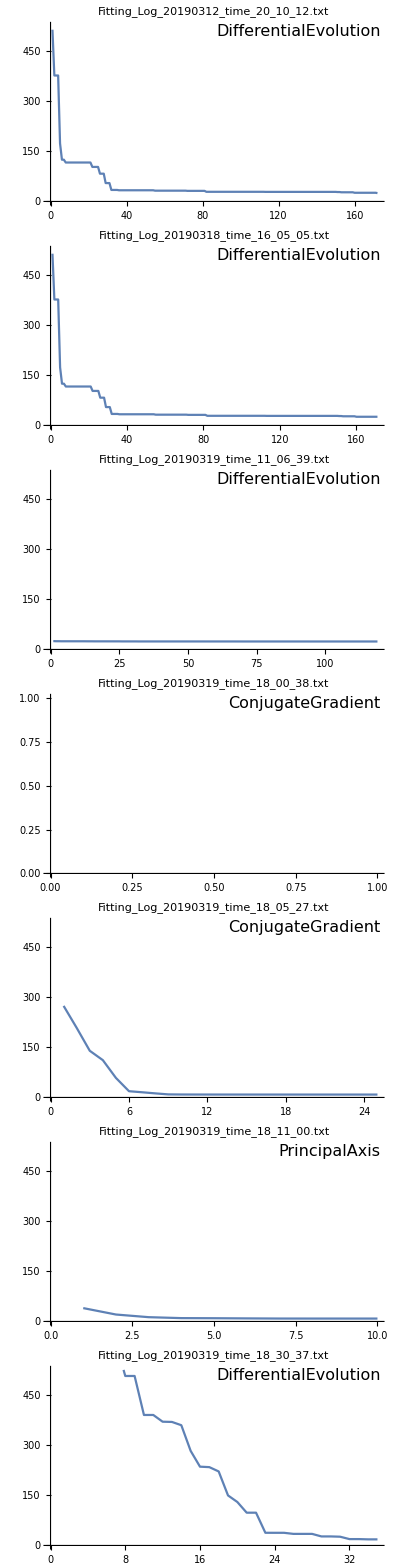

```mathematica
imagesize=400;
Column[
Table[
d=MinFucntionFromTBfitLog[path2read,flist⟦i⟧];
ListLinePlot[d⟦1⟧,PlotRange->{0,525},PlotLabel->Style[flist⟦i⟧,16],PlotLegends->Placed[Style[d⟦2⟧,16],{Right,Top}],ImageSize->imagesize],{i,Length[flist]}]]
```

Function StepParametersFromTBfitLog  (19/03/2019)

```mathematica
Clear[StepParametersFromTBfitLog];
StepParametersFromTBfitLog[path2read_,fname_,stepnumber_]:=Catch[Module[
{
data,
hind,oind,
sind,eind,
rind,mind,
symbols,len,
steppos,stepTBpar,
parsub
},
(* error messages *)
StepParametersFromTBfitLog::stepnumber="The step number `1` is not found in the specified Log file";
(*--------------------------------------------------------------------------------------*)

data=ReadList[FileNameJoin[{path2read,fname}],Word,RecordLists->True];

hind=Position[data,{"#","Hopping","integrals,","eV"}]⟦1,1⟧;
oind=Position[data,{"#","Overlapping","integrals"}]⟦1,1⟧;
sind=Position[data,{"#","Strain","exponent"}]⟦1,1⟧;
eind=Position[data,{"#","Edge","corrections","to","the","hopping","integrals,","eV"}]⟦1,1⟧;
rind=Position[data,{"#","Initial","ranges","for","fitted","parameters"}]⟦1,1⟧;
mind=Position[data,{"#","Minimization","function","options"}]⟦1,1⟧;

symbols=data⟦rind+2;;mind-1,1⟧;

len=Length[symbols];

steppos=Position[data,{"step",ToString[stepnumber],__}];
If[
	steppos==={},
	Throw[Message[StepParametersFromTBfitLog::stepnumber,stepnumber]],
	steppos=steppos⟦1,1⟧
];
stepTBpar=Flatten[data⟦steppos+2;;steppos+1+len⟧];
parsub=MapThread[#1->#2&,{symbols,stepTBpar}];

ToExpression[{(data⟦hind+1;;oind-1,3⟧),(data⟦oind+1;;sind-1,3⟧),data⟦sind+1,3⟧,Partition[(data⟦eind+1;;rind-1,3⟧),2]}/.parsub]
](* end Module *)](* end Catch *)
```

StepParametersFromTBfitLog function test (19/03/2019)

```mathematica
path2read="D:\\OneDrive - NTNU\\Mathematica Files\\P_2019_01_20_Hidden_correlation_with_DFT\\ZGNR_6\\";
SetDirectory[path2read];
flist=FileNames["Fitting*"];
Grid[Table[{i,flist⟦i⟧},{i,Length[flist]}],Frame->All,Background->{None,{{LightBlue,White}}}]
fname=flist⟦3⟧

data=ReadList[FileNameJoin[{path2read,fname}],Word,RecordLists->True];
```

1 | Fitting_Log_20190312_time_20_10_12.txt
2 | Fitting_Log_20190318_time_16_05_05.txt
3 | Fitting_Log_20190319_time_11_06_39.txt
4 | Fitting_Log_20190319_time_18_00_38.txt
5 | Fitting_Log_20190319_time_18_05_27.txt
6 | Fitting_Log_20190319_time_18_11_00.txt
7 | Fitting_Log_20190319_time_18_30_37.txt

Fitting_Log_20190319_time_11_06_39.txt

```mathematica
hind=Position[data,{"#","Hopping","integrals,","eV"}]⟦1,1⟧
oind=Position[data,{"#","Overlapping","integrals"}]⟦1,1⟧
sind=Position[data,{"#","Strain","exponent"}]⟦1,1⟧
eind=Position[data,{"#","Edge","corrections","to","the","hopping","integrals,","eV"}]⟦1,1⟧
rind=Position[data,{"#","Initial","ranges","for","fitted","parameters"}]⟦1,1⟧
mind=Position[data,{"#","Minimization","function","options"}]⟦1,1⟧

symbols=data⟦rind+2;;mind-1,1⟧

len=Length[symbols]

stepnumber=2;

smarks=Position[data,{"step",ToString[stepnumber],__}]⟦1,1⟧
stepTBpar=Flatten[data⟦smarks+2;;smarks+1+len⟧]
parsub=MapThread[#1->#2&,{symbols,stepTBpar}]

{(data⟦hind+1;;oind-1,3⟧),(data⟦oind+1;;sind-1,3⟧),data⟦sind+1,3⟧,Partition[(data⟦eind+1;;rind-1,3⟧),2]}
ToExpression[{(data⟦hind+1;;oind-1,3⟧),(data⟦oind+1;;sind-1,3⟧),data⟦sind+1,3⟧,Partition[(data⟦eind+1;;rind-1,3⟧),2]}/.parsub]
%⟦1,1⟧//NumberQ
```

4

9

14

16

25

33

{x13,x14,x15,x16,x17,x18}

6

305

{6.505812434036101,0.137858543220281,-1.242497501482970,-0.006790416615056,-1.373878104687520,0.075910243504652}

{x13→6.505812434036101,x14→0.137858543220281,x15→-1.242497501482970,x16→-0.006790416615056,x17→-1.373878104687520,x18→0.075910243504652}

```mathematica
{"x23","y23"}/."x23"->"0.34"
```

{0.34,y23}

### Customized Functions

#### Save data functions

```mathematica
Clear[mySave];
SetAttributes[mySave,HoldFirst];
mySave[varlist_,path_?StringQ,fname_?StringQ]:=Module[
{
fName
},

fName=FileNameJoin[{path,fname}];
Do[
	If[
		FileExistsQ[fName],
		fName=FileNameJoin[{path,fname<>"_v_"<>ToString[i]}];,
		Break[]
	](* end If *),
{i,100}](* end Do *);
Save[fName,varlist]
](* end Module *);
```

### Tight-binding Numerical Calculation Functions

#### Atomic coordinate generators

CNT atomic structure (functions: Nanotube, BondListM, Bonds, AtomicStructure)

```mathematica
Nanotube[NumberOfWalls_,nn_,mm_]:=Catch[
Module[
{
(*-------------- functions ----------------*)
RollingUp,
CylindricalToCartesian,
qfunc,lowqfunc,upqfunc,
(*-------------- variables ----------------*)
gg,k,i,j,
m,n,
a0=1.42,
a,a1,a2,
L,r,Cc,theta,
dR,T,t1,t2,
NumberOfHexagons,
R,p,q,
lim,pqlist,
initPoint,Shiftx,
del1,del2,del3,
Coord,LineCoord,V,g,
max,u,cu,unew,dz

},
(* Initial parameters *)
k=0;

RollingUp[list_]:={list[[1]],list[[2]]/r,list[[3]]};
CylindricalToCartesian[list_]:={list[[1]]*Cos[list[[2]]],list[[1]]*Sin[list[[2]]],list[[3]]};

For[k=1,k≤NumberOfWalls,k++,
m=mm*k;
n=nn*k;
a0=1.42;
a=a0 √3;

(* Primitive vectors of graphene lattice *)
a1={0,a Cos[Pi/6],a Sin[Pi/6]};
a2={0,a Cos[Pi/6],-a Sin[Pi/6]};

(* Nanotube radius *)
L=a √(n^2+m^2+n m);
r=L/(2 Pi);

(* Chirality vector of the nanotube *)
Cc=n a1+m a2+{r,0,0};

(* Rotation of the system of the coordinates*)
theta=ArcTan[Cc[[3]]/Cc[[2]]];
a1=RotationMatrix[-theta,{1,0,0}].a1;
a2=RotationMatrix[-theta,{1,0,0}].a2;


(* Translation vector of a nanotube *)
dR=GCD[2 n+m,2 m+n];
t1=(2 m+n)/dR;
t2=-(2 n+m)/dR;
T=t1 a1+t2 a2;

NumberOfHexagons=(2 L^2)/(a^2 dR);
(* Symmetry vector of the nanotube *)
If[
	t1==0,
	p=0;
	q=-1;
	,
	lim=100;
	qfunc[p_]:=(1+p t2)/t1;
	upqfunc[p_]:=(m p)/n;
	lowqfunc[p_]:=(-NumberOfHexagons+m p)/n;
	pqlist={};
	Do[If[IntegerQ[qfunc[p]],AppendTo[pqlist,{p,qfunc[p]}]],{p,-lim,lim}];
	Do[
		If[
			(lowqfunc[pqlist⟦i,1⟧]<pqlist⟦i,2⟧<upqfunc[pqlist⟦i,1⟧]),
			p=pqlist⟦i,1⟧;	 
			q=pqlist⟦i,2⟧;
		](* end If *),
		{i,1,Length[pqlist]}
	](* end Do *)
](* end If *);
R=p a1+q a2;


(* Shift of sublattices in graphene *)
initPoint=RotationMatrix[-theta,{1,0,0}].{0,a0,0};
(* Shift from the origin of the coordinate system*)
Shiftx={r,0,0};

(* Vectors of dirrection to nearest neighbours *)
del1=a0 RotationMatrix[-theta,{1,0,0}].{0,Cos[Pi/3],Sin[Pi/3]};
del2=a0 RotationMatrix[-theta,{1,0,0}].{0,Cos[Pi/3],-Sin[Pi/3]};
del3=a0 RotationMatrix[-theta,{1,0,0}].{0,-1,0};

(* List of coordinates *)
Coord={};
(* List of bond lines *)
LineCoord={};
(* Fill lists for the first sublattice *)
For[i=1;j=0;V={0,0},i≤ NumberOfHexagons,i++,
V=i R-j T+Shiftx;

If[V[[3]]≥-T[[2]]/T[[3]] V[[2]]+(T[[2]]^2+T[[3]]^2)/T[[3]],j=j+1;V=i R-j T+Shiftx;AppendTo[Coord,V];AppendTo[LineCoord,{V,V-del1}];AppendTo[LineCoord,{V,V-del2}];AppendTo[LineCoord,{V,V-del3}],AppendTo[Coord,V];AppendTo[LineCoord,{V,V-del1}];AppendTo[LineCoord,{V,V-del2}];AppendTo[LineCoord,{V,V-del3}]
](* end If *)

];(* end For i *)
(* Fill lists for the second sublattice *)
For[i=1;j=0;V=initPoint,i≤ NumberOfHexagons,i++,
V=i R-j T+initPoint+Shiftx;
If[V[[3]]≥-T[[2]]/T[[3]] V[[2]]+(T[[2]]^2+T[[3]]^2)/T[[3]],j=j+1;V=i R-j T+initPoint+Shiftx;AppendTo[Coord,V];AppendTo[LineCoord,{V,V+del1}];AppendTo[LineCoord,{V,V+del2}];AppendTo[LineCoord,{V,V+del3}],AppendTo[Coord,V];AppendTo[LineCoord,{V,V+del1}];AppendTo[LineCoord,{V,V+del2}];AppendTo[LineCoord,{V,V+del3}]
](* end If *)

];(* end For i *)

Coord=Map[RollingUp,Coord];

Coord=Map[CylindricalToCartesian,Coord];

];(*end For k*)

If[
	mm==0,
	max = Max /@ Transpose[Coord];(* maxima of the atomic coordinates *)
	dz=0.08; (* delta step *)
	u=Select[Coord,  (#⟦3⟧≥ max⟦3⟧ - dz) &];(* selection of the edge atoms not further than dz from the "max" edge in z-direction *)
	cu=Complement[Coord,u]; (* atomic coordinates of the rest of the atoms *)
	unew=#-T&/@u; (* shift of the edge atoms onto opposite side by substracting translation vector T*)
	Coord=Join[cu,unew];
	Return[Chop@{Coord,T,a0}],
	Return[Chop@{Coord,T,a0}]
](* end If *)
](* end Module *);
](* Catch braket *)(* end Function Nanotube *)
 
(* 18/04/2019: in Mathematica 12 a new function BondList is introduced, therefore to resolve name conflict, I add letter M
 to the end of my custom function. *)
Clear[BondListM];
BondListM[sitepositions_,bondlength_,dim_]:=Module[
{
δ=0.2,
len,
vec,
bondlist={}
},
len=Length@sitepositions;
Do[
	vec=sitepositions⟦i⟧-sitepositions⟦j⟧;
	If[
		Abs[√(vec.vec)-bondlength]<δ,
		AppendTo[bondlist,Switch[
								dim,
								2,Most/@{sitepositions⟦i⟧,sitepositions⟦j⟧},
								_,{sitepositions⟦i⟧,sitepositions⟦j⟧}
							](* end Switch *)
		](* end AppendTo *)
	](* end If *),
{i,1,len-1},
{j,i+1,len}
](* end Do *);
bondlist
](* end Module *);

Bonds[sitepositions_,bondlength_,dim_,δ_]:=Module[
{
len,
vec,
bondlist={}
},
len=Length@sitepositions;
Do[
	vec=sitepositions⟦i⟧-sitepositions⟦j⟧;
	If[
		Abs[√(vec.vec)-bondlength]<δ,
		AppendTo[bondlist,Switch[
								dim,
								2,Most/@{sitepositions⟦i⟧,sitepositions⟦j⟧},
								_,{sitepositions⟦i⟧,sitepositions⟦j⟧}
							](* end Switch *)
		](* end AppendTo *)
	](* end If *),
{i,1,len-1},
{j,i+1,len}
](* end Do *);
bondlist
](* end Module *);

AtomicStructure[system_,lim_,dim_,imagesize_]:=Module[
{
u
},

u=If[
	Length@lim==2,
	Flatten[Table[(#+system⟦2⟧ i)&/@system⟦1⟧,{i,-lim⟦1⟧,lim⟦2⟧}],1],
	Flatten[Table[(#+system⟦2⟧ i)&/@system⟦1⟧,{i,-lim,lim}],1]
];
Switch[
dim,
3,
Graphics3D[{Specularity[GrayLevel[1],100],Gray,Sphere[u,0.3],Tube[BondListM[u,system⟦3⟧,3],0.1]},Boxed->False,Lighting-> "Neutral",ImageSize->imagesize],
2,
Graphics[{Gray,Disk[Most@#,0.3]&/@u,Line[BondListM[u,system⟦3⟧,2]]},ImageSize->imagesize]
]
](* end Module *);
```

GNR atomic structure (function: Nanoribbon)

```mathematica
Nanoribbon[nanoribbontype_,numberofchains_]:=Module[
{
a0=1.42(* Å *),a,
dir,p1,p2,p,
tv,unitcell,T,

a1,a2,vc,chain
},
a=√3 a0;
dir={a0 {-1/2,(√3)/2,0},a0 {1/2,(√3)/2,0}};
(* graphene primitive translations *)
a1=a {1/2,(√3)/2,0};
a2=a {1,0,0};

Switch[
		nanoribbontype,
		1,
		p1={{0,0,0},{0,0,0}+dir⟦1⟧};
		p2={{a0, 0,0},{a0,0,0}+dir⟦2⟧};
		p={p1,p2};
		tv={3 a0,0,0};
		T=a {0,1,0},
		2,
		p1={{0,0,0},{a0, 0,0}};
		p2={{0,0,0}+dir⟦1⟧,{a0,0,0}+dir⟦2⟧};
		p={p1,p2};
		tv=a {0,1,0};
		T={3 a0,0,0},
		3,
		p1={{0,0,0},{0,a0,0}};
		p2={{0,0,0}+a1,{0,a0,0}+a1};
		p={p1,p2};
		tv={0,3 a0,0};
		T=a2
](* end Switch *);
unitcell=Flatten[Table[(#+{(n-1)/2,(n-2)/2}⟦Mod[n,2,1]⟧tv)&/@p⟦Mod[n,2,1]⟧ ,{n,1,numberofchains}],1];

{unitcell,T,a0}


](* end Module *);
```

#### Electronic properties

Data calculation

Basic functions: HUBSE: H-Hamiltonian; U-electric field, B-magnetic field, S-overlapping matrix, E-Edge corrections; ElectronicBandsHUBSE, ElectronicStructureHUBSE (for velocity matrix calculation);

```mathematica
Clear[HUBSE];
HUBSE[unitcell_,translationvectors_,hoppingintegrals_,overlappingintegrals_,nnlengthlist_?(VectorQ[#,NumericQ]&),β_(* strain *),k_,Ε_(* electric field *),B_(* magnetic field *),edgecorrections_,gflag_(* gauge flag is not used any more *)]:=Catch[
Module[
{
tf1,tf2,
Tvec,len,
aunitcells,
cnlist,
aplist,counter,v,
bondvector,bondlength,φ,
straining,hij,sij,ε,
H,S,
δ=0.021(* or 0.05*),(* tolerance for the bond length deviation from ideal reference value: 
See for details `Method' section of V.A.Saroka,K.G.Batrakov,and L.A.Chernozatonskii,Phys.Solid State 56,2135 (2014).
free access link: https://drive.google.com/file/d/0B1PX-Ri2Z2h1SjM5NnZ0ZjhXNzA/view
*)
lim,r1,r2,r12,
t,δt,tE,tSO,
s,

Φ,φM,
Φ0=2.067833758 10^5(* flux quantum T Å^2*),

(* subfunctions *)
U,
conjugate,

arg1,arg2,inconsarg
},

HUBSE::arg1="The argument `1` should be a list of points in 3D space.";HUBSE::arg2="The argument `1` should be a list numeric vectors of 3D space or a list of lists of such vectors up to 3 ones.";
HUBSE::inconsarg="Arguments `1` , `2` must have the same lengths which is less than length of `3`.";

tf1=MatchQ[#1,{arg___?(VectorQ[#1,NumericQ]&&Length[#1]==3&)}]&;tf2=(MatchQ[#1,{arg___?(VectorQ[#1,NumericQ]&&Length[#1]==3&)}]&&Length[#1]≤3)&;

If[!And@@(tf1/@unitcell),Throw[Message[HUBSE::arg1,unitcell]]];
If[!And@@(tf2/@translationvectors),Throw[Message[HUBSE::arg2,translationvectors]]];
If[!(Length@hoppingintegrals==Length@overlappingintegrals≤Length@nnlengthlist),Throw[Message[HUBSE::inconsarg,hoppingintegrals,overlappingintegrals,nnlengthlist]]];

(*-------------------- subfunctions --------------------*)
(* Electrostatic potential *)
U[r_,e_]:=-r.e;  (* Homogenious electric field *)

(* complex conjugation *)
conjugate[expr_]:=expr/.Complex[x_,y_]:> x-I y;


(*------------------------------------------------------*)

(* first argument structure: unitcell={idealunitcell,optimizedunitcell};
   second argument structure: translationvectors={idealtranslationvectors,optimizedtranslationvectors} *)
Tvec=translationvectors;
len=Dimensions[unitcell]⟦2⟧;

(* Adjacent unitcells *)
aunitcells=Table[
	Switch[
	(Tvec//Dimensions)⟦2⟧,
	1,Table[(#1+i Tvec⟦o,1⟧&)/@(unitcell⟦o⟧),{i,-1,1}],
	2,Flatten[Table[(#1+i Tvec⟦o,1⟧+j Tvec⟦o,2⟧&)/@(unitcell⟦o⟧),{i,-1,1},{j,-1,1}],1],
	3,Flatten[Table[(#1+i Tvec⟦o,1⟧+j Tvec⟦o,2⟧+k Tvec⟦o,3⟧&)/@(unitcell⟦o⟧),{i,-1,1},{j,-1,1},{k,-1,1}],2]]
,{o,1,2}](* end Table *);


(* Coordination numbers list generation *)
aplist=Flatten[aunitcells⟦1⟧,1];(* atom positions list *)

cnlist=Table[
counter=0;
Do[
	v=unitcell⟦1,i⟧-aplist⟦j⟧;
	If[Abs[√(v.v)-nnlengthlist⟦2⟧]<δ,counter++],
	{j,1,Length@aplist}
];(* end Do *)
counter,
{i,1,len}];(* end Table *)

(* Hamiltonian and Overlap matrices *)
H=ConstantArray[0,{len,len}];
S=ConstantArray[0,{len,len}];

(* Hamiltonian and Overlap matrix elements filling *)
Do[
	hij=0;
	sij=0;
	(* Summation over adjecent unitcells *)
	Do[
		r1=unitcell⟦1,i⟧;
		r2=aunitcells⟦1,c,j⟧;
		r12=r1-r2; (* bondvector ideal *)
		(* Summation over nearest neighbours of various orders *)
		Do[
			If[
				Abs[nnlengthlist⟦l⟧-√(r12.r12)]<δ,
				r1=unitcell⟦2,i⟧;
				r2=aunitcells⟦2,c,j⟧;
				
				t=hoppingintegrals⟦l⟧;
				s=overlappingintegrals⟦l⟧;

				r12=r1-r2; (* bondvector real *)
				bondlength=√(r12.r12);
				ε=If[l==1,0,(bondlength-nnlengthlist⟦l⟧)/nnlengthlist⟦l⟧];
(* straining is taken into account as in the paper: Ribeiro,R.M.,Pereira,V.M.,Peres,N.M.R.,Briddon,P.R.,and Castro Neto,A.H. "Strained graphene:tight-binding and density functional calculations", New Journal of Physics,11(11),115002 (2009). http://doi.org/10.1088/1367-2630/11/11/115002 *)


				(* Generalization of the Landau gauge to the arbitrary direction of the B :
				 eq.(24) from J.-C.Charlier and S.Roche,Rev.Mod.Phys.79,677 (2007).*)
				If[B//NumberQ,
				φM=B,

				Φ=((r2+r1)⟦1⟧)/2 B⟦3⟧ (r2-r1)⟦2⟧+(((r2+r1)⟦2⟧)/2  B⟦1⟧-((r2+r1)⟦1⟧)/2  B⟦2⟧) (r2-r1)⟦3⟧;(* magnetic flux *)
				
				φM=π Φ/Φ0;(* magnetic phase *)
				];(* end If *)
				φ=k.r12;(* space phase *)

				δt=Switch[
							cnlist⟦i⟧,
							1,edgecorrections⟦l,1⟧,
							2,edgecorrections⟦l,2⟧,
							3,0,
							_,0
				];(* edge correction *)

				(* electric field *)
				tE=If[l==1,U[r1,Ε],0];(* electrostatic on-site energy *)
			
								
				hij=hij+Exp[-β ε] (t+δt+tE) Exp[ⅈ (φ-φM)];
				sij=sij+Exp[-β ε] s Exp[ⅈ (φ-φM)];
	
				Break[];
			](* end If *),
		{l,1,Length[hoppingintegrals]}
		](* end Do *)
		,
		{c,1,Length[aunitcells⟦1⟧]}
	](* end Do *);
	H⟦i,j⟧=If[i==j,1/2 hij,hij];
	S⟦i,j⟧=If[i==j,1/2 sij,sij];
	,
{i,1,len},
{j,i,len}(* to save time we fill in only upper triangle of the matrix *)
](* end Do *);
{H+conjugate@Transpose@H,S+conjugate@Transpose@S}
](* end Module *)
](* end Catch *);

ElectronicBandsHUBSE[unitcell_,translationvectors_,hoppingintegrals_?(VectorQ[#,NumericQ]&),overlappingintegrals_?(VectorQ[#,NumericQ]&),nnlengthlist_,β_?NumericQ,klist_,Ε_,B_,edgecorrections_,gflag_,probflag_]:=Catch[
Module[
{(*--------------------------- Variables and constants ---------------------------*)
tf,len,klen,
bands,m,
k,rng,
hm,vm,
kx,ky,kz,

data,
epsol,epsolsorted,
eval,evec,
hsm,hmsorted,
v,vsorted,

ElectronicBandsHUBSE
},
ElectronicBandsHUBSE::klist="The argument must be a list of vectors three element long each.";

tf=VectorQ[#,(ListQ[#]&&Length[#]==3&)]&;

If[!tf@klist,Throw[Message[ElectronicBandsHUBSE::klist,unitcell]]];

(*--------------------------- Body of the fucntion ---------------------------------*)
If[
	!probflag,
	len=Dimensions[unitcell]⟦2⟧;
	klen=Length[klist];
	m=HUBSE[unitcell,translationvectors,hoppingintegrals,overlappingintegrals,nnlengthlist,β,k,Ε,B,edgecorrections,gflag];
	bands=ParallelTable[
				Join[Sort@Chop[Eigenvalues[m/.k-> klist⟦i⟧]],{klist⟦i⟧}],
				{i,1,klen}
	](* end ParallelTable *);
	Transpose[bands]
	,
	len=Dimensions[unitcell]⟦2⟧;
	klen=Length[klist];
	m=HUBSE[unitcell,translationvectors,hoppingintegrals,overlappingintegrals,nnlengthlist,β,k,Ε,B,edgecorrections,gflag];

	data=ParallelTable[
				hsm=m/.k->klist⟦i⟧;
				epsol=Chop[Eigensystem[hsm]];
				{eval,evec}=#⟦Ordering[epsol⟦1⟧]⟧&/@epsol;
				{Append[eval,klist⟦i⟧],Map[Conjugate[#1]*#1&,evec],evec}
				,
				{i,1,klen}
	](* end ParallelTable *);
	data=Transpose[data];
	Join[{Transpose[First@data]},Rest@data]
](* end If probflag *)
](* end Module *)
](* end Catch *);
```

```mathematica
(* 27/01/2019: I revise ElectronicBandsHUBSE functions to get velocity operator matrices for optical absorption calculations *)
Clear[ElectronicStructureHUBSE];
ElectronicStructureHUBSE[unitcell_,translationvectors_,hoppingintegrals_?(VectorQ[#,NumericQ]&),overlappingintegrals_?(VectorQ[#,NumericQ]&),nnlengthlist_,β_?NumericQ,klist_,Ε_,B_,edgecorrections_,gflag_,probflag_]:=Catch[
Module[
{(*--------------------------- Variables and constants ---------------------------*)
tf,len,klen,
bands,m,
k,rng,
vm,kx,ky,kz,

data,
epsol,epsolsorted,
eval,evec,
hsm,hmsorted,
v,vsorted,

ElectronicBandsHUBSE
},
ElectronicBandsHUBSE::klist="The argument must be a list of vectors three element long each.";

tf=VectorQ[#,(ListQ[#]&&Length[#]==3&)]&;

If[!tf@klist,Throw[Message[ElectronicBandsHUBSE::klist,unitcell]]];

(*--------------------------- Body of the fucntion ---------------------------------*)
If[
	!probflag,
	len=Dimensions[unitcell]⟦2⟧;
	klen=Length[klist];
	m=HUBSE[unitcell,translationvectors,hoppingintegrals,overlappingintegrals,nnlengthlist,β,k,Ε,B,edgecorrections,gflag];
	bands=ParallelTable[
				Join[Sort@Chop[Eigenvalues[m/.k-> klist⟦i⟧]],{klist⟦i⟧}],
				{i,1,klen}
	](* end ParallelTable *);
	Transpose[bands]
	,
	len=Dimensions[unitcell]⟦2⟧;
	klen=Length[klist];
	m=HUBSE[unitcell,translationvectors,hoppingintegrals,overlappingintegrals,nnlengthlist,β,k,Ε,B,edgecorrections,gflag];
	(*=velocity operator in the gradient (effective mass) approximation=*)
	vm=D[m⟦1⟧/.k->{kx,ky,kz},{{kx,ky,kz}}];
	(*==================================================================*)
	data=Table[
				hsm=m/.k->klist⟦i⟧;
				epsol=Chop[Eigensystem[hsm]];
				{eval,evec}=#⟦Ordering[epsol⟦1⟧]⟧&/@epsol;				
			
				v=vm/.{kx->klist⟦i,1⟧,ky->klist⟦i,2⟧,kz->klist⟦i,3⟧};
				(*========================================================*)
				
				{Append[eval,klist⟦i⟧],Map[Conjugate[#1]*#1&,evec],evec,v}
				,
				{i,1,klen}
	](* end ParallelTable *);
	data=Transpose[data];
	Join[{Transpose[First@data]},Rest@data]
](* end If probflag *)
](* end Module *)
](* end Catch *);
```

1D structures: Chains, Ribbons (ElectronicBands1D20190127, ElectronicBands1D20190406)

TB model parameters must be supplied as the function argument.

```mathematica
(* 06/04/2019: This function takes tight-binding parameters as input parameters. This is very useful when fitted tight-binding parameters are used in calculations. *)
Clear[ElectronicBands1D20190406];
ElectronicBands1D20190406[unitcell_,translationvector_,tbparameters_,efield_,bfield_,opflag_,probflag_,numberofkpoints_]:=Module[
{
modelname,
hoppingintegrals,
overlappingintegrals,
edgecorrections,
β,opprefix,prname,

(* tutorial on how to use optimization: https://download.wolfram.com/?key=M5C2AA
video tutorial in Russian: https://www.wolfram.com/broadcast/video.php?v=2732 *)
path2lammps="D:\\Google Drive\\Data Part1\\Program Files\\Lammps\\lammps\\test",
path2gulp="f:\\Program Files\\GULP\\",

data,UnitCell,T,
opdata,opUnitCell,opT,

gflag=5(* z-axis is the direction of translation *),

a0,c,nnlist,
k1,k2,dk,krange,

hm,sm,hmsymb,
kx,ky,kz,v,vlist,
hlist,ep,eptf,

bands,probs,wfun
},

(* model parameters *)
modelname=tbparameters⟦5⟧;
hoppingintegrals=tbparameters⟦1⟧;
overlappingintegrals=tbparameters⟦2⟧;
β=tbparameters⟦3⟧;
edgecorrections=tbparameters⟦4⟧;
(*------------------------------------------------------------------------------*)


(*------------------------------ OPTIMIZATION ----------------------------------*)
(* unitcell optimization flag: 
opflag={True or False, optimization programme choice};
True - perform unit cell geometry optimization; 
False - skip optimization *)
opprefix=If[opflag⟦1⟧,"Optimized","Ideal"];

(*------------------------- OPTIMIZATION PROGRAMME GHOICE -----------------------*)
(* optimization flag program part (second element of the list): 1 - lammps; 2 - GULP; *)
prname=Switch[opflag⟦2⟧,1,"lammps",2,"gulp"];


If[
	opflag⟦1⟧,
	opdata=Switch[
				opflag⟦2⟧,
				1,OptimizationByLammps[unitcell,translationvector,path2lammps],
				2,OptimizationByGULP[unitcell,translationvector,path2gulp]
		](* end Switch *);
	UnitCell=opdata⟦1,1⟧;
	T=opdata⟦1,2⟧;
	opUnitCell=opdata⟦2,1⟧;
	opT=opdata⟦2,2⟧;
	,
	UnitCell=unitcell;
	T=translationvector;
	opUnitCell=unitcell;
	opT=translationvector;
](* end If *);

(*--------------------------------------------------------------------------------*)

a0=1.42;(* Å *)
c=3.35;(* Å *)
nnlist={0,a0,√3 a0,2 a0};

(*-------------------------- BRILLOUIN ZONE SAMPLING ----------------------------*)
k1=0;
k2=Pi/(√(T.T));(* The half of the Brillouin zone *)(* 0.3 for ribbons *)
dk=(k2-k1)/(numberofkpoints-1);(* step *)
krange=Table[T/(√(T.T)) i,{i,k1,k2,dk}];(* range *)
(*--------------------------------------------------------------------------------*)


(*---------------------------- CALCULATION -------------------------------------*)
data=ElectronicStructureHUBSE[{UnitCell,opUnitCell},{{T},{opT}},hoppingintegrals,overlappingintegrals,nnlist,β,krange,efield,bfield,edgecorrections,gflag,probflag];
(*--------------------------------------------------------------------------------*)

If[
probflag,
(*------------------------ DATA TRANSFORMATION -----------------------------------*)
(* reduction to the 1D form data representation *)
	bands=Append[Most@First@data,(√Total[#^2])&/@Last[First@data]];
(*-------------------------------- RESULTS ---------------------------------------*)
	Join[
		{bands},
		Rest@data,
		{modelname},
		{hoppingintegrals},
		{overlappingintegrals},
		{edgecorrections},
	{β}]
	,
	bands=data;
(*------------------------ DATA TRANSFORMATION -----------------------------------*)
(* reduction to the 1D form data representation *)
(*-------------------------------- RESULTS ---------------------------------------*)
	bands=Append[Most@bands,(√Total[#^2])&/@Last[bands]];
	Join[
		{bands},
		{modelname},
		{hoppingintegrals},
		{overlappingintegrals},
		{edgecorrections},
	{β}]
]

](* end Module *)
```

TB model parameters are built into the function. Several model choices are possible.

```mathematica
(* 27/01/2019: Here I test velocity operator matrices! *)
Clear[ElectronicBands1D20190127];
ElectronicBands1D20190127[unitcell_,translationvector_,efield_,bfield_,mflag_,opflag_,probflag_,numberofkpoints_]:=Module[
{
modelname,
hoppingintegrals,
overlappingintegrals,
edgecorrections,
β,opprefix,prname,

(* tutorial on how to use optimization: https://download.wolfram.com/?key=M5C2AA
video tutorial in Russian: https://www.wolfram.com/broadcast/video.php?v=2732 *)
path2lammps="D:\\Google Drive\\Data Part1\\Program Files\\Lammps\\lammps\\test",
path2gulp="f:\\Program Files\\GULP\\",

data,UnitCell,T,
opdata,opUnitCell,opT,

gflag=5(* z-axis is the direction of translation *),

a0,c,nnlist,
k1,k2,dk,krange,

hm,sm,hmsymb,
kx,ky,kz,v,vlist,
hlist,ep,eptf,

bands,probs,wfun
},

(*------------------------------ MODEL CHOICE ---------------------------------*)
(* model flag. 1-test fit, 2-Reich2002, 3-Partoens2006, 4-White2007 *)
modelname=Switch[
					mflag,
					1,"test_fit",
					2,"Reich2002",
					3,"Partoens2006",
					4,"White2007",
					_,"Other_models"
		];(* end Switch *)

(* model parameters *)
hoppingintegrals={
{-0.3155,-3.270,-0.1262,-0.5421},
{-2.03,-2.79,-0.680,-0.3},
{0,3.12,0,0},
{0,-3.2,0,-0.3}
}⟦mflag⟧(* eV *);
overlappingintegrals={
{1,0,0,0},
{1,0.30,0.046,0.039},
{1,0,0,0},
{1,0,0,0}
}⟦mflag⟧;
edgecorrections={{0,0},{0,0},{0,0},{0,0}};
β=3; (* the value of the parameter is taken from Ribeiro,R.M.,Pereira,V.M.,Peres,N.M.R.,Briddon,P.R.,& Castro Neto,A.H.(2009).Strained graphene:tight-binding and density functional calculations.New Journal of Physics,11(11),115002. http://doi.org/10.1088/1367-2630/11/11/115002 *)
(*--------------------------------------------------------------------------------*)


(*------------------------------ OPTIMIZATION ----------------------------------*)
(* unitcell optimization flag: 
opflag={True or False, optimization programme choice};
True - perform unit cell geometry optimization; 
False - skip optimization *)
opprefix=If[opflag⟦1⟧,"Optimized","Ideal"];

(*------------------------- OPTIMIZATION PROGRAMME GHOICE -----------------------*)
(* optimization flag program part (second element of the list): 1 - lammps; 2 - GULP; *)
prname=Switch[opflag⟦2⟧,1,"lammps",2,"gulp"];


If[
	opflag⟦1⟧,
	opdata=Switch[
				opflag⟦2⟧,
				1,OptimizationByLammps[unitcell,translationvector,path2lammps],
				2,OptimizationByGULP[unitcell,translationvector,path2gulp]
		](* end Switch *);
	UnitCell=opdata⟦1,1⟧;
	T=opdata⟦1,2⟧;
	opUnitCell=opdata⟦2,1⟧;
	opT=opdata⟦2,2⟧;
	,
	UnitCell=unitcell;
	T=translationvector;
	opUnitCell=unitcell;
	opT=translationvector;
](* end If *);

(*--------------------------------------------------------------------------------*)

a0=1.42;(* Å *)
c=3.35;(* Å *)
nnlist={0,a0,√3 a0,2 a0};

(*-------------------------- BRILLOUIN ZONE SAMPLING ----------------------------*)
k1=0;
k2=Pi/(√(T.T));(* The half of the Brillouin zone *)(* 0.3 for ribbons *)
dk=(k2-k1)/(numberofkpoints-1);(* step *)
krange=Table[T/(√(T.T)) i,{i,k1,k2,dk}];(* range *)
(*--------------------------------------------------------------------------------*)


(*---------------------------- CALCULATION -------------------------------------*)
data=ElectronicStructureHUBSE[{UnitCell,opUnitCell},{{T},{opT}},hoppingintegrals,overlappingintegrals,nnlist,β,krange,efield,bfield,edgecorrections,gflag,probflag];
(*--------------------------------------------------------------------------------*)

If[
probflag,
(*------------------------ DATA TRANSFORMATION -----------------------------------*)
(* reduction to the 1D form data representation *)
	bands=Append[Most@First@data,(√Total[#^2])&/@Last[First@data]];
(*-------------------------------- RESULTS ---------------------------------------*)
	Join[
		{bands},
		Rest@data,
		{modelname},
		{hoppingintegrals},
		{overlappingintegrals},
		{edgecorrections},
	{β}]
	,
	bands=data;
(*------------------------ DATA TRANSFORMATION -----------------------------------*)
(* reduction to the 1D form data representation *)
(*-------------------------------- RESULTS ---------------------------------------*)
	bands=Append[Most@bands,(√Total[#^2])&/@Last[bands]];
	Join[
		{bands},
		{modelname},
		{hoppingintegrals},
		{overlappingintegrals},
		{edgecorrections},
	{β}]
	
]

](* end Module *)
```

Data analysis (FermiEnergyAndBandGap)

```mathematica
Clear[FermiEnergyAndBandGap];
FermiEnergyAndBandGap[data_]:=Catch[
Module[
{
dim,ef,bandgap
},
(* Error messages *)
FermiEnergyAndBandGap::agrument="The first argument of the FermiEnergyAndBandGap must be a numeric matrix.";

dim=Dimensions[data];

(* ------------------------------Test of the arguments-----------------------------*)
If[
	(!MatrixQ[Most@data,NumericQ]),
	Throw[Message[FermiEnergyAndBandGap::agrument]]
];

If[ 
	(dim⟦1⟧-1)//EvenQ,
	(* likely isolator of semiconductor because electrons fill all the bands (states) in pairs with spins up and down *)
	ef=(Max[data⟦(dim⟦1⟧-1)/2⟧]+Min[data⟦(dim⟦1⟧-1)/2+1⟧])/2; (* eV *)
	bandgap=Min[data⟦(dim⟦1⟧-1)/2+1⟧]-Max[data⟦(dim⟦1⟧-1)/2⟧];(* eV *),
	(* metal because one band (state) should be half filled with only spin up or only spin down; position of the Fermi level coincide with the position of the half-filled state *)
	ef=(Max[data⟦Ceiling[(dim⟦1⟧-1)/2]⟧]+Min[data⟦Ceiling[(dim⟦1⟧-1)/2]⟧])/2; (* eV *)

	If[
		dim⟦2⟧>1,(* 1,2,3D-crystals *)
		bandgap=0;(* eV *),
		(* 0-diminsional cluster *)	
		bandgap=Min[data⟦Ceiling[(dim⟦1⟧-1)/2]+1⟧]-Max[data⟦Ceiling[(dim⟦1⟧-1)/2]⟧]; (* eV *)
	](* end If *);
](* end If *);
{ef,bandgap}

](* end Module *)
](* end Catch *);
```

Data plotting (CompareElectronicBands1D, plotGrid, getPadding, MyPlotGrid)

```mathematica
Clear[CompareElectronicBands1D];
CompareElectronicBands1D[data_,labels_,plotrange_,plotstyle_,normfactor_,fermilevel_,rflag_,plotopts___]:=Catch[
Module[
{(*--------------------------- Variables and constants ---------------------------*)
datalist,
plotstylelist,
normfactorlist,
fermilevellist,
ticklen=0.05,ny=5,
yticks,xticks,

len,
title,
axeslabels,
p,
tf,ts,tss,ls,data2plotdata,lbfun
},
(* Error messages *)
CompareElectronicBands1D::firstargument="The first argument of the CompareElectronicBands1D must be a vector of matrices with numeric elements and odd first dimension value.";
CompareElectronicBands1D::secondargument="The second argument of the CompareElectronicBands1D must be a vector of strings.";
CompareElectronicBands1D::thirdargument="The third argument of the CompareElectronicBands1D must be a numeric vector.";
CompareElectronicBands1D::fourthargument="The length of the fourth argument of the CompareElectronicBands1D must be equal to that one of the first argument.";

tf=(MatrixQ[#,NumericQ])&;

(* Styles *)
ts[st_]:=MaTeX[st,FontSize-> 21];(* plot title style *)
tss[st_]:=MaTeX[st,FontSize-> 16];(* plot title style *)
ls[st_]:=MaTeX[st,FontSize-> 20]; (* plot label style *)

data2plotdata[d_,nfactor_,eff_]:=Module[
{
ed,
kd,dim
},
ed=Map[(#-eff)&,Most@d,{2}];(* shift Subscript[E, F] to zero *)
kd=Last@d;
dim=Dimensions[ed];
Table[
					{nfactor kd⟦j⟧,ed⟦i,j⟧},
					{i,1,dim⟦1⟧},
					{j,1,dim⟦2⟧}
			](* end Table *)
](* end Module *);

lbfun=Labeled[#,LineLegend[plotstyle,ls/@labels⟦3⟧],Right]&;

(* ------------------------------Test of the arguments-----------------------------*)
If[
		tf@data,
		datalist={data};
		plotstylelist={plotstyle};
		normfactorlist={normfactor};
		fermilevellist={fermilevel}
		,
		If[
			VectorQ[data,tf],
			datalist=data;
			plotstylelist=plotstyle;
			normfactorlist=normfactor;
			fermilevellist=fermilevel
			,
			Throw[Message[CompareElectronicBands1D::firstargument]]
		]
];


(* rflag -- reduction flag. It returns reduced verstion of the plot. 1- full version, 2- begin version, 3- middle version, 4- end version *)
(* labels = {title, axeslabels, legendlabels} *)

title=tss@labels⟦1⟧;
axeslabels=Switch[
				rflag,
				1,{ls@labels⟦2,1⟧,ls@labels⟦2,2⟧},
				2,{ls@labels⟦2,1⟧,ls@labels⟦2,2⟧},
				3,{ls@labels⟦2,1⟧,None},
				4,{ls@labels⟦2,1⟧,None}
			](* end Switch *);
len=Length/@datalist;
yticks=LinTicks[plotrange⟦2,1⟧,plotrange⟦2,2⟧,(plotrange⟦2,2⟧-plotrange⟦2,1⟧)/(ny-1),5,MajorTickLength->{0,ticklen},MinorTickLength->{0,ticklen/2},TickLabelFunction->(ls[ToString@Round@#]&)];
xticks=LinTicks[plotrange⟦1,1⟧,plotrange⟦1,2⟧,(plotrange⟦1,2⟧-plotrange⟦1,1⟧)/2,5,MajorTickLength->{0,ticklen},MinorTickLength->{0,ticklen/2},TickLabelFunction->(ls[Switch[Round@#,0,"0",2,"\\pi/2",3,"\\pi"]]&)];


p=ListLinePlot[

Flatten[data2plotdata[#⟦1⟧,#⟦2⟧,#⟦3⟧]&/@Transpose[{datalist,normfactorlist,fermilevellist}],1],
				PlotStyle->Flatten[Table[plotstylelist⟦i⟧,{i,1,Length@plotstylelist},{j,1,(len⟦i⟧-1)}],1],
				PlotRange->{1,1.07} plotrange,
				PlotRangePadding->{Scaled[0.04],Scaled[0.02]},
				Axes-> False,
				Frame-> True,
				FrameLabel-> axeslabels,
				FrameTicks->{Switch[
								rflag,
								1,{yticks,None},
								2,{yticks,None},
								3,{{#⟦1⟧,"",#⟦3⟧,#⟦4⟧}&/@yticks,None},
								4,{{#⟦1⟧,"",#⟦3⟧,#⟦4⟧}&/@yticks,None}
							](* end Switch *),
							{xticks,None}
							},
				Epilog->{Inset[Grid[{{title}},Frame->True],Scaled[{0.5,0.93}],Background->White]},
				FrameTicksStyle->Directive[AbsoluteThickness[1]],
				FrameStyle-> Directive[AbsoluteThickness[1]],
				AspectRatio->3,
				plotopts
		](* end ListLinePlot *);
Switch[rflag,1,lbfun@p,2,p,3,p,4,lbfun@p]
](* end Module *)
](* end Catch *);
```

```mathematica
(* taken from stackexchange: https://mathematica.stackexchange.com/questions/6877/do-i-have-to-code-each-case-of-this-grid-full-of-plots-separately/6882#6882*)
getPadding[g_]:=Module[{im},im=Image[Show[g,LabelStyle->White,Background->White]];
BorderDimensions[im]];

Clear[plotGrid];
Options[plotGrid]={ImagePadding->80};
plotGrid[l_List,w_,h_,opts:OptionsPattern[]]:=Module[
{
nx,ny,
sidePadding=OptionValue[plotGrid,ImagePadding],
topPadding=0,
widths,heights,
dimensions,positions,
frameOptions=FilterRules[{opts},FilterRules[Options[Graphics],Except[{ImagePadding,Frame,FrameTicks}]]]
},
{ny,nx}=Dimensions[l];
widths=(w-2 sidePadding)/nx Table[1,{nx}];
widths[[1]]=widths[[1]]+sidePadding;
widths[[-1]]=widths[[-1]]+sidePadding;
heights=(h-2 sidePadding)/ny Table[1,{ny}];
heights[[1]]=heights[[1]]+sidePadding;
heights[[-1]]=heights[[-1]]+sidePadding;
positions=Transpose@Partition[Tuples[Prepend[Accumulate[Most[#]],0]&/@{widths,heights}],ny];
Graphics[Table[Inset[Show[l[[ny-j+1,i]],ImagePadding->{{If[i==1,sidePadding,0],If[i==nx,sidePadding,0]},{If[j==1,sidePadding,0],If[j==ny,sidePadding,topPadding]}},AspectRatio->Full],positions[[j,i]],{Left,Bottom},{widths[[i]],heights[[j]]}],{i,1,nx},{j,1,ny}],PlotRange->{{0,w},{0,h}},ImageSize->{w,h},Evaluate@Apply[Sequence,frameOptions]]]


Clear[MyPlotGrid];
(* 05/05/2019: this function is based on plotGrid function above. It uses explicitly provided values for the imagepadding parameters. In contrast to the plotGrid, MyPlotGrid does not distort subplots for non-equal left and right or top and bottom image padding parameters. *)
MyPlotGrid[l_List,w_,h_,leftPadding_,rightPadding_,bottomPadding_,topPadding_]:=Module[
{
nx,ny,
widths,heights,
dimensions,positions,
frameOptions=FilterRules[Options[Graphics],Except[{ImagePadding,Frame,FrameTicks}]]
},
{ny,nx}=Dimensions[l];
widths=(w-leftPadding-rightPadding)/nx Table[1,{nx}];
widths[[1]]=widths[[1]]+leftPadding;
widths[[-1]]=widths[[-1]]+rightPadding;
heights=(h-topPadding-bottomPadding)/ny Table[1,{ny}];
heights[[1]]=heights[[1]]+bottomPadding;
heights[[-1]]=heights[[-1]]+topPadding;
positions=Transpose@Partition[Tuples[Prepend[Accumulate[Most[#]],0]&/@{widths,heights}],ny];
Graphics[Table[Inset[Show[l[[ny-j+1,i]],ImagePadding->{{If[i==1,leftPadding,0],If[i==nx,rightPadding,0]},{If[j==1,bottomPadding,0],If[j==ny,topPadding,0]}},AspectRatio->Full],positions[[j,i]],{Left,Bottom},{widths[[i]],heights[[j]]}],{i,1,nx},{j,1,ny}],PlotRange->{{0,w},{0,h}},ImageSize->{w,h},Evaluate@Apply[Sequence,frameOptions]]]
```

#### Optical properties

1D structures: Chains and stripes

Gradient approximation (27/01/2019)(OpticalAbsorption1D)[this functions can be compiled to C]

```mathematica
(* This function works for the zero temperature and the intrinsic position of the Fermi level *)

(* Note: this function uses input from the ElectronicBands1D20190127 function *)
Clear[OpticalAbsorption1D];
OpticalAbsorption1D[bandstructuredata_,frequencyrange_(*given in eV*),numberofpoints_,gaussianbroadening_(*in eV*),polarizationindex_(* 1-Ox; 2-Oy; 3-Oz; *)]:=
Module[
{
energybands,
num,len,
wavefunctions,
velocities,
numhalf,
tol=10^-6,
tdata,
energy,vme,
x1,x2,xrange,
tdatalen,r
},
energybands=Most[bandstructuredata⟦1⟧];
{num,len}=Dimensions[energybands];
wavefunctions=bandstructuredata⟦3⟧;
velocities=bandstructuredata⟦4⟧;

numhalf=Floor[num/2];

(* transition probability rates for all k points *)
tdata=Flatten[
Table[
	energy=energybands⟦finalbandnumber,kindex⟧-energybands⟦initialbandnumber,kindex⟧;
	vme=(wavefunctions⟦kindex,finalbandnumber⟧)*.(velocities⟦kindex,;;,;;,polarizationindex⟧.wavefunctions⟦kindex,initialbandnumber⟧);
	{energy,If[energy<tol,0,1/energy Abs[vme]^2]},
{kindex,len},
{initialbandnumber,numhalf},
{finalbandnumber,numhalf+1,num}]
,2];

(* reduction and smoothing of the optical absorption spectrum *)
x1=frequencyrange⟦1⟧;(* min(left) value *)
x2=frequencyrange⟦2⟧;(* max(right) value *)
xrange=Range[x1,x2,(x2-x1)/(numberofpoints-1)];
tdatalen=Length[tdata];
Table[
	r=0.0+I 0.0;
	Do[
		r=r+tdata⟦j,2⟧ Exp[-((tdata⟦j,1⟧-xrange⟦i⟧)/gaussianbroadening)^2],
	{j,tdatalen}];
{xrange⟦i⟧,Re@r},
{i,numberofpoints}]
];
```

Gradient approximation (14/02/2019)(OpticalAbsorption1DCompiled2Cbulk, OpticalAbsorption1DCompiled2C)[tested in Mathematica 9.0, 10.4,11.3, 12.0]

```mathematica
(* 26/05/2019: This function can be applied only to ZGNRs to exclude the contributuion of the edge states to the optical absorption spectrum *)
(* This function works for the zero temperature and the intrinsic position of the Fermi level *)

(* Note: this function uses input from the ElectronicBands1D20190127 function *)
Clear[OpticalAbsorption1DCompiled2Cbulk];
OpticalAbsorption1DCompiled2Cbulk=Compile[
{
{bandstructure,_Real,2},
{wavefuncs,_Complex,3},
{velocityoperators,_Complex,4},
{frequencyrange,_Real,1},
{numberofpoints,_Integer},
{gaussianbroadening,_Real},
{polarizationindex,_Integer}
},
Module[
{
energybands,
num,len,
wavefunctions,
velocities,
numhalf,
tol=10^-6,
tdata,
energy,vme,
x1,x2,xrange,
tdatalen,r
},
energybands=Most[bandstructure];
{num,len}=Dimensions[energybands];
wavefunctions=wavefuncs;
velocities=velocityoperators;

numhalf=Floor[num/2];

(* transition probability rates for all k points *)
tdata=Flatten[
Table[
	energy=energybands⟦finalbandnumber,kindex⟧-energybands⟦initialbandnumber,kindex⟧;
	vme=(wavefunctions⟦kindex,finalbandnumber⟧)*.(velocities⟦kindex,1;;num,1;;num,polarizationindex⟧.wavefunctions⟦kindex,initialbandnumber⟧);
	{energy,If[energy<tol,0,1/energy Abs[vme]^2]},
{kindex,len},
{initialbandnumber,numhalf-1},
{finalbandnumber,numhalf+2,num}]
,2];

(* reduction and smoothing of the optical absorption spectrum *)
x1=frequencyrange⟦1⟧;(* min(left) value *)
x2=frequencyrange⟦2⟧;(* max(right) value *)
xrange=Range[x1,x2,(x2-x1)/(numberofpoints-1)];
tdatalen=Length[tdata];
Table[
	r=0.0+I 0.0;
	Do[
		r=r+tdata⟦j,2⟧ Exp[-((tdata⟦j,1⟧-xrange⟦i⟧)/gaussianbroadening)^2],
	{j,tdatalen}];
{xrange⟦i⟧,Re@r},
{i,numberofpoints}]
](* end Module *),RuntimeAttributes->{Listable},RuntimeOptions->"Speed",Parallelization->True,CompilationTarget->"C"](* end Compile *);
```

```mathematica
(* This function works for the zero temperature and the intrinsic position of the Fermi level *)

(* Note: this function uses input from the ElectronicBands1D20190127 function *)
Clear[OpticalAbsorption1DCompiled2C];
OpticalAbsorption1DCompiled2C=Compile[
{
{bandstructure,_Real,2},
{wavefuncs,_Complex,3},
{velocityoperators,_Complex,4},
{frequencyrange,_Real,1},
{numberofpoints,_Integer},
{gaussianbroadening,_Real},
{polarizationindex,_Integer}
},
Module[
{
energybands,
num,len,
wavefunctions,
velocities,
numhalf,
tol=10^-6,
tdata,
energy,vme,
x1,x2,xrange,
tdatalen,r
},
energybands=Most[bandstructure];
{num,len}=Dimensions[energybands];
wavefunctions=wavefuncs;
velocities=velocityoperators;

numhalf=Floor[num/2];

(* transition probability rates for all k points *)
tdata=Flatten[
Table[
	energy=energybands⟦finalbandnumber,kindex⟧-energybands⟦initialbandnumber,kindex⟧;
	vme=(wavefunctions⟦kindex,finalbandnumber⟧)*.(velocities⟦kindex,1;;num,1;;num,polarizationindex⟧.wavefunctions⟦kindex,initialbandnumber⟧);
	{energy,If[energy<tol,0,1/energy Abs[vme]^2]},
{kindex,len},
{initialbandnumber,numhalf},
{finalbandnumber,numhalf+1,num}]
,2];

(* reduction and smoothing of the optical absorption spectrum *)
x1=frequencyrange⟦1⟧;(* min(left) value *)
x2=frequencyrange⟦2⟧;(* max(right) value *)
xrange=Range[x1,x2,(x2-x1)/(numberofpoints-1)];
tdatalen=Length[tdata];
Table[
	r=0.0+I 0.0;
	Do[
		r=r+tdata⟦j,2⟧ Exp[-((tdata⟦j,1⟧-xrange⟦i⟧)/gaussianbroadening)^2],
	{j,tdatalen}];
{xrange⟦i⟧,Re@r},
{i,numberofpoints}]
](* end Module *),RuntimeAttributes->{Listable},RuntimeOptions->"Speed",Parallelization->True,CompilationTarget->"C"](* end Compile *);
```

Analysing peaks in absorption spectrum (14/02/2019)(FindPeaksInSpectrum, FindPeaksInSpectrum20190217)[Used to reproduce Kataura plots]

```mathematica
Clear[FindPeaksInSpectrum]
FindPeaksInSpectrum[spectrum_,di_]:=Module[
{
len,peaks,
imin,imax
},
len=Length[spectrum];
peaks={};

Do[
imin=i-di;
imax=i+di;
If[
And@@(spectrum⟦i,2⟧>#&/@Drop[spectrum⟦imin;;imax,2⟧,{di+1}]),
AppendTo[peaks,spectrum⟦i⟧]
]
,{i,di+1,len-di}];
peaks
](* end Module *)


(* 17/02/2019 I want to add a second criterium for a more reliable peak identification. This criterium is the rate of the peak intensity drop when moving away from the peak intensity position. For instance, the point of the spectrum {energy, intensity} is considered as an absorption peak if the intensity in this point is maximal in the energy interval {energy-denergy/2,energy+denergy/2} and the difference between the maximal and minimal intensities in this energy range is larger than dintensity*maximum intensity (say 10% of the maximum intensity)*)
Clear[FindPeaksInSpectrum20190217];
FindPeaksInSpectrum20190217[spectrum_,denergy_,dintensity_]:=Module[
{
len,peaks,
de,
diinit,difinal,
di,
imin,imax,
minintensityleft,
minintensityright
},
len=Length[spectrum];
peaks={};

(* initial values of i *)
de=Abs[spectrum⟦2,1⟧-spectrum⟦1,1⟧];
diinit=Floor[denergy/(2 de)];


(* final value of i *)
de=Abs[spectrum⟦len,1⟧-spectrum⟦len-1,1⟧];
difinal=Floor[denergy/(2 de)];

Do[
de=Max[Abs[{spectrum⟦i+1,1⟧-spectrum⟦i,1⟧,spectrum⟦i,1⟧-spectrum⟦i-1,1⟧}]];
di=Floor[denergy/(2 de)];


imin=If[i-di<1,1,i-di];
imax=If[i+di>len,len,i+di];

If[
And@@(spectrum⟦i,2⟧>#&/@Drop[spectrum⟦imin;;imax,2⟧,{di+1}]),
minintensityleft=Min[spectrum⟦imin;;i,2⟧];
minintensityright=Min[spectrum⟦i;;imax,2⟧];

If[
(dintensity spectrum⟦i,2⟧<Abs[spectrum⟦i,2⟧-Max[minintensityleft,minintensityright]]),
AppendTo[peaks,spectrum⟦i⟧]
]
]
,{i,1+diinit,len-difinal}];
peaks
](* end Module *)
```

## Research

### 2N+4 rule and an atlas of bulk optical resonances of graphene nanoribbons (28/04/2017)

#### Generation of atomic coordinates for ab initio run (28/04/2017)

```mathematica
type=1;
w=5;
data=Nanoribbon[type,w];
gg1=AtomicStructure[data,0,3,400]
UnitCell=data⟦1⟧;
T=data⟦2⟧;
data⟦3⟧

(* 26/02/2019 *)
path=FileNameJoin[{parentDir,"test"}];
fname="ZGNR("<>ToString[w]<>")_atomic_structure";
UnitCell2XYxyz[UnitCell,T,1.42,1.1,"C","H",path,fname]
```

-Graphics3D-

1.42

{2.45951,0,0}

```mathematica
type=1;
nn=w+1;
mm=w+1;
data=Nanotube[type,nn,mm];
gg1=AtomicStructure[data,0,3,400]
UnitCell=data⟦1⟧;
T=data⟦2⟧;
data⟦3⟧

(* 18/12/2018 *)
path=FileNameJoin[{parentDir,"test"}];
fname="CNT("<>ToString[nn]<>","<>ToString[mm]<>")_atomic_structure";
UnitCell2XYxyz[UnitCell,T,1.42,1.1,"C","H",path,fname]
```

-Graphics3D-

1.42

{2.45951,0,0}

#### Fitting TB model

#### Fitting TB to QE DFT for ZGNRs (03/04/2019) (Version 5 of the fitting function is used)

Running FitTBParametersToQEDataVersion5 (28/03/2019)

```mathematica
(* 03/04/2019 *)
$HistoryLength=0;
(* ZGNR15 atomic structure *)
type=1;
ribbontype=Switch[type,1,"Z",2,"A",3,"B"];
w=15;
data=Nanoribbon[type,w];
UnitCell=data⟦1⟧;
T=data⟦2⟧;
a0=data⟦3⟧;

bondlengthlist={0,a0,√3 a0,2 a0};
system={UnitCell,T,bondlengthlist};

(* k point interval in terms of units specified in QE calculations tpiba_b *)
kpointinterval=0.5 {0,1};
(* options = numberofbands *)

numberofbands=30;
bandnumbers=Range[20]; (* bands to fit *)

(* Reich2003 parameters are used as starting values to facilitate convergence
tbparameters={0,{{-2.03,-2.79,-0.680,-0.3},{1,0.30,0.046,0.039},0,{{0,0},{0,0},{0,0},{0,0}}}}; *)

t1=-2.79;
t2=-0.680;
t3=-0.3;
s1=0.30;
s2=0.046;
s3=0.039;

parflag={{0,{"x",t1-0.1 Abs[t1],t1+0.1 Abs[t1]},{"x",t2-0.1 Abs[t2],t2+0.1 Abs[t2]},{"x",t3-0.1 Abs[t3],t3+0.1 Abs[t3]}},{0,{"x",s1-0.1 Abs[s1],s1+0.1 Abs[s1]},{"x",s2-0.1 Abs[s2],s2+0.1 Abs[s2]},{"x",s3-0.1 Abs[s3],s3+0.1 Abs[s3]}},0,{{0,0},{0,0},{0,0},{0,0}}}

(* system = {unitcell,translationvectors,nnlengthlist} *)

(* parameters = {hoppingintegrals, overlappingintegrals, β} *)
(* 
   parflag={list,list,number} 
list={n,n,...n}, n = "x" or num\g@w<>"\\";
*)

path2write=FileNameJoin[{parentDir,"test"}];

(* DFT results *)
plotbandxfname="ZGNR"<>ToString@w<>"_bands_2d.dat.1.2";
bandsxfname="ZGNR"<>ToString@w<>"_bands.dat";
scffname="scf.out";
path2files=FileNameJoin[{parentDir,"raw data","DFT","ZGNR_"<>ToString@w}];

{time,tbparameters}=AbsoluteTiming[FitTBParametersToQEDataVersion5[path2files,plotbandxfname,bandsxfname,scffname,path2write,kpointinterval,system,parflag,{numberofbands,bandnumbers},MinimizationFunction->NMinimize,Method->"DifferentialEvolution",MaxIterations->200,WorkingPrecision->4,GoFast->False]]
```

{{0,{x,-3.069,-2.511},{x,-0.748,-0.612},{x,-0.33,-0.27}},{0,{x,0.27,0.33},{x,0.0414,0.0506},{x,0.0351,0.0429}},0,{{0,0},{0,0},{0,0},{0,0}}}

$Aborted

Log file analysis (27/03/2019)

```mathematica
path2files=FileNameJoin[{parentDir,"raw data","TBM fitting summary"}];
SetDirectory[path2files];
flist=FileNames["Fitting*"];
Grid[Table[{i,flist⟦i⟧},{i,Length[flist]}],Frame->All,Background->{None,{{LightBlue,White}}}]
fname=flist⟦1⟧
```

1 | Fitting_Log_20190324_time_01_36_26.txt
2 | Fitting_Log_20190328_time_10_06_55.txt
3 | Fitting_Log_20190403_time_10_42_16.txt
4 | Fitting_Log_20190404_time_20_58_31.txt

Fitting_Log_20190324_time_01_36_26.txt

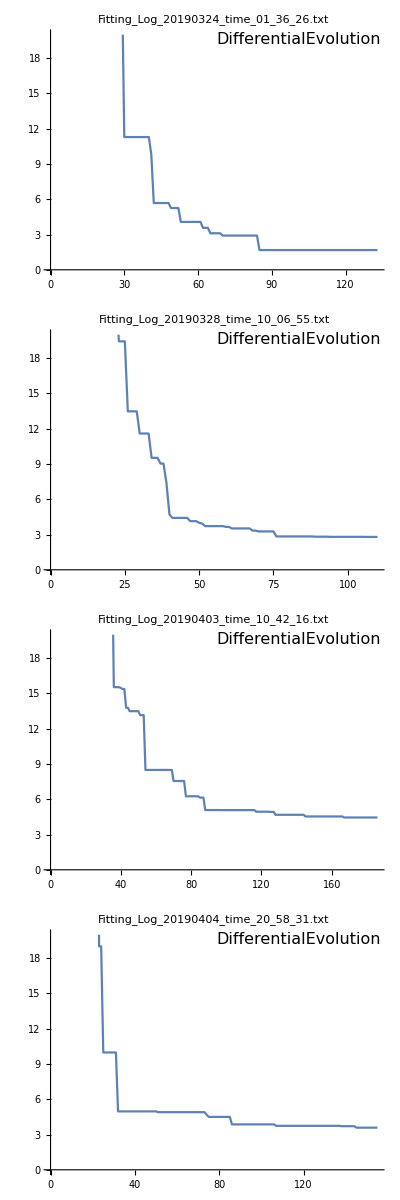

```mathematica
imagesize=400;
Column[
Table[
d=MinFucntionFromTBfitLog[path2files,flist⟦i⟧];
ListLinePlot[d⟦1⟧,PlotRange->{0,20},PlotLabel->Style[flist⟦i⟧,16],PlotLegends->Placed[Style[d⟦2⟧,16],{Right,Top}],ImageSize->imagesize],{i,Length[flist]}]]
```

Fitting Goodness analysis(03/04/2019)

```mathematica
(* generation of the atomic coordinates *)
type=1;
ribbontype=Switch[type,1,"Z",2,"A",3,"B"];
w=15;
data=Nanoribbon[type,w];
UnitCell=data⟦1⟧;
T=data⟦2⟧;
(*----------------------------------*)

(* extracting TB parameters *)
path=FileNameJoin[{parentDir,"raw data","DFT","ZGNR_"<>ToString@w,"TBM fitting"}];
SetDirectory[path];
logfname=First@FileNames["Fitting*"]
datelabel=StringTake[logfname,{-26;;-5}];
stepnumber=125;
tbparameters=StepParametersFromTBfitLog[path,logfname,stepnumber]
(* calculating TB bandstructure *)
TBfittedbands=ElectronicBands1Dp[UnitCell,T,tbparameters,{0,0,0},{0,0,0},{False,1}];


(* extracting DFT data to plot *)
path=FileNameJoin[{parentDir,"raw data","DFT","ZGNR_"<>ToString@w}];
fname1="ZGNR"<>ToString@w<>"_bands_2d.dat.1.2";
fname2="ZGNR"<>ToString@w<>"_bands.dat";
fname3="scf.out";
QEdftplotbands=Plotbandx2Mathematica[path,fname1,fname2,fname3];

fname1="bands.out";
fname2="scf.out";
QEdftbands=QE1DBands2Mathematica[path,fname1,fname2];

lim=8;

data2compare={QEdftplotbands⟦1⟧,QEdftbands⟦1⟧,TBfittedbands};
labels={"\\text{ZGNR"<>ToString@w<>"}",{"k","E-E_{F},\\text{ eV}"},{"\\text{DFT:QE plotband.x}","\\text{DFT:QE bands.out}","\\text{TB: fit "<>StringReplace[datelabel,"_"->" "]<>" step "<>ToString[stepnumber]<>"}"}};
plotranges={{0,π},{-lim,lim}};
linecolors={Directive[Red],Directive[{Dashed,Blue}],Directive[{DotDashed,Darker[Green,0.5]}]};
normalizationfactors={2 π,2 π,√(T.T)};
fermilevels={QEdftplotbands⟦2⟧,QEdftbands⟦2⟧,FermiEnergyAndBandGap[TBfittedbands]⟦1⟧};
plotstyleflag=1;

fig=CompareElectronicBands1D[data2compare,labels,plotranges,linecolors,normalizationfactors,fermilevels,plotstyleflag,ImageSize->{Automatic,380}]
```

Fitting_Log_20190403_time_10_42_16.txt

{{0,-2.8653,-0.0072,-0.2785},{1,0.0313,0.0056,0.0488},0,{{0,0},{0,0},{0,0},{0,0}}}

-Graphics-

```mathematica
SystemOpen[path]
```

```mathematica
path=FileNameJoin[{parentDir,"test"}];
fname=datelabel<>"_"<>"TB_fit_ZGNR"<>ToString[w]<>"_step_"<>ToString[stepnumber];
Export[FileNameJoin[{path,fname<>".png"}],fig,ImageResolution-> 300];
```

#### Optical absorption calculations in TB model

#### Collecting data for Kataura plots of zigzag graphene nanoribbons (14/02/2019)[Calculation based on gradient approximation Partoens2006](recalculation on 22/05/2019)

```mathematica
path=FileNameJoin[{parentDir,"test"}];

(* initial parameters for electronic structure *)
efield={0,0,0};
bfield={0,0,0};
mflag=3;
(*------------------------------- OPTIMIZATION -------------------------------------*)
(* unitcell optimization flag: 
opflag={True or False, optimization programme choice};
True - perform unit cell geometry optimization; 
False - skip optimization *)
opflag={False,1};
(*--------------------------------------------------------------------------------*)
probflag=True; (* note that this flag affects the structure of the output of ElectronicBands1D20190127 *)
NumberOfkPoints=1000;

(* initial parameters for absorption spectrum calculations *)
xrange={0,8}; (* frequency (energy) range *)
np=2000; (* number of points *)
sigma=0.03; (* broadening eV *)
polarization=2; (* 1-Ox; 2-Oy; 3-Oz; *)
(*---------------------------------*)

Do[
(* atomic structure *)
w=jj;
type=1;
ribbontype=Switch[type,1,"Z",2,"A",3,"B"];
data=Nanoribbon[type,w];
UnitCell=data⟦1⟧;
T=data⟦2⟧;
numberofatoms=Length[UnitCell];


(*%%%%%%%%%%%%%%%%%%%%%%%%%%% Energy band structure calculations %%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)

{bands,chargedensity,wfs,vmes,modelname,hoppingintegrals,overlappingintegrals,edgecorrections,β}=ElectronicBands1D20190127[UnitCell,T,efield,bfield,mflag,opflag,probflag,NumberOfkPoints];

(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%% Absorption calculation %%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
time=AbsoluteTiming[abdata=OpticalAbsorption1DCompiled2C[bands,wfs,vmes,xrange,np,sigma,polarization];];

(*%%%%%%%%%%%%%%%%%%%%%%%%%%%% Save absorption spectrum data %%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
date=DateString[{ "DayShort","_","MonthNameShort","_","Year"}];
fname=date<>"_ZGNR("<>ToString[w]<>")_absorption_TB_0_"<>ToString[xrange⟦2⟧]<>"_np"<>ToString@np;
mySave[{time,type,ribbontype,w,numberofatoms,NumberOfkPoints,efield,bfield,opflag,mflag,modelname,hoppingintegrals,overlappingintegrals,edgecorrections,β,UnitCell,T,xrange,np,sigma,polarization,abdata},path,fname];
,{jj,2,6}](* end Do *)
```

#### Collecting data for Kataura plots of armchair carbon nanotubes (14/02/2019)[Calculation based on gradient approximation Partoens2006, Reich2002](recalculation on 22/05/2019)

```mathematica
(* 16/02/2019 *)
path=FileNameJoin[{parentDir,"test"}];
(* bondlength tolerance is set to 0.05 *)

(* initial parameters for electronic structure *)
efield={0,0,0};
bfield={0,0,0};
mflag=2; (* 2-Reich2002, 3-Partoens2006 *)
(*------------------------------- OPTIMIZATION -----------------------------------*)
(* unitcell optimization flag: 
opflag={True or False, optimization programme choice};
True - perform unit cell geometry optimization; 
False - skip optimization *)
opflag={False,1};
(*--------------------------------------------------------------------------------*)
probflag=True; (* note that this flag affects the structure of the output of ElectronicBands1D20190127 *)
NumberOfkPoints=1000;


(* initial parameters for absorption spectrum calculations *)
xrange={0,8}; (* frequency (energy) range *)
np=2000; (* number of points *)
sigma=0.03; (* broadening eV *)
polarization=3; (* 1-Ox; 2-Oy; 3-Oz (translation axis for tubes); *)
(*---------------------------------*)

ParallelDo[
(* atomic structure *)
nn=jj;
mm=nn;

type=1;
data=Nanotube[type,nn,mm];
UnitCell=data⟦1⟧;
T=data⟦2⟧;
numberofatoms=Length[UnitCell];

(*%%%%%%%%%%%%%%%%%%%%%%%%%%% Energy band structure calculations %%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
{bands,chargedensity,wfs,vmes,modelname,hoppingintegrals,overlappingintegrals,edgecorrections,β}=ElectronicBands1D20190127[UnitCell,T,efield,bfield,mflag,opflag,probflag,NumberOfkPoints];

(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%% Absorption calculation %%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
time=AbsoluteTiming[abdata=OpticalAbsorption1DCompiled2C[bands,wfs,vmes,xrange,np,sigma,polarization];];

(*%%%%%%%%%%%%%%%%%%%%%%%%%%%% Save absorption spectrum data %%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
date=DateString[{ "DayShort","_","MonthNameShort","_","Year"}];
fname=date<>"_CNT("<>ToString[nn]<>","<>ToString[mm]<>")_absorption_TB_0_"<>ToString[xrange⟦2⟧]<>"_np"<>ToString@np;
mySave[{time,type,nn,mm,numberofatoms,NumberOfkPoints,efield,bfield,opflag,mflag,modelname,hoppingintegrals,overlappingintegrals,edgecorrections,β,UnitCell,T,xrange,np,sigma,polarization,abdata},path,fname];

,{jj,4,6},Method->"FinestGrained"](* end Do *)
```

#### Collecting data for Kataura plots of zigzag graphene nanoribbons with fitted TB parameters (19/05/2019)[Calculation based on gradient approximation]

```mathematica
path=FileNameJoin[{parentDir,"test"}];
path2read=FileNameJoin[{parentDir,"raw data","TBM fitting summary"}];
fname="19_May_2019_TB_parameters_averaged_over_ZGNR(6,9,12,15).txt";
Get[fname,Path->path2read]; (* get avtbparameters variable from the specified file *)

tbparameters=Append[Round[avtbparameters,0.0001],fname]

(* initial parameters for electronic structure *)
efield={0,0,0};
bfield={0,0,0};
(*------------------------------- OPTIMIZATION -----------------------------------*)
(* unitcell optimization flag: 
opflag={True or False, optimization programme choice};
True - perform unit cell geometry optimization; 
False - skip optimization *)
opflag={False,1};
(*--------------------------------------------------------------------------------*)
probflag=True;
NumberOfkPoints=1000;


(* initial parameters for absorption spectrum calculations *)
xrange={0,8}; (* frequency (energy) range *)
np=2000; (* number of points *)
sigma=0.03; (* broadening eV *)
polarization=2; (* 1-Ox; 2-Oy; 3-Oz; *)
(*---------------------------------*)

Do[
(* atomic structure *)
w=jj;
type=1;
ribbontype=Switch[type,1,"Z",2,"A",3,"B"];
data=Nanoribbon[type,w];
UnitCell=data⟦1⟧;
T=data⟦2⟧;
numberofatoms=Length[UnitCell];


(*%%%%%%%%%%%%%%%%%%%%%%%%%%% Energy band structure calculations %%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)

{bands,chargedensity,wfs,vmes,modelname,hoppingintegrals,overlappingintegrals,edgecorrections,β}=ElectronicBands1D20190406[UnitCell,T,tbparameters,efield,bfield,opflag,probflag,NumberOfkPoints];

(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%% Absorption calculation %%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
time=AbsoluteTiming[abdata=OpticalAbsorption1DCompiled2C[bands,wfs,vmes,xrange,np,sigma,polarization];];

(*%%%%%%%%%%%%%%%%%%%%%%%%%%%% Save absorption spectrum data %%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
date=DateString[{ "DayShort","_","MonthNameShort","_","Year"}];
fname=date<>"_ZGNR("<>ToString[w]<>")_absorption_TB_0_"<>ToString[xrange⟦2⟧]<>"_np"<>ToString@np;
mySave[{time,type,ribbontype,w,numberofatoms,NumberOfkPoints,efield,bfield,opflag,modelname,hoppingintegrals,overlappingintegrals,edgecorrections,β,UnitCell,T,xrange,np,sigma,polarization,abdata},path,fname];
,{jj,2,6}](* end Do *)
```

{{0.,-2.7616,-0.0027,-0.2438},{1.,0.0072,0.0173,0.0269},0.,{{0.,0.},{0.,0.},{0.,0.},{0.,0.}},19_May_2019_TB_parameters_averaged_over_ZGNR(6,9,12,15).txt}

#### Collecting data for Kataura plots of zigzag graphene nanoribbons with fitted TB parameters and Partoens2006 parameters and edge states excluded (26/05/2019)[Calculation based on gradient approximation]

```mathematica
path=FileNameJoin[{parentDir,"test"}];
path2read=FileNameJoin[{parentDir,"raw data","TBM fitting summary"}];
fname="19_May_2019_TB_parameters_averaged_over_ZGNR(6,9,12,15).txt";
Get[fname,Path->path2read]; (* get avtbparameters variable from the specified file *)

tbparameters={Append[Round[avtbparameters,0.0001],fname],{{0,3.12,0,0},{1,0,0,0},0,{{0,0},{0,0},{0,0},{0,0}},"Partoens2006"}}⟦2⟧ (* 1-fitted TBM, 2-Partoens2006 TBM *)

(* initial parameters for electronic structure *)
efield={0,0,0};
bfield={0,0,0};
(*------------------------------- OPTIMIZATION -----------------------------------*)
(* unitcell optimization flag: 
opflag={True or False, optimization programme choice};
True - perform unit cell geometry optimization; 
False - skip optimization *)
opflag={False,1};
(*--------------------------------------------------------------------------------*)
probflag=True;
NumberOfkPoints=1000;


(* initial parameters for absorption spectrum calculations *)
xrange={0,8}; (* frequency (energy) range *)
np=2000; (* number of points *)
sigma=0.03; (* broadening eV *)
polarization=2; (* 1-Ox; 2-Oy; 3-Oz; *)
(*---------------------------------*)

ParallelDo[
(* atomic structure *)
w=jj;
type=1;
ribbontype=Switch[type,1,"Z",2,"A",3,"B"];
data=Nanoribbon[type,w];
UnitCell=data⟦1⟧;
T=data⟦2⟧;
numberofatoms=Length[UnitCell];


(*%%%%%%%%%%%%%%%%%%%%%%%%%%% Energy band structure calculations %%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
{bands,chargedensity,wfs,vmes,modelname,hoppingintegrals,overlappingintegrals,edgecorrections,β}=ElectronicBands1D20190406[UnitCell,T,tbparameters,efield,bfield,opflag,probflag,NumberOfkPoints];

(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%% Absorption calculation %%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
time=AbsoluteTiming[abdata=OpticalAbsorption1DCompiled2Cbulk[bands,wfs,vmes,xrange,np,sigma,polarization];];

(*%%%%%%%%%%%%%%%%%%%%%%%%%%%% Save absorption spectrum data %%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
date=DateString[{ "DayShort","_","MonthNameShort","_","Year"}];
fname=date<>"_ZGNR("<>ToString[w]<>")_absorption_bulk_TB_0_"<>ToString[xrange⟦2⟧]<>"_np"<>ToString@np;
mySave[{time,type,ribbontype,w,numberofatoms,NumberOfkPoints,efield,bfield,opflag,modelname,hoppingintegrals,overlappingintegrals,edgecorrections,β,UnitCell,T,xrange,np,sigma,polarization,abdata},path,fname];
,{jj,2,4},Method->"FinestGrained"](* end ParallelDo *)
```

{{0,3.12,0,0},{1,0,0,0},0,{{0,0},{0,0},{0,0},{0,0}},Partoens2006}

#### Repeating Jiang2008 calculations (28/06/2019)

```mathematica
(* 28/06/2019 *)
path=FileNameJoin[{parentDir,"test"}];
path2read=FileNameJoin[{parentDir,"raw data","TBM fitting summary"}];
fname="19_May_2019_TB_parameters_averaged_over_ZGNR(6,9,12,15).txt";
Get[fname,Path->path2read]; (* get avtbparameters variable from the specified file *)

tbparameters=Append[Round[avtbparameters,0.0001],fname]

(* initial parameters for electronic structure *)
efield={0,0,0};
bfield={0,0,0};
(*------------------------------- OPTIMIZATION -----------------------------------*)
(* unitcell optimization flag: 
opflag={True or False, optimization programme choice};
True - perform unit cell geometry optimization; 
False - skip optimization *)
opflag={False,1};
(*--------------------------------------------------------------------------------*)
probflag=False;
NumberOfkPoints=1000;

ZGNRBulkVanHoveSingularitesDifferences={};

Do[
(* atomic structure *)
w=jj;
type=1;
ribbontype=Switch[type,1,"Z",2,"A",3,"B"];
data=Nanoribbon[type,w];
UnitCell=data⟦1⟧;
T=data⟦2⟧;
numberofatoms=Length[UnitCell];


(*%%%%%%%%%%%%%%%%%%%%%%%%%%% Energy band structure calculations %%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
{bands,modelname,hoppingintegrals,overlappingintegrals,edgecorrections,β}=ElectronicBands1D20190406[UnitCell,T,tbparameters,efield,bfield,opflag,probflag,NumberOfkPoints];

AppendTo[ZGNRBulkVanHoveSingularitesDifferences,Table[{w,NthOrderGap[bands,i]⟦1⟧},{i,4}]];
,{jj,Range[6,7]}](* end Do *)

(*%%%%%%%%%%%%%%%%%%%%%%%%%%%% Save absorption spectrum data %%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
date=DateString[{ "DayShort","_","MonthNameShort","_","Year"}];
fname=date<>"_ZGNR_bulk_van_Hove_singularities_TB";
mySave[{NumberOfkPoints,efield,bfield,opflag,modelname,hoppingintegrals,overlappingintegrals,edgecorrections,β,ZGNRBulkVanHoveSingularitesDifferences},path,fname];
```

{{0.,-2.7616,-0.0027,-0.2438},{1.,0.0072,0.0173,0.0269},0.,{{0.,0.},{0.,0.},{0.,0.},{0.,0.}},19_May_2019_TB_parameters_averaged_over_ZGNR(6,9,12,15).txt}

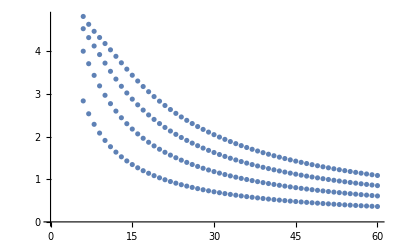

```mathematica
(* test differences between van Hove singularities symmetrically placed around the Fermi level *)
ListPlot[ZGNRBulkVanHoveSingularitesDifferences]
```

```mathematica
(* test NthOrderGap *)
FermiEnergyAndBandGap[bands]
glines=Table[NthOrderGap[bands,i],{i,4}]
```

{0.00600307,-0.000668076}

{{2.83901,-1.4619},{4.00557,-2.11282},{4.53361,-2.38231},{4.82105,-2.50242}}

```mathematica
(* test van Hove singularity position determination *)
path=FileNameJoin[{parentDir,"raw data","DFT","ZGNR_6"}];
fname1="bands.out";
fname2="scf.out";
QEdftbands=QE1DBands2Mathematica[path,fname1,fname2];

lim=4;

fig=CompareElectronicBands1D[{QEdftbands⟦1⟧,bands},{"\\text{ZGNR"<>ToString@w<>"}",{"k","E-E_{F},\\text{ eV}"},{"\\text{DFT:QE}","\\text{TB:Partoens2006}"}},{{0,π},{-lim,lim}},{Directive[Red],Directive[Blue]},{2 π,√(T.T)},{QEdftbands⟦2⟧,FermiEnergyAndBandGap[bands]⟦1⟧},1,ImageSize->{Automatic,380},GridLines->{None,Flatten[{#⟦2⟧,Plus@@#}&/@glines]}]
```

-Graphics-

```mathematica
Clear[NthOrderGap];
NthOrderGap[data_,n_(* n=0 -- normal band gap; n=1,2,3,... -- n-th order gap*)]:=
Module[
{
dim,
cbandmin,
vbandmax,
gap
},
dim=Dimensions[data];

If[ 
	(dim⟦1⟧-1)//EvenQ,
	(* likely isolator of semiconductor because electrons fill all the bands (states) in pairs with spins up and down *)
cbandmin=Min[data⟦(dim⟦1⟧-1)/2+1+n⟧];
vbandmax=Max[data⟦(dim⟦1⟧-1)/2-n⟧];
gap=cbandmin-vbandmax,
	(* metal because one band (state) should be half filled with only spin up or only spin down; position of the Fermi level coincide with the position of the half-filled state *)
	If[
		dim⟦2⟧>1,(* 1,2,3D-crystals *)
		gap=0(* eV *),
		(* 0-diminsional cluster *)
		cbandmin=Min[data⟦Ceiling[(dim⟦1⟧-1)/2]+1+n⟧];
		vbandmax=Max[data⟦Ceiling[(dim⟦1⟧-1)/2-n]⟧];
		gap=cbandmin-vbandmax(* eV *)
	](* end If *);
](* end If *);
{gap,vbandmax}

](* end Module *);
```

#### Figures for the paper (25/05/2017)

#### ToTxt function

```mathematica
Clear[ToTxt];
ToTxt[path_,fnametag_,data_]:=Module[
{
str,
text,
nd,
location
},
 nd=PaddedForm[1.0 #,{10,8},ExponentFunction->(If[-Infinity<#<Infinity,Null]&)]&;
location=FileNameJoin[{path,fnametag<>DateString[{"Year","Month","Day","_time_","Hour","_","Minute","_","Second"}]<>".txt"}];
str=OpenWrite[location,FormatType-> OutputForm,CharacterEncoding->"ASCII"];
     text=Row[{StringPadRight[ToString[nd[#⟦1⟧]],10],StringPadLeft[ToString@nd[#⟦2⟧],10],StringPadLeft[ToString@nd[#⟦3⟧],10]},"\t"]&/@data;
     Scan[Write[str,#]&,text];
      Close[str];
location
](* end Module *)
```

#### GetOrderedListOfAbsorptionDataFiles function

```mathematica
Clear[GetOrderedListOfAbsorptionDataFiles];
GetOrderedListOfAbsorptionDataFiles[path2read_,flag_(* 1-ribbon spectra, 2-tube spectra *)]:=Module[
{
flist,
fun
},
SetDirectory[path2read];
flist=FileNames[];
flist=Select[flist,StringMatchQ[#,__~~"absorption"~~__]&];

Switch[flag,
1,
fun=ToExpression[StringTake[StringCases[#,"ZGNR("~~__~~"_a"],{6,-4}]⟦1⟧]&,
2,
fun=ToExpression[StringTake[StringCases[#,","~~__~~"_a"],{2,-4}]⟦1⟧]&
];

flist=Sort[flist,fun[#1]<fun[#2]&];

{(*ordered list*)flist,
(* ordered list formatted as a Table *)Grid[Table[{i,flist⟦i⟧},{i,Length[flist]}],Frame->All,Background->{None,{{White,LightBlue}}}]}

]
```

#### [Supplementary Figure 1]: Averaging TB parameters fitted to QE DFT ZGNR(6,9,12,15) (05/04/2019)

Averaging fitted parameters over several ribbons of different width (05/04/2019)

```mathematica
path2read=FileNameJoin[{parentDir,"raw data","TBM fitting summary"}];
SetDirectory[path2read];
flist=FileNames["Fitting*"];
Grid[Table[{i,flist⟦i⟧},{i,Length[flist]}],Frame->All,Background->{None,{{LightBlue,White}}}]
fname=flist⟦1⟧
```

1 | Fitting_Log_20190324_time_01_36_26.txt
2 | Fitting_Log_20190328_time_10_06_55.txt
3 | Fitting_Log_20190403_time_10_42_16.txt
4 | Fitting_Log_20190404_time_20_58_31.txt

Fitting_Log_20190324_time_01_36_26.txt

```mathematica
d=Table[MinFucntionFromTBfitLog[path2read,flist⟦i⟧],{i,Length[flist]}];
```

```mathematica
numberofstepslist=Length/@d⟦;;,1⟧
```

{133,110,186,155}

```mathematica
(* TB parameters *)
path2read=FileNameJoin[{parentDir,"raw data","TBM fitting summary"}];

tbplist=Table[
logfname=flist⟦i⟧;
d=MinFucntionFromTBfitLog[path2read,logfname];
stepnumber=Length[d⟦1⟧];
tbparameters=StepParametersFromTBfitLog[path2read,logfname,stepnumber],
{i,Length[flist]}]
```

{{{0,-2.71634,-0.009232,-0.244527},{1,0.000789,0.023853,0.018411},0,{{0,0},{0,0},{0,0},{0,0}}},{{0,-2.7457,0.0021,-0.2331},{1,0.0032,0.0177,0.0222},0,{{0,0},{0,0},{0,0},{0,0}}},{{0,-2.802,0.0043,-0.2494},{1,0.0134,0.0144,0.0306},0,{{0,0},{0,0},{0,0},{0,0}}},{{0,-2.7824,-0.008,-0.248},{1,0.0116,0.0131,0.0365},0,{{0,0},{0,0},{0,0},{0,0}}}}

```mathematica
(* hopping integrals *)
Grid[tbplist⟦;;,1⟧]
(* averaging over fitted data *)
avt=Total[tbplist⟦;;,1⟧]/Length[flist]

(* overlapping integrals *)
Grid[tbplist⟦;;,2⟧]
(* averaging over fitted data *)
avs=Total[tbplist⟦;;,2⟧]/Length[flist]

(* strain exponents *)
Grid[{tbplist⟦;;,3⟧}]
(* averaging over fitted data *)
avbeta=Total[tbplist⟦;;,3⟧]/Length[flist]

(* edge corrections *)
Grid[tbplist⟦;;,4⟧]
(* averaging over fitted data *)
avedge=Total[tbplist⟦;;,4⟧]/Length[flist]
```

0 | -2.71634 | -0.009232 | -0.244527
0 | -2.7457 | 0.0021 | -0.2331
0 | -2.802 | 0.0043 | -0.2494
0 | -2.7824 | -0.008 | -0.248

{0,-2.76161,-0.002708,-0.243757}

1 | 0.000789 | 0.023853 | 0.018411
1 | 0.0032 | 0.0177 | 0.0222
1 | 0.0134 | 0.0144 | 0.0306
1 | 0.0116 | 0.0131 | 0.0365

{1,0.00724725,0.0172633,0.0269278}

0 | 0 | 0 | 0

0

{0,0} | {0,0} | {0,0} | {0,0}
{0,0} | {0,0} | {0,0} | {0,0}
{0,0} | {0,0} | {0,0} | {0,0}
{0,0} | {0,0} | {0,0} | {0,0}

{{0,0},{0,0},{0,0},{0,0}}

```mathematica
numofdatasets=Length[tbplist];
avtbparameters=Table[Total[tbplist⟦;;,i⟧]/numofdatasets,{i,numofdatasets}]
```

{{0,-2.76161,-0.002708,-0.243757},{1,0.00724725,0.0172633,0.0269278},0,{{0,0},{0,0},{0,0},{0,0}}}

```mathematica
SystemOpen[path]
```

```mathematica
(* Save the results for the tb parameters *)
path=FileNameJoin[{parentDir,"test"}];
date=DateString[{ "DayShort","_","MonthNameShort","_","Year"}];
fname2=date<>"_TB_parameters_averaged_over_ZGNR(6,9,12,15).txt";
mySave[{avtbparameters},path,fname2]
```

[Supplementary Figure 1]: Fitting Goodness analysis (05/04/2019)

```mathematica
(* TB parameters *)
path2read=FileNameJoin[{parentDir,"raw data","TBM fitting summary"}];
fname="19_May_2019_TB_parameters_averaged_over_ZGNR(6,9,12,15).txt";
Get[fname,Path->path2read];

tbparameters=Append[Round[avtbparameters,0.0001],fname]

counter=0;
windlist={5,6,9,12,15,20};
last=Length[windlist];

efield={0,0,0};
bfield={0,0,0};
opflag={False,1};
probflag=False;
NumberOfkPoints=100;

glist=Table[
counter++;
(* atomic structure *)
type=1;

w=wind;
data=Nanoribbon[type,w];
UnitCell=data⟦1⟧;
T=data⟦2⟧;

TBfittedbands=ElectronicBands1D20190406[UnitCell,T,tbparameters,efield,bfield,opflag,probflag,NumberOfkPoints]⟦1⟧;

path=FileNameJoin[{parentDir,"raw data","DFT","ZGNR_"<>ToString@w}];
fname1="bands.out";
fname2="scf.out";

QEdftbands=QE1DBands2Mathematica[path,fname1,fname2];

lim=4;

labels={"\\text{ZGNR("<>ToString@w<>")}",{"k","E-E_{\\mathrm{F}},\\text{ eV}"},{"\\text{DFT:QE}","\\text{TB: average fit}"}};
plotranges={{0,π},{-lim,lim}};
linecolors={Directive[Red],Directive[{Dashed,Blue}]};
normalizationfactors={2 π,√(T.T)};
fermilevels={QEdftbands⟦2⟧,FermiEnergyAndBandGap[TBfittedbands]⟦1⟧};
plotstyleflag=Switch[counter,1,2,last,3,_,3];

CompareElectronicBands1D[{QEdftbands⟦1⟧,TBfittedbands},labels,plotranges,linecolors,normalizationfactors,fermilevels,plotstyleflag,ImageSize->{Automatic,380}],
{wind,windlist}];

fig=Grid[{glist}]
```

{{0.,-2.7616,-0.0027,-0.2438},{1.,0.0072,0.0173,0.0269},0.,{{0.,0.},{0.,0.},{0.,0.},{0.,0.}},19_May_2019_TB_parameters_averaged_over_ZGNR(6,9,12,15).txt}

-Graphics-

```mathematica
SystemOpen[path]
```

```mathematica
path=FileNameJoin[{parentDir,"test"}];
fname="Figure_S1";
Export[FileNameJoin[{path,fname<>".png"}],fig,ImageResolution-> 300];
```

#### [Supplementary Figure 2]: Comparing Reich2002 TB parameters to QE DFT (Fitting Goodness analysis) (19/05/2019)

```mathematica
counter=0;
nindlist={10,21};
last=Length[nindlist];
efield={0,0,0};
bfield={0,0,0};
opflag={False,1};
NumberOfkPoints=100;
probflag=False;
mflag=2; (* Reich2002 TBM*)

fig=Grid[{Table[
counter++;
(* atomic structure *)
type=1;

n=nind;
data=Nanotube[type,n,n];
UnitCell=data⟦1⟧;
T=data⟦2⟧;

TBReich2002bands=ElectronicBands1D20190127[UnitCell,T,efield,bfield,mflag,opflag,probflag,NumberOfkPoints]⟦1⟧;

path=FileNameJoin[{parentDir,"raw data","DFT","CNT("<>ToString@n<>","<>ToString@n<>")"}];
fname1="bands.out";
fname2="scf.out";

QEdftbands=QE1DBands2Mathematica[path,fname1,fname2];

lim=4;


labels={"\\text{CNT("<>ToString@n<>","<>ToString@n<>")}",{"k","E-E_{\\mathrm{F}},\\text{ eV}"},{"\\text{DFT:QE}","\\text{TB: Reich2002}"}};
plotranges={{0,π},{-lim,lim}};
linecolors={Directive[Red],Directive[{Dashed,Blue}]};
normalizationfactors={2 π,√(T.T)};
fermilevels={QEdftbands⟦2⟧,FermiEnergyAndBandGap[TBReich2002bands]⟦1⟧};
plotstyleflag=Switch[counter,1,2,last,3,_,3];

CompareElectronicBands1D[{QEdftbands⟦1⟧,TBReich2002bands},labels,plotranges,linecolors,normalizationfactors,fermilevels,plotstyleflag,ImageSize->{Automatic,380}],
{nind,nindlist}]}]
```

-Graphics-

```mathematica
SystemOpen[path]
```

```mathematica
path=FileNameJoin[{parentDir,"test"}];
fname="Figure_S2";
Export[FileNameJoin[{path,fname<>".png"}],fig,ImageResolution-> 300];
```

#### [Supplementary Figure 3, Supplementary Figure 4]: Zigzag graphene ribbons (ZGNRs)

[Supplementary Figure 3]: Absorption resonance selection in full and bulk spectra Partoens2006 (26/05/2019)

```mathematica
flag=1; (* 1-ribbon spectra *)

path2read=FileNameJoin[{parentDir,"raw data","TB","zigzag ribbons","2019_05_22_Partoens2006"}];
{flist,formattedflist}=GetOrderedListOfAbsorptionDataFiles[path2read,flag];
formattedflist

path2readb=FileNameJoin[{parentDir,"raw data","TB","zigzag ribbons","2019_05_26_Partoens2006_bulk"}];
{flistb,formattedflistb}=GetOrderedListOfAbsorptionDataFiles[path2readb,flag];
formattedflistb
```

1 | 22_May_2019_ZGNR(2)_absorption_TB_0_8_np2000
2 | 22_May_2019_ZGNR(3)_absorption_TB_0_8_np2000
3 | 22_May_2019_ZGNR(4)_absorption_TB_0_8_np2000
4 | 22_May_2019_ZGNR(5)_absorption_TB_0_8_np2000
5 | 22_May_2019_ZGNR(6)_absorption_TB_0_8_np2000
6 | 22_May_2019_ZGNR(7)_absorption_TB_0_8_np2000
7 | 22_May_2019_ZGNR(8)_absorption_TB_0_8_np2000
8 | 22_May_2019_ZGNR(9)_absorption_TB_0_8_np2000
9 | 22_May_2019_ZGNR(10)_absorption_TB_0_8_np2000
10 | 22_May_2019_ZGNR(11)_absorption_TB_0_8_np2000
11 | 22_May_2019_ZGNR(12)_absorption_TB_0_8_np2000
12 | 22_May_2019_ZGNR(13)_absorption_TB_0_8_np2000
13 | 22_May_2019_ZGNR(14)_absorption_TB_0_8_np2000
14 | 22_May_2019_ZGNR(15)_absorption_TB_0_8_np2000
15 | 22_May_2019_ZGNR(16)_absorption_TB_0_8_np2000
16 | 22_May_2019_ZGNR(17)_absorption_TB_0_8_np2000
17 | 22_May_2019_ZGNR(18)_absorption_TB_0_8_np2000
18 | 22_May_2019_ZGNR(19)_absorption_TB_0_8_np2000
19 | 22_May_2019_ZGNR(20)_absorption_TB_0_8_np2000
20 | 22_May_2019_ZGNR(21)_absorption_TB_0_8_np2000
21 | 22_May_2019_ZGNR(22)_absorption_TB_0_8_np2000
22 | 22_May_2019_ZGNR(23)_absorption_TB_0_8_np2000
23 | 22_May_2019_ZGNR(24)_absorption_TB_0_8_np2000
24 | 22_May_2019_ZGNR(25)_absorption_TB_0_8_np2000
25 | 22_May_2019_ZGNR(26)_absorption_TB_0_8_np2000
26 | 22_May_2019_ZGNR(27)_absorption_TB_0_8_np2000
27 | 22_May_2019_ZGNR(28)_absorption_TB_0_8_np2000
28 | 22_May_2019_ZGNR(29)_absorption_TB_0_8_np2000
29 | 22_May_2019_ZGNR(30)_absorption_TB_0_8_np2000
30 | 22_May_2019_ZGNR(31)_absorption_TB_0_8_np2000
31 | 22_May_2019_ZGNR(32)_absorption_TB_0_8_np2000
32 | 22_May_2019_ZGNR(33)_absorption_TB_0_8_np2000
33 | 22_May_2019_ZGNR(34)_absorption_TB_0_8_np2000
34 | 22_May_2019_ZGNR(35)_absorption_TB_0_8_np2000
35 | 22_May_2019_ZGNR(36)_absorption_TB_0_8_np2000
36 | 22_May_2019_ZGNR(37)_absorption_TB_0_8_np2000
37 | 22_May_2019_ZGNR(38)_absorption_TB_0_8_np2000
38 | 22_May_2019_ZGNR(39)_absorption_TB_0_8_np2000
39 | 22_May_2019_ZGNR(40)_absorption_TB_0_8_np2000
40 | 22_May_2019_ZGNR(41)_absorption_TB_0_8_np2000
41 | 22_May_2019_ZGNR(42)_absorption_TB_0_8_np2000
42 | 22_May_2019_ZGNR(43)_absorption_TB_0_8_np2000
43 | 22_May_2019_ZGNR(44)_absorption_TB_0_8_np2000
44 | 22_May_2019_ZGNR(45)_absorption_TB_0_8_np2000
45 | 22_May_2019_ZGNR(46)_absorption_TB_0_8_np2000
46 | 22_May_2019_ZGNR(47)_absorption_TB_0_8_np2000
47 | 22_May_2019_ZGNR(48)_absorption_TB_0_8_np2000
48 | 22_May_2019_ZGNR(49)_absorption_TB_0_8_np2000
49 | 22_May_2019_ZGNR(50)_absorption_TB_0_8_np2000
50 | 22_May_2019_ZGNR(51)_absorption_TB_0_8_np2000
51 | 22_May_2019_ZGNR(52)_absorption_TB_0_8_np2000
52 | 22_May_2019_ZGNR(53)_absorption_TB_0_8_np2000
53 | 22_May_2019_ZGNR(54)_absorption_TB_0_8_np2000
54 | 22_May_2019_ZGNR(55)_absorption_TB_0_8_np2000
55 | 22_May_2019_ZGNR(56)_absorption_TB_0_8_np2000
56 | 22_May_2019_ZGNR(57)_absorption_TB_0_8_np2000
57 | 22_May_2019_ZGNR(58)_absorption_TB_0_8_np2000
58 | 22_May_2019_ZGNR(59)_absorption_TB_0_8_np2000
59 | 22_May_2019_ZGNR(60)_absorption_TB_0_8_np2000

1 | 26_May_2019_ZGNR(2)_absorption_bulk_TB_0_8_np2000
2 | 26_May_2019_ZGNR(3)_absorption_bulk_TB_0_8_np2000
3 | 26_May_2019_ZGNR(4)_absorption_bulk_TB_0_8_np2000
4 | 26_May_2019_ZGNR(5)_absorption_bulk_TB_0_8_np2000
5 | 26_May_2019_ZGNR(6)_absorption_bulk_TB_0_8_np2000
6 | 26_May_2019_ZGNR(7)_absorption_bulk_TB_0_8_np2000
7 | 26_May_2019_ZGNR(8)_absorption_bulk_TB_0_8_np2000
8 | 26_May_2019_ZGNR(9)_absorption_bulk_TB_0_8_np2000
9 | 26_May_2019_ZGNR(10)_absorption_bulk_TB_0_8_np2000
10 | 26_May_2019_ZGNR(11)_absorption_bulk_TB_0_8_np2000
11 | 26_May_2019_ZGNR(12)_absorption_bulk_TB_0_8_np2000
12 | 26_May_2019_ZGNR(13)_absorption_bulk_TB_0_8_np2000
13 | 26_May_2019_ZGNR(14)_absorption_bulk_TB_0_8_np2000
14 | 26_May_2019_ZGNR(15)_absorption_bulk_TB_0_8_np2000
15 | 26_May_2019_ZGNR(16)_absorption_bulk_TB_0_8_np2000
16 | 26_May_2019_ZGNR(17)_absorption_bulk_TB_0_8_np2000
17 | 26_May_2019_ZGNR(18)_absorption_bulk_TB_0_8_np2000
18 | 26_May_2019_ZGNR(19)_absorption_bulk_TB_0_8_np2000
19 | 26_May_2019_ZGNR(20)_absorption_bulk_TB_0_8_np2000
20 | 26_May_2019_ZGNR(21)_absorption_bulk_TB_0_8_np2000
21 | 26_May_2019_ZGNR(22)_absorption_bulk_TB_0_8_np2000
22 | 26_May_2019_ZGNR(23)_absorption_bulk_TB_0_8_np2000
23 | 26_May_2019_ZGNR(24)_absorption_bulk_TB_0_8_np2000
24 | 26_May_2019_ZGNR(25)_absorption_bulk_TB_0_8_np2000
25 | 26_May_2019_ZGNR(26)_absorption_bulk_TB_0_8_np2000
26 | 26_May_2019_ZGNR(27)_absorption_bulk_TB_0_8_np2000
27 | 26_May_2019_ZGNR(28)_absorption_bulk_TB_0_8_np2000
28 | 26_May_2019_ZGNR(29)_absorption_bulk_TB_0_8_np2000
29 | 26_May_2019_ZGNR(30)_absorption_bulk_TB_0_8_np2000
30 | 26_May_2019_ZGNR(31)_absorption_bulk_TB_0_8_np2000
31 | 26_May_2019_ZGNR(32)_absorption_bulk_TB_0_8_np2000
32 | 26_May_2019_ZGNR(33)_absorption_bulk_TB_0_8_np2000
33 | 26_May_2019_ZGNR(34)_absorption_bulk_TB_0_8_np2000
34 | 26_May_2019_ZGNR(35)_absorption_bulk_TB_0_8_np2000
35 | 26_May_2019_ZGNR(36)_absorption_bulk_TB_0_8_np2000
36 | 26_May_2019_ZGNR(37)_absorption_bulk_TB_0_8_np2000
37 | 26_May_2019_ZGNR(38)_absorption_bulk_TB_0_8_np2000
38 | 26_May_2019_ZGNR(39)_absorption_bulk_TB_0_8_np2000
39 | 26_May_2019_ZGNR(40)_absorption_bulk_TB_0_8_np2000
40 | 26_May_2019_ZGNR(41)_absorption_bulk_TB_0_8_np2000
41 | 26_May_2019_ZGNR(42)_absorption_bulk_TB_0_8_np2000
42 | 26_May_2019_ZGNR(43)_absorption_bulk_TB_0_8_np2000
43 | 26_May_2019_ZGNR(44)_absorption_bulk_TB_0_8_np2000
44 | 26_May_2019_ZGNR(45)_absorption_bulk_TB_0_8_np2000
45 | 26_May_2019_ZGNR(46)_absorption_bulk_TB_0_8_np2000
46 | 26_May_2019_ZGNR(47)_absorption_bulk_TB_0_8_np2000
47 | 26_May_2019_ZGNR(48)_absorption_bulk_TB_0_8_np2000
48 | 26_May_2019_ZGNR(49)_absorption_bulk_TB_0_8_np2000
49 | 26_May_2019_ZGNR(50)_absorption_bulk_TB_0_8_np2000
50 | 26_May_2019_ZGNR(51)_absorption_bulk_TB_0_8_np2000
51 | 26_May_2019_ZGNR(52)_absorption_bulk_TB_0_8_np2000
52 | 26_May_2019_ZGNR(53)_absorption_bulk_TB_0_8_np2000
53 | 26_May_2019_ZGNR(54)_absorption_bulk_TB_0_8_np2000
54 | 26_May_2019_ZGNR(55)_absorption_bulk_TB_0_8_np2000
55 | 26_May_2019_ZGNR(56)_absorption_bulk_TB_0_8_np2000
56 | 26_May_2019_ZGNR(57)_absorption_bulk_TB_0_8_np2000
57 | 26_May_2019_ZGNR(58)_absorption_bulk_TB_0_8_np2000
58 | 26_May_2019_ZGNR(59)_absorption_bulk_TB_0_8_np2000
59 | 26_May_2019_ZGNR(60)_absorption_bulk_TB_0_8_np2000

```mathematica
katauraplotr={};
katauraplotrb={};

(* ListPlot parameters *)
ts=MaTeX[#,FontSize->15]&;
tss=MaTeX[#,FontSize->14]&;
imagesize=200;

ticklen={0.03,0}/3;
yticklen={0.03,0};
xticks={#⟦1⟧,ts[#⟦2⟧],#⟦3⟧,#⟦4⟧}&/@LinTicks[0,8,2,4,MajorTickLength->ticklen,MinorTickLength->ticklen/1.7];
yticks={#⟦1⟧,ts[#⟦2⟧],#⟦3⟧,#⟦4⟧}&/@LinTicks[0,1,0.5,5,MajorTickLength->yticklen,MinorTickLength->yticklen/1.7];

splist=Table[
(* reading absorption spectrum from file *)
Get[flist⟦i⟧,Path->path2read];

(* normalizing the spectrum *)
max=Max[abdata⟦;;,2⟧];
data2plot={#⟦1⟧,(#⟦2⟧)/max}&/@abdata;

spectrum=Chop[data2plot,10^-3];

(* bulk part of the spectrum *)
(* reading absorption spectrum from file *)
Get[flistb⟦i⟧,Path->path2readb];

(* normalizing the spectrum *)

data2plot={#⟦1⟧,(#⟦2⟧)/max}&/@abdata;

spectrumb=Chop[data2plot,10^-3];
(**)

denergy=0.07;
dintensity=0.08;(* 8% of the peak value *)

peaks=FindPeaksInSpectrum20190217[spectrum,denergy,dintensity];
peaks=Select[peaks,#⟦1⟧<6.3&];
Scan[AppendTo[katauraplotr,{w,#⟦1⟧}]&,peaks];
(* bulk transitions *)
peaksb=FindPeaksInSpectrum20190217[spectrumb,denergy,dintensity];
peaksb=Select[peaksb,#⟦1⟧<6.3&];
Scan[AppendTo[katauraplotrb,{w,#⟦1⟧}]&,peaksb];

gridlines={White,AbsoluteThickness[0.5],Line[{{#⟦1⟧,0},{#⟦1⟧,#⟦2⟧}}]}&/@peaksb;

ListLinePlot[{spectrum,spectrumb},
PlotRange->{0,1},
PlotRangePadding->{Scaled[0.05],Scaled[0.08]},
PlotStyle->{Directive[AbsoluteThickness[0.75],Blue],None},
Filling->{1->{Axis,LightBlue},2->{Axis,Red}},

Frame->True,
FrameTicks->{{yticks,{#⟦1⟧,"",#⟦3⟧,#⟦4⟧}&/@yticks},{xticks,{#⟦1⟧,"",#⟦3⟧,#⟦4⟧}&/@xticks}},
FrameLabel->{ts@"\\hbar \\omega, \\text{eV}",tss@"A(\\hbar \\omega), \\text{arb.}"},
FrameStyle->Directive[{Black,AbsoluteThickness[1]}],
FrameTicksStyle->Directive[{Black,AbsoluteThickness[1]}],
Epilog->{Red,Circle[#,0.25 {0.5,0.1}]&/@peaks,Text[ts["w="<>ToString[i+1]],Scaled[{If[i>33,0.5,0.6],0.8}]],gridlines},
ImageSize->imagesize]
,
{i,Min[Length[flist],Length[flistb]]}
];

path=FileNameJoin[{parentDir,"test"}];
date=DateString[{ "DayShort","_","MonthNameShort","_","Year"}];
fname=date<>"_data_TB_Partoens2006_Kataura_plot_ZGNR";
katauraplotrPartoens2006=katauraplotr;
mySave[{denergy,dintensity,katauraplotrPartoens2006},path,fname]

fname=date<>"_data_TB_Partoens2006_Kataura_plot_ZGNR_bulk";
katauraplotrPartoens2006b=katauraplotrb;
mySave[{denergy,dintensity,katauraplotrPartoens2006b},path,fname]

fgrid=Table[If[(i-1) 8+j>Length[splist],

ListLinePlot[{{0,0}},
PlotRange->{{0,8},{0,1}},
PlotRangePadding->{Scaled[0.05],Scaled[0.08]},
PlotStyle->Blue,
Frame->True,
FrameTicks->{{yticks,{#⟦1⟧,"",#⟦3⟧,#⟦4⟧}&/@yticks},{xticks,{#⟦1⟧,"",#⟦3⟧,#⟦4⟧}&/@xticks}},
FrameLabel->{ts@"\\hbar \\omega, \\text{eV}",tss@"A(\\hbar \\omega), \\text{arb.}"},
FrameStyle->Directive[{Black,AbsoluteThickness[1]}],
FrameTicksStyle->Directive[{Black,AbsoluteThickness[1]}],
ImageSize->imagesize]
,splist⟦(i-1) 8+j⟧],{i,8},{j,8}];
```

```mathematica
leftPadding=50;
rightPadding=20;
bottomPadding=50;
topPadding=20;
width=1100;
height=width 0.6180339887498948;
fig=MyPlotGrid[fgrid,width,height,leftPadding,rightPadding,bottomPadding,topPadding];
```

```mathematica
SystemOpen[path]
```

```mathematica
path=FileNameJoin[{parentDir,"test"}];
fname="Figure_S3";
Export[FileNameJoin[{path,fname<>".png"}],fig,ImageResolution-> 300];
```

[Supplementary Figure 4]: Absorption resonance selection in full and bulk spectra 19May2019MyFit (26/05/2019)

```mathematica
flag=1; (* 1-ribbon spectra *)

path2read=FileNameJoin[{parentDir,"raw data","TB","zigzag ribbons","2019_05_21_My_averaged_fit"}];
{flist,formattedflist}=GetOrderedListOfAbsorptionDataFiles[path2read,flag];
formattedflist

path2readb=FileNameJoin[{parentDir,"raw data","TB","zigzag ribbons","2019_05_26_My_averaged_fit_bulk"}];
{flistb,formattedflistb}=GetOrderedListOfAbsorptionDataFiles[path2readb,flag];
formattedflistb
```

1 | 21_May_2019_ZGNR(2)_absorption_TB_0_8_np2000
2 | 21_May_2019_ZGNR(3)_absorption_TB_0_8_np2000
3 | 21_May_2019_ZGNR(4)_absorption_TB_0_8_np2000
4 | 21_May_2019_ZGNR(5)_absorption_TB_0_8_np2000
5 | 21_May_2019_ZGNR(6)_absorption_TB_0_8_np2000
6 | 21_May_2019_ZGNR(7)_absorption_TB_0_8_np2000
7 | 21_May_2019_ZGNR(8)_absorption_TB_0_8_np2000
8 | 21_May_2019_ZGNR(9)_absorption_TB_0_8_np2000
9 | 21_May_2019_ZGNR(10)_absorption_TB_0_8_np2000
10 | 21_May_2019_ZGNR(11)_absorption_TB_0_8_np2000
11 | 21_May_2019_ZGNR(12)_absorption_TB_0_8_np2000
12 | 21_May_2019_ZGNR(13)_absorption_TB_0_8_np2000
13 | 21_May_2019_ZGNR(14)_absorption_TB_0_8_np2000
14 | 21_May_2019_ZGNR(15)_absorption_TB_0_8_np2000
15 | 21_May_2019_ZGNR(16)_absorption_TB_0_8_np2000
16 | 21_May_2019_ZGNR(17)_absorption_TB_0_8_np2000
17 | 21_May_2019_ZGNR(18)_absorption_TB_0_8_np2000
18 | 21_May_2019_ZGNR(19)_absorption_TB_0_8_np2000
19 | 21_May_2019_ZGNR(20)_absorption_TB_0_8_np2000
20 | 21_May_2019_ZGNR(21)_absorption_TB_0_8_np2000
21 | 21_May_2019_ZGNR(22)_absorption_TB_0_8_np2000
22 | 21_May_2019_ZGNR(23)_absorption_TB_0_8_np2000
23 | 21_May_2019_ZGNR(24)_absorption_TB_0_8_np2000
24 | 21_May_2019_ZGNR(25)_absorption_TB_0_8_np2000
25 | 21_May_2019_ZGNR(26)_absorption_TB_0_8_np2000
26 | 21_May_2019_ZGNR(27)_absorption_TB_0_8_np2000
27 | 21_May_2019_ZGNR(28)_absorption_TB_0_8_np2000
28 | 21_May_2019_ZGNR(29)_absorption_TB_0_8_np2000
29 | 21_May_2019_ZGNR(30)_absorption_TB_0_8_np2000
30 | 21_May_2019_ZGNR(31)_absorption_TB_0_8_np2000
31 | 21_May_2019_ZGNR(32)_absorption_TB_0_8_np2000
32 | 21_May_2019_ZGNR(33)_absorption_TB_0_8_np2000
33 | 21_May_2019_ZGNR(34)_absorption_TB_0_8_np2000
34 | 21_May_2019_ZGNR(35)_absorption_TB_0_8_np2000
35 | 21_May_2019_ZGNR(36)_absorption_TB_0_8_np2000
36 | 21_May_2019_ZGNR(37)_absorption_TB_0_8_np2000
37 | 21_May_2019_ZGNR(38)_absorption_TB_0_8_np2000
38 | 21_May_2019_ZGNR(39)_absorption_TB_0_8_np2000
39 | 21_May_2019_ZGNR(40)_absorption_TB_0_8_np2000
40 | 21_May_2019_ZGNR(41)_absorption_TB_0_8_np2000
41 | 21_May_2019_ZGNR(42)_absorption_TB_0_8_np2000
42 | 21_May_2019_ZGNR(43)_absorption_TB_0_8_np2000
43 | 21_May_2019_ZGNR(44)_absorption_TB_0_8_np2000
44 | 21_May_2019_ZGNR(45)_absorption_TB_0_8_np2000
45 | 21_May_2019_ZGNR(46)_absorption_TB_0_8_np2000
46 | 21_May_2019_ZGNR(47)_absorption_TB_0_8_np2000
47 | 21_May_2019_ZGNR(48)_absorption_TB_0_8_np2000
48 | 21_May_2019_ZGNR(49)_absorption_TB_0_8_np2000
49 | 21_May_2019_ZGNR(50)_absorption_TB_0_8_np2000
50 | 21_May_2019_ZGNR(51)_absorption_TB_0_8_np2000
51 | 21_May_2019_ZGNR(52)_absorption_TB_0_8_np2000
52 | 21_May_2019_ZGNR(53)_absorption_TB_0_8_np2000
53 | 21_May_2019_ZGNR(54)_absorption_TB_0_8_np2000
54 | 21_May_2019_ZGNR(55)_absorption_TB_0_8_np2000
55 | 21_May_2019_ZGNR(56)_absorption_TB_0_8_np2000
56 | 21_May_2019_ZGNR(57)_absorption_TB_0_8_np2000
57 | 21_May_2019_ZGNR(58)_absorption_TB_0_8_np2000
58 | 22_May_2019_ZGNR(59)_absorption_TB_0_8_np2000
59 | 22_May_2019_ZGNR(60)_absorption_TB_0_8_np2000

1 | 26_May_2019_ZGNR(2)_absorption_bulk_TB_0_8_np2000
2 | 26_May_2019_ZGNR(3)_absorption_bulk_TB_0_8_np2000
3 | 26_May_2019_ZGNR(4)_absorption_bulk_TB_0_8_np2000
4 | 26_May_2019_ZGNR(5)_absorption_bulk_TB_0_8_np2000
5 | 26_May_2019_ZGNR(6)_absorption_bulk_TB_0_8_np2000
6 | 26_May_2019_ZGNR(7)_absorption_bulk_TB_0_8_np2000
7 | 26_May_2019_ZGNR(8)_absorption_bulk_TB_0_8_np2000
8 | 26_May_2019_ZGNR(9)_absorption_bulk_TB_0_8_np2000
9 | 26_May_2019_ZGNR(10)_absorption_bulk_TB_0_8_np2000
10 | 26_May_2019_ZGNR(11)_absorption_bulk_TB_0_8_np2000
11 | 26_May_2019_ZGNR(12)_absorption_bulk_TB_0_8_np2000
12 | 26_May_2019_ZGNR(13)_absorption_bulk_TB_0_8_np2000
13 | 26_May_2019_ZGNR(14)_absorption_bulk_TB_0_8_np2000
14 | 26_May_2019_ZGNR(15)_absorption_bulk_TB_0_8_np2000
15 | 26_May_2019_ZGNR(16)_absorption_bulk_TB_0_8_np2000
16 | 26_May_2019_ZGNR(17)_absorption_bulk_TB_0_8_np2000
17 | 26_May_2019_ZGNR(18)_absorption_bulk_TB_0_8_np2000
18 | 26_May_2019_ZGNR(19)_absorption_bulk_TB_0_8_np2000
19 | 26_May_2019_ZGNR(20)_absorption_bulk_TB_0_8_np2000
20 | 26_May_2019_ZGNR(21)_absorption_bulk_TB_0_8_np2000
21 | 26_May_2019_ZGNR(22)_absorption_bulk_TB_0_8_np2000
22 | 26_May_2019_ZGNR(23)_absorption_bulk_TB_0_8_np2000
23 | 26_May_2019_ZGNR(24)_absorption_bulk_TB_0_8_np2000
24 | 26_May_2019_ZGNR(25)_absorption_bulk_TB_0_8_np2000
25 | 26_May_2019_ZGNR(26)_absorption_bulk_TB_0_8_np2000
26 | 26_May_2019_ZGNR(27)_absorption_bulk_TB_0_8_np2000
27 | 26_May_2019_ZGNR(28)_absorption_bulk_TB_0_8_np2000
28 | 26_May_2019_ZGNR(29)_absorption_bulk_TB_0_8_np2000
29 | 26_May_2019_ZGNR(30)_absorption_bulk_TB_0_8_np2000
30 | 26_May_2019_ZGNR(31)_absorption_bulk_TB_0_8_np2000
31 | 26_May_2019_ZGNR(32)_absorption_bulk_TB_0_8_np2000
32 | 26_May_2019_ZGNR(33)_absorption_bulk_TB_0_8_np2000
33 | 26_May_2019_ZGNR(34)_absorption_bulk_TB_0_8_np2000
34 | 26_May_2019_ZGNR(35)_absorption_bulk_TB_0_8_np2000
35 | 26_May_2019_ZGNR(36)_absorption_bulk_TB_0_8_np2000
36 | 26_May_2019_ZGNR(37)_absorption_bulk_TB_0_8_np2000
37 | 26_May_2019_ZGNR(38)_absorption_bulk_TB_0_8_np2000
38 | 26_May_2019_ZGNR(39)_absorption_bulk_TB_0_8_np2000
39 | 26_May_2019_ZGNR(40)_absorption_bulk_TB_0_8_np2000
40 | 26_May_2019_ZGNR(41)_absorption_bulk_TB_0_8_np2000
41 | 26_May_2019_ZGNR(42)_absorption_bulk_TB_0_8_np2000
42 | 26_May_2019_ZGNR(43)_absorption_bulk_TB_0_8_np2000
43 | 26_May_2019_ZGNR(44)_absorption_bulk_TB_0_8_np2000
44 | 26_May_2019_ZGNR(45)_absorption_bulk_TB_0_8_np2000
45 | 26_May_2019_ZGNR(46)_absorption_bulk_TB_0_8_np2000
46 | 26_May_2019_ZGNR(47)_absorption_bulk_TB_0_8_np2000
47 | 26_May_2019_ZGNR(48)_absorption_bulk_TB_0_8_np2000
48 | 26_May_2019_ZGNR(49)_absorption_bulk_TB_0_8_np2000
49 | 26_May_2019_ZGNR(50)_absorption_bulk_TB_0_8_np2000
50 | 26_May_2019_ZGNR(51)_absorption_bulk_TB_0_8_np2000
51 | 26_May_2019_ZGNR(52)_absorption_bulk_TB_0_8_np2000
52 | 26_May_2019_ZGNR(53)_absorption_bulk_TB_0_8_np2000
53 | 26_May_2019_ZGNR(54)_absorption_bulk_TB_0_8_np2000
54 | 26_May_2019_ZGNR(55)_absorption_bulk_TB_0_8_np2000
55 | 26_May_2019_ZGNR(56)_absorption_bulk_TB_0_8_np2000
56 | 26_May_2019_ZGNR(57)_absorption_bulk_TB_0_8_np2000
57 | 26_May_2019_ZGNR(58)_absorption_bulk_TB_0_8_np2000
58 | 26_May_2019_ZGNR(59)_absorption_bulk_TB_0_8_np2000
59 | 26_May_2019_ZGNR(60)_absorption_bulk_TB_0_8_np2000

```mathematica
katauraplotr={};
katauraplotrb={};

(* ListPlot parameters *)
ts=MaTeX[#,FontSize->15]&;
tss=MaTeX[#,FontSize->14]&;
imagesize=200;

ticklen={0.03,0}/3;
yticklen={0.03,0};
xticks={#⟦1⟧,ts[#⟦2⟧],#⟦3⟧,#⟦4⟧}&/@LinTicks[0,8,2,4,MajorTickLength->ticklen,MinorTickLength->ticklen/1.7];
yticks={#⟦1⟧,ts[#⟦2⟧],#⟦3⟧,#⟦4⟧}&/@LinTicks[0,1,0.5,5,MajorTickLength->yticklen,MinorTickLength->yticklen/1.7];

splist=Table[
(* reading absorption spectrum from file *)
Get[flist⟦i⟧,Path->path2read];

(* normalizing the spectrum *)
max=Max[abdata⟦;;,2⟧];
data2plot={#⟦1⟧,(#⟦2⟧)/max}&/@abdata;

spectrum=Chop[data2plot,10^-3];

(* bulk part of the spectrum *)
(* reading absorption spectrum from file *)
Get[flistb⟦i⟧,Path->path2readb];

(* normalizing the spectrum *)

data2plot={#⟦1⟧,(#⟦2⟧)/max}&/@abdata;

spectrumb=Chop[data2plot,10^-3];
(**)

denergy=0.1;
dintensity=0.04;(* 4% of the peak value *)

peaks=FindPeaksInSpectrum20190217[spectrum,denergy,dintensity];
peaks=Select[peaks,#⟦1⟧<6.3&];
Scan[AppendTo[katauraplotr,{w,#⟦1⟧}]&,peaks];
(* bulk transitions *)
peaksb=FindPeaksInSpectrum20190217[spectrumb,denergy,dintensity];
peaksb=Select[peaksb,#⟦1⟧<6.3&];
Scan[AppendTo[katauraplotrb,{w,#⟦1⟧}]&,peaksb];

gridlines={White,AbsoluteThickness[0.5],Line[{{#⟦1⟧,0},{#⟦1⟧,#⟦2⟧}}]}&/@peaksb;

ListLinePlot[{spectrum,spectrumb},
PlotRange->{0,1},
PlotRangePadding->{Scaled[0.05],Scaled[0.08]},
PlotStyle->{Directive[AbsoluteThickness[0.75],Blue],None},
Filling->{1->{Axis,LightBlue},2->{Axis,Red}},

Frame->True,
FrameTicks->{{yticks,{#⟦1⟧,"",#⟦3⟧,#⟦4⟧}&/@yticks},{xticks,{#⟦1⟧,"",#⟦3⟧,#⟦4⟧}&/@xticks}},
FrameLabel->{ts@"\\hbar \\omega, \\text{eV}",tss@"A(\\hbar \\omega), \\text{arb.}"},
FrameStyle->Directive[{Black,AbsoluteThickness[1]}],
FrameTicksStyle->Directive[{Black,AbsoluteThickness[1]}],
Epilog->{Red,Circle[#,0.25 {0.5,0.1}]&/@peaks,Text[ts["w="<>ToString[i+1]],Scaled[{If[i<25,0.55,0.75],0.8}]],gridlines},
ImageSize->imagesize]
,
{i,Min[Length[flist],Length[flistb]]}
];

path=FileNameJoin[{parentDir,"test"}];
date=DateString[{ "DayShort","_","MonthNameShort","_","Year"}];

fname=date<>"_data_TB_19May2019MyFit_Kataura_plot_ZGNR";
katauraplotr19May2019MyFit=katauraplotr;
mySave[{denergy,dintensity,katauraplotr19May2019MyFit},path,fname]

fname=date<>"_data_TB_19May2019MyFit_Kataura_plot_ZGNR_bulk";
katauraplotr19May2019MyFitb=katauraplotrb;
mySave[{denergy,dintensity,katauraplotr19May2019MyFitb},path,fname]

fgrid=Table[If[(i-1) 8+j>Length[splist],

ListLinePlot[{{0,0}},
PlotRange->{{0,8},{0,1}},
PlotRangePadding->{Scaled[0.05],Scaled[0.08]},
PlotStyle->Blue,
Frame->True,
FrameTicks->{{yticks,{#⟦1⟧,"",#⟦3⟧,#⟦4⟧}&/@yticks},{xticks,{#⟦1⟧,"",#⟦3⟧,#⟦4⟧}&/@xticks}},
FrameLabel->{ts@"\\hbar \\omega, \\text{eV}",tss@"A(\\hbar \\omega), \\text{arb.}"},
FrameStyle->Directive[{Black,AbsoluteThickness[1]}],
FrameTicksStyle->Directive[{Black,AbsoluteThickness[1]}],
ImageSize->imagesize]
,splist⟦(i-1) 8+j⟧],{i,8},{j,8}];
```

```mathematica
leftPadding=50;
rightPadding=20;
bottomPadding=50;
topPadding=20;
width=1100;
height=width 0.6180339887498948;
fig=MyPlotGrid[fgrid,width,height,leftPadding,rightPadding,bottomPadding,topPadding];
```

```mathematica
SystemOpen[path]
```

```mathematica
path=FileNameJoin[{parentDir,"test"}];
fname="Figure_S4";
Export[FileNameJoin[{path,fname<>".png"}],fig,ImageResolution-> 300];
```

Converting Kataura plot data to text file to plot Figure 1 with python script (19/05/2019)[Partoens2006, 19May2019MyFit]

```mathematica
(* TB data *)
flag=1; (* 1-ribbon spectra *)
mtype=2; (* model type; 1 - Partoens2006, 2 - 19May2019MyFit. *)

path2read={FileNameJoin[{parentDir,"raw data","TB","zigzag ribbons","2019_05_22_Partoens2006"}],FileNameJoin[{parentDir,"raw data","TB","zigzag ribbons","2019_05_21_My_averaged_fit"}]
}⟦mtype⟧;
{flist,formattedflist}=GetOrderedListOfAbsorptionDataFiles[path2read,flag];
formattedflist

dpdatar={};
ymax=8;(* eV *)
Do[
(* reading absorption spectrum from file *)
Get[flist⟦i⟧,Path->path2read];

(* normalizing the spectrum *)
max=Max[abdata⟦;;,2⟧];
data2plot={w,#⟦1⟧,(#⟦2⟧)/max}&/@abdata;
dpdatar=Join[dpdatar,data2plot],
{i,Length[flist]}
];

path2write=FileNameJoin[{parentDir,"test"}];
fnametag="Kataura_Plot_ZGNR_"<>{"Partoens2006","19May2019MyFit"}⟦mtype⟧<>"_n_";
ToTxt[path2write,fnametag,dpdatar];
```

1 | 21_May_2019_ZGNR(2)_absorption_TB_0_8_np2000
2 | 21_May_2019_ZGNR(3)_absorption_TB_0_8_np2000
3 | 21_May_2019_ZGNR(4)_absorption_TB_0_8_np2000
4 | 21_May_2019_ZGNR(5)_absorption_TB_0_8_np2000
5 | 21_May_2019_ZGNR(6)_absorption_TB_0_8_np2000
6 | 21_May_2019_ZGNR(7)_absorption_TB_0_8_np2000
7 | 21_May_2019_ZGNR(8)_absorption_TB_0_8_np2000
8 | 21_May_2019_ZGNR(9)_absorption_TB_0_8_np2000
9 | 21_May_2019_ZGNR(10)_absorption_TB_0_8_np2000
10 | 21_May_2019_ZGNR(11)_absorption_TB_0_8_np2000
11 | 21_May_2019_ZGNR(12)_absorption_TB_0_8_np2000
12 | 21_May_2019_ZGNR(13)_absorption_TB_0_8_np2000
13 | 21_May_2019_ZGNR(14)_absorption_TB_0_8_np2000
14 | 21_May_2019_ZGNR(15)_absorption_TB_0_8_np2000
15 | 21_May_2019_ZGNR(16)_absorption_TB_0_8_np2000
16 | 21_May_2019_ZGNR(17)_absorption_TB_0_8_np2000
17 | 21_May_2019_ZGNR(18)_absorption_TB_0_8_np2000
18 | 21_May_2019_ZGNR(19)_absorption_TB_0_8_np2000
19 | 21_May_2019_ZGNR(20)_absorption_TB_0_8_np2000
20 | 21_May_2019_ZGNR(21)_absorption_TB_0_8_np2000
21 | 21_May_2019_ZGNR(22)_absorption_TB_0_8_np2000
22 | 21_May_2019_ZGNR(23)_absorption_TB_0_8_np2000
23 | 21_May_2019_ZGNR(24)_absorption_TB_0_8_np2000
24 | 21_May_2019_ZGNR(25)_absorption_TB_0_8_np2000
25 | 21_May_2019_ZGNR(26)_absorption_TB_0_8_np2000
26 | 21_May_2019_ZGNR(27)_absorption_TB_0_8_np2000
27 | 21_May_2019_ZGNR(28)_absorption_TB_0_8_np2000
28 | 21_May_2019_ZGNR(29)_absorption_TB_0_8_np2000
29 | 21_May_2019_ZGNR(30)_absorption_TB_0_8_np2000
30 | 21_May_2019_ZGNR(31)_absorption_TB_0_8_np2000
31 | 21_May_2019_ZGNR(32)_absorption_TB_0_8_np2000
32 | 21_May_2019_ZGNR(33)_absorption_TB_0_8_np2000
33 | 21_May_2019_ZGNR(34)_absorption_TB_0_8_np2000
34 | 21_May_2019_ZGNR(35)_absorption_TB_0_8_np2000
35 | 21_May_2019_ZGNR(36)_absorption_TB_0_8_np2000
36 | 21_May_2019_ZGNR(37)_absorption_TB_0_8_np2000
37 | 21_May_2019_ZGNR(38)_absorption_TB_0_8_np2000
38 | 21_May_2019_ZGNR(39)_absorption_TB_0_8_np2000
39 | 21_May_2019_ZGNR(40)_absorption_TB_0_8_np2000
40 | 21_May_2019_ZGNR(41)_absorption_TB_0_8_np2000
41 | 21_May_2019_ZGNR(42)_absorption_TB_0_8_np2000
42 | 21_May_2019_ZGNR(43)_absorption_TB_0_8_np2000
43 | 21_May_2019_ZGNR(44)_absorption_TB_0_8_np2000
44 | 21_May_2019_ZGNR(45)_absorption_TB_0_8_np2000
45 | 21_May_2019_ZGNR(46)_absorption_TB_0_8_np2000
46 | 21_May_2019_ZGNR(47)_absorption_TB_0_8_np2000
47 | 21_May_2019_ZGNR(48)_absorption_TB_0_8_np2000
48 | 21_May_2019_ZGNR(49)_absorption_TB_0_8_np2000
49 | 21_May_2019_ZGNR(50)_absorption_TB_0_8_np2000
50 | 21_May_2019_ZGNR(51)_absorption_TB_0_8_np2000
51 | 21_May_2019_ZGNR(52)_absorption_TB_0_8_np2000
52 | 21_May_2019_ZGNR(53)_absorption_TB_0_8_np2000
53 | 21_May_2019_ZGNR(54)_absorption_TB_0_8_np2000
54 | 21_May_2019_ZGNR(55)_absorption_TB_0_8_np2000
55 | 21_May_2019_ZGNR(56)_absorption_TB_0_8_np2000
56 | 21_May_2019_ZGNR(57)_absorption_TB_0_8_np2000
57 | 21_May_2019_ZGNR(58)_absorption_TB_0_8_np2000
58 | 22_May_2019_ZGNR(59)_absorption_TB_0_8_np2000
59 | 22_May_2019_ZGNR(60)_absorption_TB_0_8_np2000

#### [Supplementary Figure 5, Supplementary Figure 6]: Armchair carbon tubes (SWCNTs)

[Generation of text file to use in LCC and AC analysis]:  Absorption resonance selection in spectra of Reich2002 model with removed first resonance (01/06/2019)

```mathematica
flag=2; (* 2-tube spectra *)

path2read=FileNameJoin[{parentDir,"raw data","TB","armchair tubes","2019_05_22_Reich2002"}];

{flist,formattedflist}=GetOrderedListOfAbsorptionDataFiles[path2read,flag];
formattedflist
```

1 | 22_May_2019_CNT(4,4)_absorption_TB_0_8_np2000
2 | 22_May_2019_CNT(5,5)_absorption_TB_0_8_np2000
3 | 22_May_2019_CNT(6,6)_absorption_TB_0_8_np2000
4 | 22_May_2019_CNT(7,7)_absorption_TB_0_8_np2000
5 | 22_May_2019_CNT(8,8)_absorption_TB_0_8_np2000
6 | 22_May_2019_CNT(9,9)_absorption_TB_0_8_np2000
7 | 22_May_2019_CNT(10,10)_absorption_TB_0_8_np2000
8 | 22_May_2019_CNT(11,11)_absorption_TB_0_8_np2000
9 | 22_May_2019_CNT(12,12)_absorption_TB_0_8_np2000
10 | 22_May_2019_CNT(13,13)_absorption_TB_0_8_np2000
11 | 22_May_2019_CNT(14,14)_absorption_TB_0_8_np2000
12 | 22_May_2019_CNT(15,15)_absorption_TB_0_8_np2000
13 | 22_May_2019_CNT(16,16)_absorption_TB_0_8_np2000
14 | 22_May_2019_CNT(17,17)_absorption_TB_0_8_np2000
15 | 22_May_2019_CNT(18,18)_absorption_TB_0_8_np2000
16 | 22_May_2019_CNT(19,19)_absorption_TB_0_8_np2000
17 | 22_May_2019_CNT(20,20)_absorption_TB_0_8_np2000
18 | 22_May_2019_CNT(21,21)_absorption_TB_0_8_np2000
19 | 22_May_2019_CNT(22,22)_absorption_TB_0_8_np2000
20 | 22_May_2019_CNT(23,23)_absorption_TB_0_8_np2000
21 | 22_May_2019_CNT(24,24)_absorption_TB_0_8_np2000
22 | 22_May_2019_CNT(25,25)_absorption_TB_0_8_np2000
23 | 22_May_2019_CNT(26,26)_absorption_TB_0_8_np2000
24 | 22_May_2019_CNT(27,27)_absorption_TB_0_8_np2000
25 | 22_May_2019_CNT(28,28)_absorption_TB_0_8_np2000
26 | 22_May_2019_CNT(29,29)_absorption_TB_0_8_np2000
27 | 22_May_2019_CNT(30,30)_absorption_TB_0_8_np2000
28 | 22_May_2019_CNT(31,31)_absorption_TB_0_8_np2000
29 | 22_May_2019_CNT(32,32)_absorption_TB_0_8_np2000
30 | 22_May_2019_CNT(33,33)_absorption_TB_0_8_np2000
31 | 22_May_2019_CNT(34,34)_absorption_TB_0_8_np2000
32 | 22_May_2019_CNT(35,35)_absorption_TB_0_8_np2000
33 | 23_May_2019_CNT(36,36)_absorption_TB_0_8_np2000
34 | 23_May_2019_CNT(37,37)_absorption_TB_0_8_np2000
35 | 23_May_2019_CNT(38,38)_absorption_TB_0_8_np2000
36 | 23_May_2019_CNT(39,39)_absorption_TB_0_8_np2000
37 | 23_May_2019_CNT(40,40)_absorption_TB_0_8_np2000
38 | 23_May_2019_CNT(41,41)_absorption_TB_0_8_np2000
39 | 23_May_2019_CNT(42,42)_absorption_TB_0_8_np2000
40 | 23_May_2019_CNT(43,43)_absorption_TB_0_8_np2000
41 | 23_May_2019_CNT(44,44)_absorption_TB_0_8_np2000
42 | 23_May_2019_CNT(45,45)_absorption_TB_0_8_np2000
43 | 23_May_2019_CNT(46,46)_absorption_TB_0_8_np2000
44 | 23_May_2019_CNT(47,47)_absorption_TB_0_8_np2000
45 | 23_May_2019_CNT(48,48)_absorption_TB_0_8_np2000
46 | 23_May_2019_CNT(49,49)_absorption_TB_0_8_np2000
47 | 23_May_2019_CNT(50,50)_absorption_TB_0_8_np2000
48 | 23_May_2019_CNT(51,51)_absorption_TB_0_8_np2000
49 | 24_May_2019_CNT(52,52)_absorption_TB_0_8_np2000
50 | 24_May_2019_CNT(53,53)_absorption_TB_0_8_np2000
51 | 24_May_2019_CNT(54,54)_absorption_TB_0_8_np2000
52 | 24_May_2019_CNT(55,55)_absorption_TB_0_8_np2000
53 | 24_May_2019_CNT(56,56)_absorption_TB_0_8_np2000
54 | 24_May_2019_CNT(57,57)_absorption_TB_0_8_np2000
55 | 24_May_2019_CNT(58,58)_absorption_TB_0_8_np2000
56 | 24_May_2019_CNT(59,59)_absorption_TB_0_8_np2000
57 | 24_May_2019_CNT(60,60)_absorption_TB_0_8_np2000

```mathematica
katauraplott={};

(* ListPlot parameters *)
ts=MaTeX[#,FontSize->15]&;
tss=MaTeX[#,FontSize->14]&;
imagesize=200;

ticklen={0.03,0}/3;
yticklen={0.03,0};
xticks={#⟦1⟧,ts[#⟦2⟧],#⟦3⟧,#⟦4⟧}&/@LinTicks[0,8,2,4,MajorTickLength->ticklen,MinorTickLength->ticklen/1.7];
yticks={#⟦1⟧,ts[#⟦2⟧],#⟦3⟧,#⟦4⟧}&/@LinTicks[0,1,0.5,5,MajorTickLength->yticklen,MinorTickLength->yticklen/1.7];

splist=Table[
(* reading absorption spectrum from file *)
Get[flist⟦i⟧,Path->path2read];

(* normalizing the spectrum *)
max=Max[abdata⟦;;,2⟧];
data2plot={#⟦1⟧,(#⟦2⟧)/max}&/@abdata;

spectrum=Chop[data2plot,10^-3];
denergy=0.05;
dintensity=0.07;(* 7% of the peak value *)
peaks=Rest@FindPeaksInSpectrum20190217[spectrum,denergy,dintensity];
peaks=Select[peaks,#⟦1⟧<6.5&];
Scan[AppendTo[katauraplott,{nn,#⟦1⟧}]&,peaks];

ListLinePlot[spectrum,
PlotRange->{0,1},
PlotRangePadding->{Scaled[0.05],Scaled[0.08]},
PlotStyle->Blue,
Frame->True,
FrameTicks->{{yticks,{#⟦1⟧,"",#⟦3⟧,#⟦4⟧}&/@yticks},{xticks,{#⟦1⟧,"",#⟦3⟧,#⟦4⟧}&/@xticks}},
FrameLabel->{ts@"\\omega, \\text{eV}",tss@"A(\\omega), \\text{arb.}"},
FrameStyle->Directive[{Black,AbsoluteThickness[1]}],
FrameTicksStyle->Directive[{Black,AbsoluteThickness[1]}],
Epilog->{Red,Circle[#,0.25 {0.5,0.1}]&/@peaks,Text[ts["n="<>ToString[i+3]],Scaled[{0.75,0.85}]]},
ImageSize->imagesize]
,
{i,Length[flist]}
];

path=FileNameJoin[{parentDir,"test"}];
date=DateString[{ "DayShort","_","MonthNameShort","_","Year"}];
fname=date<>"_data_TB_Reich2002_Kataura_plot_ACNT_without_first_peak";
katauraplottReich2002=katauraplott;
mySave[{denergy,dintensity,katauraplottReich2002},path,fname]

fgrid=Table[If[(i-1) 8+j>Length[splist],

ListLinePlot[{{0,0}},
PlotRange->{{0,8},{0,1}},
PlotRangePadding->{Scaled[0.05],Scaled[0.08]},
PlotStyle->Blue,
Frame->True,
FrameTicks->{{yticks,{#⟦1⟧,"",#⟦3⟧,#⟦4⟧}&/@yticks},{xticks,{#⟦1⟧,"",#⟦3⟧,#⟦4⟧}&/@xticks}},
FrameLabel->{ts@"\\omega, \\text{eV}",tss@"A(\\omega), \\text{arb.}"},
FrameStyle->Directive[{Black,AbsoluteThickness[1]}],
FrameTicksStyle->Directive[{Black,AbsoluteThickness[1]}],
ImageSize->imagesize]
,splist⟦(i-1) 8+j⟧],{i,8},{j,8}];
```

```mathematica
leftPadding=50;
rightPadding=20;
bottomPadding=50;
topPadding=20;
width=1100;
height=width 0.6180339887498948;
fig=MyPlotGrid[fgrid,width,height,leftPadding,rightPadding,bottomPadding,topPadding];
```

```mathematica
SystemOpen[path]
```

```mathematica
path=FileNameJoin[{parentDir,"test"}];
fname="Figure_S6_test";
Export[FileNameJoin[{path,fname<>".png"}],fig,ImageResolution-> 300];
```

[Supplementary Figure 6]: Absorption spectra Reich2002 model vs. bulk 19May2019MyFit (01/06/2019)

```mathematica
flag=2; (* 2-tube spectra *)
path2read=FileNameJoin[{parentDir,"raw data","TB","armchair tubes","2019_05_22_Reich2002"}];
{flist,formattedflist}=GetOrderedListOfAbsorptionDataFiles[path2read,flag];
formattedflist


flag=1; (* 1-ribbon spectra *)
path2readb=FileNameJoin[{parentDir,"raw data","TB","zigzag ribbons","2019_05_26_My_averaged_fit_bulk"}];
{flistb,formattedflistb}=GetOrderedListOfAbsorptionDataFiles[path2readb,flag];
formattedflistb
```

1 | 22_May_2019_CNT(4,4)_absorption_TB_0_8_np2000
2 | 22_May_2019_CNT(5,5)_absorption_TB_0_8_np2000
3 | 22_May_2019_CNT(6,6)_absorption_TB_0_8_np2000
4 | 22_May_2019_CNT(7,7)_absorption_TB_0_8_np2000
5 | 22_May_2019_CNT(8,8)_absorption_TB_0_8_np2000
6 | 22_May_2019_CNT(9,9)_absorption_TB_0_8_np2000
7 | 22_May_2019_CNT(10,10)_absorption_TB_0_8_np2000
8 | 22_May_2019_CNT(11,11)_absorption_TB_0_8_np2000
9 | 22_May_2019_CNT(12,12)_absorption_TB_0_8_np2000
10 | 22_May_2019_CNT(13,13)_absorption_TB_0_8_np2000
11 | 22_May_2019_CNT(14,14)_absorption_TB_0_8_np2000
12 | 22_May_2019_CNT(15,15)_absorption_TB_0_8_np2000
13 | 22_May_2019_CNT(16,16)_absorption_TB_0_8_np2000
14 | 22_May_2019_CNT(17,17)_absorption_TB_0_8_np2000
15 | 22_May_2019_CNT(18,18)_absorption_TB_0_8_np2000
16 | 22_May_2019_CNT(19,19)_absorption_TB_0_8_np2000
17 | 22_May_2019_CNT(20,20)_absorption_TB_0_8_np2000
18 | 22_May_2019_CNT(21,21)_absorption_TB_0_8_np2000
19 | 22_May_2019_CNT(22,22)_absorption_TB_0_8_np2000
20 | 22_May_2019_CNT(23,23)_absorption_TB_0_8_np2000
21 | 22_May_2019_CNT(24,24)_absorption_TB_0_8_np2000
22 | 22_May_2019_CNT(25,25)_absorption_TB_0_8_np2000
23 | 22_May_2019_CNT(26,26)_absorption_TB_0_8_np2000
24 | 22_May_2019_CNT(27,27)_absorption_TB_0_8_np2000
25 | 22_May_2019_CNT(28,28)_absorption_TB_0_8_np2000
26 | 22_May_2019_CNT(29,29)_absorption_TB_0_8_np2000
27 | 22_May_2019_CNT(30,30)_absorption_TB_0_8_np2000
28 | 22_May_2019_CNT(31,31)_absorption_TB_0_8_np2000
29 | 22_May_2019_CNT(32,32)_absorption_TB_0_8_np2000
30 | 22_May_2019_CNT(33,33)_absorption_TB_0_8_np2000
31 | 22_May_2019_CNT(34,34)_absorption_TB_0_8_np2000
32 | 22_May_2019_CNT(35,35)_absorption_TB_0_8_np2000
33 | 23_May_2019_CNT(36,36)_absorption_TB_0_8_np2000
34 | 23_May_2019_CNT(37,37)_absorption_TB_0_8_np2000
35 | 23_May_2019_CNT(38,38)_absorption_TB_0_8_np2000
36 | 23_May_2019_CNT(39,39)_absorption_TB_0_8_np2000
37 | 23_May_2019_CNT(40,40)_absorption_TB_0_8_np2000
38 | 23_May_2019_CNT(41,41)_absorption_TB_0_8_np2000
39 | 23_May_2019_CNT(42,42)_absorption_TB_0_8_np2000
40 | 23_May_2019_CNT(43,43)_absorption_TB_0_8_np2000
41 | 23_May_2019_CNT(44,44)_absorption_TB_0_8_np2000
42 | 23_May_2019_CNT(45,45)_absorption_TB_0_8_np2000
43 | 23_May_2019_CNT(46,46)_absorption_TB_0_8_np2000
44 | 23_May_2019_CNT(47,47)_absorption_TB_0_8_np2000
45 | 23_May_2019_CNT(48,48)_absorption_TB_0_8_np2000
46 | 23_May_2019_CNT(49,49)_absorption_TB_0_8_np2000
47 | 23_May_2019_CNT(50,50)_absorption_TB_0_8_np2000
48 | 23_May_2019_CNT(51,51)_absorption_TB_0_8_np2000
49 | 24_May_2019_CNT(52,52)_absorption_TB_0_8_np2000
50 | 24_May_2019_CNT(53,53)_absorption_TB_0_8_np2000
51 | 24_May_2019_CNT(54,54)_absorption_TB_0_8_np2000
52 | 24_May_2019_CNT(55,55)_absorption_TB_0_8_np2000
53 | 24_May_2019_CNT(56,56)_absorption_TB_0_8_np2000
54 | 24_May_2019_CNT(57,57)_absorption_TB_0_8_np2000
55 | 24_May_2019_CNT(58,58)_absorption_TB_0_8_np2000
56 | 24_May_2019_CNT(59,59)_absorption_TB_0_8_np2000
57 | 24_May_2019_CNT(60,60)_absorption_TB_0_8_np2000

1 | 26_May_2019_ZGNR(2)_absorption_bulk_TB_0_8_np2000
2 | 26_May_2019_ZGNR(3)_absorption_bulk_TB_0_8_np2000
3 | 26_May_2019_ZGNR(4)_absorption_bulk_TB_0_8_np2000
4 | 26_May_2019_ZGNR(5)_absorption_bulk_TB_0_8_np2000
5 | 26_May_2019_ZGNR(6)_absorption_bulk_TB_0_8_np2000
6 | 26_May_2019_ZGNR(7)_absorption_bulk_TB_0_8_np2000
7 | 26_May_2019_ZGNR(8)_absorption_bulk_TB_0_8_np2000
8 | 26_May_2019_ZGNR(9)_absorption_bulk_TB_0_8_np2000
9 | 26_May_2019_ZGNR(10)_absorption_bulk_TB_0_8_np2000
10 | 26_May_2019_ZGNR(11)_absorption_bulk_TB_0_8_np2000
11 | 26_May_2019_ZGNR(12)_absorption_bulk_TB_0_8_np2000
12 | 26_May_2019_ZGNR(13)_absorption_bulk_TB_0_8_np2000
13 | 26_May_2019_ZGNR(14)_absorption_bulk_TB_0_8_np2000
14 | 26_May_2019_ZGNR(15)_absorption_bulk_TB_0_8_np2000
15 | 26_May_2019_ZGNR(16)_absorption_bulk_TB_0_8_np2000
16 | 26_May_2019_ZGNR(17)_absorption_bulk_TB_0_8_np2000
17 | 26_May_2019_ZGNR(18)_absorption_bulk_TB_0_8_np2000
18 | 26_May_2019_ZGNR(19)_absorption_bulk_TB_0_8_np2000
19 | 26_May_2019_ZGNR(20)_absorption_bulk_TB_0_8_np2000
20 | 26_May_2019_ZGNR(21)_absorption_bulk_TB_0_8_np2000
21 | 26_May_2019_ZGNR(22)_absorption_bulk_TB_0_8_np2000
22 | 26_May_2019_ZGNR(23)_absorption_bulk_TB_0_8_np2000
23 | 26_May_2019_ZGNR(24)_absorption_bulk_TB_0_8_np2000
24 | 26_May_2019_ZGNR(25)_absorption_bulk_TB_0_8_np2000
25 | 26_May_2019_ZGNR(26)_absorption_bulk_TB_0_8_np2000
26 | 26_May_2019_ZGNR(27)_absorption_bulk_TB_0_8_np2000
27 | 26_May_2019_ZGNR(28)_absorption_bulk_TB_0_8_np2000
28 | 26_May_2019_ZGNR(29)_absorption_bulk_TB_0_8_np2000
29 | 26_May_2019_ZGNR(30)_absorption_bulk_TB_0_8_np2000
30 | 26_May_2019_ZGNR(31)_absorption_bulk_TB_0_8_np2000
31 | 26_May_2019_ZGNR(32)_absorption_bulk_TB_0_8_np2000
32 | 26_May_2019_ZGNR(33)_absorption_bulk_TB_0_8_np2000
33 | 26_May_2019_ZGNR(34)_absorption_bulk_TB_0_8_np2000
34 | 26_May_2019_ZGNR(35)_absorption_bulk_TB_0_8_np2000
35 | 26_May_2019_ZGNR(36)_absorption_bulk_TB_0_8_np2000
36 | 26_May_2019_ZGNR(37)_absorption_bulk_TB_0_8_np2000
37 | 26_May_2019_ZGNR(38)_absorption_bulk_TB_0_8_np2000
38 | 26_May_2019_ZGNR(39)_absorption_bulk_TB_0_8_np2000
39 | 26_May_2019_ZGNR(40)_absorption_bulk_TB_0_8_np2000
40 | 26_May_2019_ZGNR(41)_absorption_bulk_TB_0_8_np2000
41 | 26_May_2019_ZGNR(42)_absorption_bulk_TB_0_8_np2000
42 | 26_May_2019_ZGNR(43)_absorption_bulk_TB_0_8_np2000
43 | 26_May_2019_ZGNR(44)_absorption_bulk_TB_0_8_np2000
44 | 26_May_2019_ZGNR(45)_absorption_bulk_TB_0_8_np2000
45 | 26_May_2019_ZGNR(46)_absorption_bulk_TB_0_8_np2000
46 | 26_May_2019_ZGNR(47)_absorption_bulk_TB_0_8_np2000
47 | 26_May_2019_ZGNR(48)_absorption_bulk_TB_0_8_np2000
48 | 26_May_2019_ZGNR(49)_absorption_bulk_TB_0_8_np2000
49 | 26_May_2019_ZGNR(50)_absorption_bulk_TB_0_8_np2000
50 | 26_May_2019_ZGNR(51)_absorption_bulk_TB_0_8_np2000
51 | 26_May_2019_ZGNR(52)_absorption_bulk_TB_0_8_np2000
52 | 26_May_2019_ZGNR(53)_absorption_bulk_TB_0_8_np2000
53 | 26_May_2019_ZGNR(54)_absorption_bulk_TB_0_8_np2000
54 | 26_May_2019_ZGNR(55)_absorption_bulk_TB_0_8_np2000
55 | 26_May_2019_ZGNR(56)_absorption_bulk_TB_0_8_np2000
56 | 26_May_2019_ZGNR(57)_absorption_bulk_TB_0_8_np2000
57 | 26_May_2019_ZGNR(58)_absorption_bulk_TB_0_8_np2000
58 | 26_May_2019_ZGNR(59)_absorption_bulk_TB_0_8_np2000
59 | 26_May_2019_ZGNR(60)_absorption_bulk_TB_0_8_np2000

```mathematica
katauraplott={};
katauraplotrb={};

(* ListPlot parameters *)
ts=MaTeX[#,FontSize->15]&;
tss=MaTeX[#,FontSize->14]&;
imagesize=200;

ticklen={0.03,0}/3;
yticklen={0.03,0};
xticks={#⟦1⟧,ts[#⟦2⟧],#⟦3⟧,#⟦4⟧}&/@LinTicks[0,8,2,4,MajorTickLength->ticklen,MinorTickLength->ticklen/1.7];
yticks={#⟦1⟧,ts[#⟦2⟧],#⟦3⟧,#⟦4⟧}&/@LinTicks[0,1,0.5,5,MajorTickLength->yticklen,MinorTickLength->yticklen/1.7];

splist=Table[
(* reading absorption spectrum from file *)
Get[flist⟦i⟧,Path->path2read];

(* normalizing the spectrum *)
max=Max[abdata⟦;;,2⟧];
data2plot={#⟦1⟧,(#⟦2⟧)/max}&/@abdata;

spectrum=Chop[data2plot,10^-3];

(* bulk part of the spectrum *)
(* reading absorption spectrum from file *)
Get[flistb⟦i+1⟧,Path->path2readb];
(*Print[w];*)

(* normalizing the spectrum *)

data2plot={#⟦1⟧,(#⟦2⟧)/max}&/@abdata;

spectrumb=Chop[data2plot,10^-3];
(**)

denergy=0.05;
dintensity=0.07;(* 7% of the peak value *)

peaks=FindPeaksInSpectrum20190217[spectrum,denergy,dintensity];
peaks=Select[peaks,#⟦1⟧<6.3&];
Scan[AppendTo[katauraplott,{nn,#⟦1⟧}]&,peaks];
(* bulk transitions *)
denergy=0.1;
dintensity=0.04;(* 4% of the peak value *)
peaksb=FindPeaksInSpectrum20190217[spectrumb,denergy,dintensity];
peaksb=Select[peaksb,#⟦1⟧<6.3&];
Scan[AppendTo[katauraplotrb,{w,#⟦1⟧}]&,peaksb];

gridlines={White,Opacity[0.99],AbsoluteThickness[0.5],Line[{{#⟦1⟧,0},{#⟦1⟧,#⟦2⟧}}]}&/@peaksb;

ListLinePlot[{spectrum,spectrumb},
PlotRange->{0,1},
PlotRangePadding->{Scaled[0.05],Scaled[0.08]},
PlotStyle->{Directive[AbsoluteThickness[0.75],Blue],Directive[AbsoluteThickness[0.5],Black]},
Filling->{1->{Axis,LightBlue},2->{Axis,Red}},

Frame->True,
FrameTicks->{{yticks,{#⟦1⟧,"",#⟦3⟧,#⟦4⟧}&/@yticks},{xticks,{#⟦1⟧,"",#⟦3⟧,#⟦4⟧}&/@xticks}},
FrameLabel->{ts@"\\hbar \\omega, \\text{eV}",tss@"A(\\hbar \\omega), \\text{arb.}"},
FrameStyle->Directive[{Black,AbsoluteThickness[1]}],
FrameTicksStyle->Directive[{Black,AbsoluteThickness[1]}],
Epilog->{Red,Circle[#,0.25 {0.5,0.1}]&/@peaks,Text[tss["n="<>ToString[nn]],Scaled[{0.75,0.85}]],Text[tss["w="<>ToString[w]],Scaled[{0.75,0.70}]],gridlines},
ImageSize->imagesize]
,
{i,Min[Length[flist],Length[flistb]]}
];

path=FileNameJoin[{parentDir,"test"}];
date=DateString[{ "DayShort","_","MonthNameShort","_","Year"}];
fname=date<>"_data_TB_Reich2002_Kataura_plot_ACNT";
katauraplottReich2002=katauraplott;
mySave[{denergy,dintensity,katauraplottReich2002},path,fname]

fgrid=Table[If[(i-1) 8+j>Length[splist],

ListLinePlot[{{0,0}},
PlotRange->{{0,8},{0,1}},
PlotRangePadding->{Scaled[0.05],Scaled[0.08]},
PlotStyle->Blue,
Frame->True,
FrameTicks->{{yticks,{#⟦1⟧,"",#⟦3⟧,#⟦4⟧}&/@yticks},{xticks,{#⟦1⟧,"",#⟦3⟧,#⟦4⟧}&/@xticks}},
FrameLabel->{ts@"\\hbar \\omega, \\text{eV}",tss@"A(\\hbar \\omega), \\text{arb.}"},
FrameStyle->Directive[{Black,AbsoluteThickness[1]}],
FrameTicksStyle->Directive[{Black,AbsoluteThickness[1]}],
ImageSize->imagesize]
,splist⟦(i-1) 8+j⟧],{i,8},{j,8}];
```

```mathematica
leftPadding=50;
rightPadding=20;
bottomPadding=50;
topPadding=20;
width=1100;
height=width 0.6180339887498948;
fig=MyPlotGrid[fgrid,width,height,leftPadding,rightPadding,bottomPadding,topPadding];
```

```mathematica
SystemOpen[path]
```

```mathematica
path=FileNameJoin[{parentDir,"test"}];
fname="Figure_S6";
Export[FileNameJoin[{path,fname<>".png"}],fig,ImageResolution-> 300];
```

[Generation of text file to use in LCC and AC analysis]: Absorption resonance selection in spectra of Partoens2006 model with removed first resonance (01/06/2019)

```mathematica
flag=2; (* 2-tube spectra *)

path2read=FileNameJoin[{parentDir,"raw data","TB","armchair tubes","2019_05_22_Partoens2006"}];
{flist,formattedflist}=GetOrderedListOfAbsorptionDataFiles[path2read,flag];
formattedflist
```

1 | 22_May_2019_CNT(4,4)_absorption_TB_0_8_np2000
2 | 22_May_2019_CNT(5,5)_absorption_TB_0_8_np2000
3 | 22_May_2019_CNT(6,6)_absorption_TB_0_8_np2000
4 | 24_May_2019_CNT(7,7)_absorption_TB_0_8_np2000
5 | 24_May_2019_CNT(8,8)_absorption_TB_0_8_np2000
6 | 24_May_2019_CNT(9,9)_absorption_TB_0_8_np2000
7 | 24_May_2019_CNT(10,10)_absorption_TB_0_8_np2000
8 | 24_May_2019_CNT(11,11)_absorption_TB_0_8_np2000
9 | 24_May_2019_CNT(12,12)_absorption_TB_0_8_np2000
10 | 24_May_2019_CNT(13,13)_absorption_TB_0_8_np2000
11 | 24_May_2019_CNT(14,14)_absorption_TB_0_8_np2000
12 | 24_May_2019_CNT(15,15)_absorption_TB_0_8_np2000
13 | 24_May_2019_CNT(16,16)_absorption_TB_0_8_np2000
14 | 24_May_2019_CNT(17,17)_absorption_TB_0_8_np2000
15 | 24_May_2019_CNT(18,18)_absorption_TB_0_8_np2000
16 | 24_May_2019_CNT(19,19)_absorption_TB_0_8_np2000
17 | 24_May_2019_CNT(20,20)_absorption_TB_0_8_np2000
18 | 24_May_2019_CNT(21,21)_absorption_TB_0_8_np2000
19 | 24_May_2019_CNT(22,22)_absorption_TB_0_8_np2000
20 | 24_May_2019_CNT(23,23)_absorption_TB_0_8_np2000
21 | 24_May_2019_CNT(24,24)_absorption_TB_0_8_np2000
22 | 24_May_2019_CNT(25,25)_absorption_TB_0_8_np2000
23 | 24_May_2019_CNT(26,26)_absorption_TB_0_8_np2000
24 | 24_May_2019_CNT(27,27)_absorption_TB_0_8_np2000
25 | 24_May_2019_CNT(28,28)_absorption_TB_0_8_np2000
26 | 24_May_2019_CNT(29,29)_absorption_TB_0_8_np2000
27 | 24_May_2019_CNT(30,30)_absorption_TB_0_8_np2000
28 | 24_May_2019_CNT(31,31)_absorption_TB_0_8_np2000
29 | 24_May_2019_CNT(32,32)_absorption_TB_0_8_np2000
30 | 24_May_2019_CNT(33,33)_absorption_TB_0_8_np2000
31 | 24_May_2019_CNT(34,34)_absorption_TB_0_8_np2000
32 | 24_May_2019_CNT(35,35)_absorption_TB_0_8_np2000
33 | 24_May_2019_CNT(36,36)_absorption_TB_0_8_np2000
34 | 24_May_2019_CNT(37,37)_absorption_TB_0_8_np2000
35 | 24_May_2019_CNT(38,38)_absorption_TB_0_8_np2000
36 | 24_May_2019_CNT(39,39)_absorption_TB_0_8_np2000
37 | 24_May_2019_CNT(40,40)_absorption_TB_0_8_np2000
38 | 24_May_2019_CNT(41,41)_absorption_TB_0_8_np2000
39 | 24_May_2019_CNT(42,42)_absorption_TB_0_8_np2000
40 | 24_May_2019_CNT(43,43)_absorption_TB_0_8_np2000
41 | 24_May_2019_CNT(44,44)_absorption_TB_0_8_np2000
42 | 24_May_2019_CNT(45,45)_absorption_TB_0_8_np2000
43 | 24_May_2019_CNT(46,46)_absorption_TB_0_8_np2000
44 | 24_May_2019_CNT(47,47)_absorption_TB_0_8_np2000
45 | 24_May_2019_CNT(48,48)_absorption_TB_0_8_np2000
46 | 24_May_2019_CNT(49,49)_absorption_TB_0_8_np2000
47 | 24_May_2019_CNT(50,50)_absorption_TB_0_8_np2000
48 | 24_May_2019_CNT(51,51)_absorption_TB_0_8_np2000
49 | 24_May_2019_CNT(52,52)_absorption_TB_0_8_np2000
50 | 24_May_2019_CNT(53,53)_absorption_TB_0_8_np2000
51 | 25_May_2019_CNT(54,54)_absorption_TB_0_8_np2000
52 | 25_May_2019_CNT(55,55)_absorption_TB_0_8_np2000
53 | 25_May_2019_CNT(56,56)_absorption_TB_0_8_np2000
54 | 25_May_2019_CNT(57,57)_absorption_TB_0_8_np2000
55 | 25_May_2019_CNT(58,58)_absorption_TB_0_8_np2000
56 | 25_May_2019_CNT(59,59)_absorption_TB_0_8_np2000
57 | 25_May_2019_CNT(60,60)_absorption_TB_0_8_np2000

```mathematica
katauraplott={};

(* ListPlot parameters *)
ts=MaTeX[#,FontSize->15]&;
tss=MaTeX[#,FontSize->14]&;
imagesize=200;

ticklen={0.03,0}/3;
yticklen={0.03,0};
xticks={#⟦1⟧,ts[#⟦2⟧],#⟦3⟧,#⟦4⟧}&/@LinTicks[0,8,2,4,MajorTickLength->ticklen,MinorTickLength->ticklen/1.7];
yticks={#⟦1⟧,ts[#⟦2⟧],#⟦3⟧,#⟦4⟧}&/@LinTicks[0,1,0.5,5,MajorTickLength->yticklen,MinorTickLength->yticklen/1.7];

splist=Table[
(* reading absorption spectrum from file *)
Get[flist⟦i⟧,Path->path2read];

(* normalizing the spectrum *)
max=Max[abdata⟦;;,2⟧];
data2plot={#⟦1⟧,(#⟦2⟧)/max}&/@abdata;

spectrum=Chop[data2plot,10^-3];
denergy=0.1;
dintensity=0.19;(* 19% of the peak value *)
peaks=Rest@FindPeaksInSpectrum20190217[spectrum,denergy,dintensity];
peaks=Select[peaks,#⟦1⟧<6.5&];
Scan[AppendTo[katauraplott,{nn,#⟦1⟧}]&,peaks];

ListLinePlot[spectrum,
PlotRange->{0,1},
PlotRangePadding->{Scaled[0.05],Scaled[0.08]},
PlotStyle->Blue,
Frame->True,
FrameTicks->{{yticks,{#⟦1⟧,"",#⟦3⟧,#⟦4⟧}&/@yticks},{xticks,{#⟦1⟧,"",#⟦3⟧,#⟦4⟧}&/@xticks}},
FrameLabel->{ts@"\\omega, \\text{eV}",tss@"A(\\omega), \\text{arb.}"},
FrameStyle->Directive[{Black,AbsoluteThickness[1]}],
FrameTicksStyle->Directive[{Black,AbsoluteThickness[1]}],
Epilog->{Red,Circle[#,0.25 {0.5,0.1}]&/@peaks,Text[ts["n="<>ToString[i+3]],Scaled[If[i>13,{0.5,0.8},{If[i<4,0.75,0.6],0.85}]]]},
ImageSize->imagesize]
,
{i,Length[flist]}
];

path=FileNameJoin[{parentDir,"test"}];
date=DateString[{ "DayShort","_","MonthNameShort","_","Year"}];
fname=date<>"_data_TB_Partoens2006_Kataura_plot_ACNT_without_first_peak";
katauraplottPartoens2006=katauraplott;
mySave[{denergy,dintensity,katauraplottPartoens2006},path,fname]


fgrid=Table[If[(i-1) 8+j>Length[splist],

ListLinePlot[{{0,0}},
PlotRange->{{0,8},{0,1}},
PlotRangePadding->{Scaled[0.05],Scaled[0.08]},
PlotStyle->Blue,
Frame->True,
FrameTicks->{{yticks,{#⟦1⟧,"",#⟦3⟧,#⟦4⟧}&/@yticks},{xticks,{#⟦1⟧,"",#⟦3⟧,#⟦4⟧}&/@xticks}},
FrameLabel->{ts@"\\omega, \\text{eV}",tss@"A(\\omega), \\text{arb.}"},
FrameStyle->Directive[{Black,AbsoluteThickness[1]}],
FrameTicksStyle->Directive[{Black,AbsoluteThickness[1]}],
ImageSize->imagesize]
,splist⟦(i-1) 8+j⟧],{i,8},{j,8}];
```

```mathematica
leftPadding=50;
rightPadding=20;
bottomPadding=50;
topPadding=20;
width=1100;
height=width 0.6180339887498948;
fig=MyPlotGrid[fgrid,width,height,leftPadding,rightPadding,bottomPadding,topPadding];
```

```mathematica
path=FileNameJoin[{parentDir,"test"}];
date=DateString[{ "DayShort","_","MonthNameShort","_","Year"}];
fname="Figure_S5_test";
Export[FileNameJoin[{path,fname<>".png"}],fig,ImageResolution-> 300];
```

[Supplementary Figure 5]: Absorption spectra Partoens2006 model vs. bulk Partoens2006 (01/06/2019)

```mathematica
flag=2; (* 2-tube spectra *)
path2read=FileNameJoin[{parentDir,"raw data","TB","armchair tubes","2019_05_22_Partoens2006"}];
{flist,formattedflist}=GetOrderedListOfAbsorptionDataFiles[path2read,flag];
formattedflist


flag=1; (* 1-ribbon spectra *)
path2readb=FileNameJoin[{parentDir,"raw data","TB","zigzag ribbons","2019_05_26_Partoens2006_bulk"}];
{flistb,formattedflistb}=GetOrderedListOfAbsorptionDataFiles[path2readb,flag];
formattedflistb
```

1 | 22_May_2019_CNT(4,4)_absorption_TB_0_8_np2000
2 | 22_May_2019_CNT(5,5)_absorption_TB_0_8_np2000
3 | 22_May_2019_CNT(6,6)_absorption_TB_0_8_np2000
4 | 24_May_2019_CNT(7,7)_absorption_TB_0_8_np2000
5 | 24_May_2019_CNT(8,8)_absorption_TB_0_8_np2000
6 | 24_May_2019_CNT(9,9)_absorption_TB_0_8_np2000
7 | 24_May_2019_CNT(10,10)_absorption_TB_0_8_np2000
8 | 24_May_2019_CNT(11,11)_absorption_TB_0_8_np2000
9 | 24_May_2019_CNT(12,12)_absorption_TB_0_8_np2000
10 | 24_May_2019_CNT(13,13)_absorption_TB_0_8_np2000
11 | 24_May_2019_CNT(14,14)_absorption_TB_0_8_np2000
12 | 24_May_2019_CNT(15,15)_absorption_TB_0_8_np2000
13 | 24_May_2019_CNT(16,16)_absorption_TB_0_8_np2000
14 | 24_May_2019_CNT(17,17)_absorption_TB_0_8_np2000
15 | 24_May_2019_CNT(18,18)_absorption_TB_0_8_np2000
16 | 24_May_2019_CNT(19,19)_absorption_TB_0_8_np2000
17 | 24_May_2019_CNT(20,20)_absorption_TB_0_8_np2000
18 | 24_May_2019_CNT(21,21)_absorption_TB_0_8_np2000
19 | 24_May_2019_CNT(22,22)_absorption_TB_0_8_np2000
20 | 24_May_2019_CNT(23,23)_absorption_TB_0_8_np2000
21 | 24_May_2019_CNT(24,24)_absorption_TB_0_8_np2000
22 | 24_May_2019_CNT(25,25)_absorption_TB_0_8_np2000
23 | 24_May_2019_CNT(26,26)_absorption_TB_0_8_np2000
24 | 24_May_2019_CNT(27,27)_absorption_TB_0_8_np2000
25 | 24_May_2019_CNT(28,28)_absorption_TB_0_8_np2000
26 | 24_May_2019_CNT(29,29)_absorption_TB_0_8_np2000
27 | 24_May_2019_CNT(30,30)_absorption_TB_0_8_np2000
28 | 24_May_2019_CNT(31,31)_absorption_TB_0_8_np2000
29 | 24_May_2019_CNT(32,32)_absorption_TB_0_8_np2000
30 | 24_May_2019_CNT(33,33)_absorption_TB_0_8_np2000
31 | 24_May_2019_CNT(34,34)_absorption_TB_0_8_np2000
32 | 24_May_2019_CNT(35,35)_absorption_TB_0_8_np2000
33 | 24_May_2019_CNT(36,36)_absorption_TB_0_8_np2000
34 | 24_May_2019_CNT(37,37)_absorption_TB_0_8_np2000
35 | 24_May_2019_CNT(38,38)_absorption_TB_0_8_np2000
36 | 24_May_2019_CNT(39,39)_absorption_TB_0_8_np2000
37 | 24_May_2019_CNT(40,40)_absorption_TB_0_8_np2000
38 | 24_May_2019_CNT(41,41)_absorption_TB_0_8_np2000
39 | 24_May_2019_CNT(42,42)_absorption_TB_0_8_np2000
40 | 24_May_2019_CNT(43,43)_absorption_TB_0_8_np2000
41 | 24_May_2019_CNT(44,44)_absorption_TB_0_8_np2000
42 | 24_May_2019_CNT(45,45)_absorption_TB_0_8_np2000
43 | 24_May_2019_CNT(46,46)_absorption_TB_0_8_np2000
44 | 24_May_2019_CNT(47,47)_absorption_TB_0_8_np2000
45 | 24_May_2019_CNT(48,48)_absorption_TB_0_8_np2000
46 | 24_May_2019_CNT(49,49)_absorption_TB_0_8_np2000
47 | 24_May_2019_CNT(50,50)_absorption_TB_0_8_np2000
48 | 24_May_2019_CNT(51,51)_absorption_TB_0_8_np2000
49 | 24_May_2019_CNT(52,52)_absorption_TB_0_8_np2000
50 | 24_May_2019_CNT(53,53)_absorption_TB_0_8_np2000
51 | 25_May_2019_CNT(54,54)_absorption_TB_0_8_np2000
52 | 25_May_2019_CNT(55,55)_absorption_TB_0_8_np2000
53 | 25_May_2019_CNT(56,56)_absorption_TB_0_8_np2000
54 | 25_May_2019_CNT(57,57)_absorption_TB_0_8_np2000
55 | 25_May_2019_CNT(58,58)_absorption_TB_0_8_np2000
56 | 25_May_2019_CNT(59,59)_absorption_TB_0_8_np2000
57 | 25_May_2019_CNT(60,60)_absorption_TB_0_8_np2000

1 | 26_May_2019_ZGNR(2)_absorption_bulk_TB_0_8_np2000
2 | 26_May_2019_ZGNR(3)_absorption_bulk_TB_0_8_np2000
3 | 26_May_2019_ZGNR(4)_absorption_bulk_TB_0_8_np2000
4 | 26_May_2019_ZGNR(5)_absorption_bulk_TB_0_8_np2000
5 | 26_May_2019_ZGNR(6)_absorption_bulk_TB_0_8_np2000
6 | 26_May_2019_ZGNR(7)_absorption_bulk_TB_0_8_np2000
7 | 26_May_2019_ZGNR(8)_absorption_bulk_TB_0_8_np2000
8 | 26_May_2019_ZGNR(9)_absorption_bulk_TB_0_8_np2000
9 | 26_May_2019_ZGNR(10)_absorption_bulk_TB_0_8_np2000
10 | 26_May_2019_ZGNR(11)_absorption_bulk_TB_0_8_np2000
11 | 26_May_2019_ZGNR(12)_absorption_bulk_TB_0_8_np2000
12 | 26_May_2019_ZGNR(13)_absorption_bulk_TB_0_8_np2000
13 | 26_May_2019_ZGNR(14)_absorption_bulk_TB_0_8_np2000
14 | 26_May_2019_ZGNR(15)_absorption_bulk_TB_0_8_np2000
15 | 26_May_2019_ZGNR(16)_absorption_bulk_TB_0_8_np2000
16 | 26_May_2019_ZGNR(17)_absorption_bulk_TB_0_8_np2000
17 | 26_May_2019_ZGNR(18)_absorption_bulk_TB_0_8_np2000
18 | 26_May_2019_ZGNR(19)_absorption_bulk_TB_0_8_np2000
19 | 26_May_2019_ZGNR(20)_absorption_bulk_TB_0_8_np2000
20 | 26_May_2019_ZGNR(21)_absorption_bulk_TB_0_8_np2000
21 | 26_May_2019_ZGNR(22)_absorption_bulk_TB_0_8_np2000
22 | 26_May_2019_ZGNR(23)_absorption_bulk_TB_0_8_np2000
23 | 26_May_2019_ZGNR(24)_absorption_bulk_TB_0_8_np2000
24 | 26_May_2019_ZGNR(25)_absorption_bulk_TB_0_8_np2000
25 | 26_May_2019_ZGNR(26)_absorption_bulk_TB_0_8_np2000
26 | 26_May_2019_ZGNR(27)_absorption_bulk_TB_0_8_np2000
27 | 26_May_2019_ZGNR(28)_absorption_bulk_TB_0_8_np2000
28 | 26_May_2019_ZGNR(29)_absorption_bulk_TB_0_8_np2000
29 | 26_May_2019_ZGNR(30)_absorption_bulk_TB_0_8_np2000
30 | 26_May_2019_ZGNR(31)_absorption_bulk_TB_0_8_np2000
31 | 26_May_2019_ZGNR(32)_absorption_bulk_TB_0_8_np2000
32 | 26_May_2019_ZGNR(33)_absorption_bulk_TB_0_8_np2000
33 | 26_May_2019_ZGNR(34)_absorption_bulk_TB_0_8_np2000
34 | 26_May_2019_ZGNR(35)_absorption_bulk_TB_0_8_np2000
35 | 26_May_2019_ZGNR(36)_absorption_bulk_TB_0_8_np2000
36 | 26_May_2019_ZGNR(37)_absorption_bulk_TB_0_8_np2000
37 | 26_May_2019_ZGNR(38)_absorption_bulk_TB_0_8_np2000
38 | 26_May_2019_ZGNR(39)_absorption_bulk_TB_0_8_np2000
39 | 26_May_2019_ZGNR(40)_absorption_bulk_TB_0_8_np2000
40 | 26_May_2019_ZGNR(41)_absorption_bulk_TB_0_8_np2000
41 | 26_May_2019_ZGNR(42)_absorption_bulk_TB_0_8_np2000
42 | 26_May_2019_ZGNR(43)_absorption_bulk_TB_0_8_np2000
43 | 26_May_2019_ZGNR(44)_absorption_bulk_TB_0_8_np2000
44 | 26_May_2019_ZGNR(45)_absorption_bulk_TB_0_8_np2000
45 | 26_May_2019_ZGNR(46)_absorption_bulk_TB_0_8_np2000
46 | 26_May_2019_ZGNR(47)_absorption_bulk_TB_0_8_np2000
47 | 26_May_2019_ZGNR(48)_absorption_bulk_TB_0_8_np2000
48 | 26_May_2019_ZGNR(49)_absorption_bulk_TB_0_8_np2000
49 | 26_May_2019_ZGNR(50)_absorption_bulk_TB_0_8_np2000
50 | 26_May_2019_ZGNR(51)_absorption_bulk_TB_0_8_np2000
51 | 26_May_2019_ZGNR(52)_absorption_bulk_TB_0_8_np2000
52 | 26_May_2019_ZGNR(53)_absorption_bulk_TB_0_8_np2000
53 | 26_May_2019_ZGNR(54)_absorption_bulk_TB_0_8_np2000
54 | 26_May_2019_ZGNR(55)_absorption_bulk_TB_0_8_np2000
55 | 26_May_2019_ZGNR(56)_absorption_bulk_TB_0_8_np2000
56 | 26_May_2019_ZGNR(57)_absorption_bulk_TB_0_8_np2000
57 | 26_May_2019_ZGNR(58)_absorption_bulk_TB_0_8_np2000
58 | 26_May_2019_ZGNR(59)_absorption_bulk_TB_0_8_np2000
59 | 26_May_2019_ZGNR(60)_absorption_bulk_TB_0_8_np2000

```mathematica
katauraplott={};
katauraplotrb={};

(* ListPlot parameters *)
ts=MaTeX[#,FontSize->15]&;
tss=MaTeX[#,FontSize->14]&;
imagesize=200;

ticklen={0.03,0}/3;
yticklen={0.03,0};
xticks={#⟦1⟧,ts[#⟦2⟧],#⟦3⟧,#⟦4⟧}&/@LinTicks[0,8,2,4,MajorTickLength->ticklen,MinorTickLength->ticklen/1.7];
yticks={#⟦1⟧,ts[#⟦2⟧],#⟦3⟧,#⟦4⟧}&/@LinTicks[0,1,0.5,5,MajorTickLength->yticklen,MinorTickLength->yticklen/1.7];

splist=Table[
(* reading absorption spectrum from file *)
Get[flist⟦i⟧,Path->path2read];

(* normalizing the spectrum *)
max=Max[abdata⟦;;,2⟧];
data2plot={#⟦1⟧,(#⟦2⟧)/max}&/@abdata;

spectrum=Chop[data2plot,10^-3];

(* bulk part of the spectrum *)
(* reading absorption spectrum from file *)
Get[flistb⟦i+1⟧,Path->path2readb];
(*Print[w];*)

(* normalizing the spectrum *)

data2plot={#⟦1⟧,(#⟦2⟧)/max}&/@abdata;

spectrumb=Chop[data2plot,10^-3];
(**)

denergy=0.1;
dintensity=0.19;(* 19% of the peak value *)

peaks=FindPeaksInSpectrum20190217[spectrum,denergy,dintensity];
peaks=Select[peaks,#⟦1⟧<6.3&];
Scan[AppendTo[katauraplott,{nn,#⟦1⟧}]&,peaks];

(* bulk transitions *)
denergy=0.07;
dintensity=0.08;(* 7% of the peak value *)
peaksb=FindPeaksInSpectrum20190217[spectrumb,denergy,dintensity];
peaksb=Select[peaksb,#⟦1⟧<6.3&];
Scan[AppendTo[katauraplotrb,{w,#⟦1⟧}]&,peaksb];

gridlines={White,Opacity[0.99],AbsoluteThickness[0.5],Line[{{#⟦1⟧,0},{#⟦1⟧,#⟦2⟧}}]}&/@peaksb;

ListLinePlot[{spectrum,spectrumb},
PlotRange->{0,1},
PlotRangePadding->{Scaled[0.05],Scaled[0.08]},
PlotStyle->{Directive[AbsoluteThickness[0.75],Blue],Directive[AbsoluteThickness[0.5],Black]},
Filling->{1->{Axis,LightBlue},2->{Axis,Red}},

Frame->True,
FrameTicks->{{yticks,{#⟦1⟧,"",#⟦3⟧,#⟦4⟧}&/@yticks},{xticks,{#⟦1⟧,"",#⟦3⟧,#⟦4⟧}&/@xticks}},
FrameLabel->{ts@"\\hbar \\omega, \\text{eV}",tss@"A(\\hbar \\omega), \\text{arb.}"},
FrameStyle->Directive[{Black,AbsoluteThickness[1]}],
FrameTicksStyle->Directive[{Black,AbsoluteThickness[1]}],
Epilog->{Red,Circle[#,0.25 {0.5,0.1}]&/@peaks,
Text[ts["n="<>ToString[nn]],Scaled[If[i>13,{0.5,0.88},{If[i<4,0.75,0.6],0.88}]]],
Text[ts["w="<>ToString[w]],Scaled[If[i>13,{0.5,0.7},{If[i<4,0.75,0.6],0.73}]]],gridlines},
ImageSize->imagesize]
,
{i,Min[Length[flist],Length[flistb]]}
];

path=FileNameJoin[{parentDir,"test"}];
date=DateString[{ "DayShort","_","MonthNameShort","_","Year"}];
fname=date<>"_data_TB_Partoens2006_Kataura_plot_ACNT";
katauraplottPartoens2006=katauraplott;
mySave[{denergy,dintensity,katauraplottPartoens2006},path,fname]

fgrid=Table[If[(i-1) 8+j>Length[splist],

ListLinePlot[{{0,0}},
PlotRange->{{0,8},{0,1}},
PlotRangePadding->{Scaled[0.05],Scaled[0.08]},
PlotStyle->Blue,
Frame->True,
FrameTicks->{{yticks,{#⟦1⟧,"",#⟦3⟧,#⟦4⟧}&/@yticks},{xticks,{#⟦1⟧,"",#⟦3⟧,#⟦4⟧}&/@xticks}},
FrameLabel->{ts@"\\hbar \\omega, \\text{eV}",tss@"A(\\hbar \\omega), \\text{arb.}"},
FrameStyle->Directive[{Black,AbsoluteThickness[1]}],
FrameTicksStyle->Directive[{Black,AbsoluteThickness[1]}],
ImageSize->imagesize]
,splist⟦(i-1) 8+j⟧],{i,8},{j,8}];
```

```mathematica
leftPadding=50;
rightPadding=20;
bottomPadding=50;
topPadding=20;
width=1100;
height=width 0.6180339887498948;
fig=MyPlotGrid[fgrid,width,height,leftPadding,rightPadding,bottomPadding,topPadding];
```

```mathematica
SystemOpen[path]
```

```mathematica
path=FileNameJoin[{parentDir,"test"}];
fname="Figure_S5";
Export[FileNameJoin[{path,fname<>".png"}],fig,ImageResolution-> 300];
```

Converting Kataura plot data to text file to plot Figure 1 with python script (25/05/2019)[Partoens2006, Reich2002]

```mathematica
(* TB data *)
flag=2; (* 2-tube spectra *)
mtype=2; (* model type; 1 - Partoens2006, 2 - Reich2002. *)
path2read={FileNameJoin[{parentDir,"raw data","TB","armchair tubes","2019_05_22_Partoens2006"}],FileNameJoin[{parentDir,"raw data","TB","armchair tubes","2019_05_22_Reich2002"}]
}⟦mtype⟧;
{flist,formattedflist}=GetOrderedListOfAbsorptionDataFiles[path2read,flag];
formattedflist


dpdatar={};
ymax=8;(* eV *)
Do[
(* reading absorption spectrum from file *)
Get[flist⟦i⟧,Path->path2read];

(* normalizing the spectrum *)
max=Max[abdata⟦;;,2⟧];
data2plot={w,#⟦1⟧,(#⟦2⟧)/max}&/@abdata;
dpdatar=Join[dpdatar,data2plot],
{i,Length[flist]}
];


path2write=FileNameJoin[{parentDir,"test"}];
fnametag="Kataura_Plot_ACNT_"<>{"Partoens2006","Reich2002"}⟦mtype⟧<>"_n_";
ToTxt[path2write,fnametag,dpdatar];
```

1 | 22_May_2019_CNT(4,4)_absorption_TB_0_8_np2000
2 | 22_May_2019_CNT(5,5)_absorption_TB_0_8_np2000
3 | 22_May_2019_CNT(6,6)_absorption_TB_0_8_np2000
4 | 22_May_2019_CNT(7,7)_absorption_TB_0_8_np2000
5 | 22_May_2019_CNT(8,8)_absorption_TB_0_8_np2000
6 | 22_May_2019_CNT(9,9)_absorption_TB_0_8_np2000
7 | 22_May_2019_CNT(10,10)_absorption_TB_0_8_np2000
8 | 22_May_2019_CNT(11,11)_absorption_TB_0_8_np2000
9 | 22_May_2019_CNT(12,12)_absorption_TB_0_8_np2000
10 | 22_May_2019_CNT(13,13)_absorption_TB_0_8_np2000
11 | 22_May_2019_CNT(14,14)_absorption_TB_0_8_np2000
12 | 22_May_2019_CNT(15,15)_absorption_TB_0_8_np2000
13 | 22_May_2019_CNT(16,16)_absorption_TB_0_8_np2000
14 | 22_May_2019_CNT(17,17)_absorption_TB_0_8_np2000
15 | 22_May_2019_CNT(18,18)_absorption_TB_0_8_np2000
16 | 22_May_2019_CNT(19,19)_absorption_TB_0_8_np2000
17 | 22_May_2019_CNT(20,20)_absorption_TB_0_8_np2000
18 | 22_May_2019_CNT(21,21)_absorption_TB_0_8_np2000
19 | 22_May_2019_CNT(22,22)_absorption_TB_0_8_np2000
20 | 22_May_2019_CNT(23,23)_absorption_TB_0_8_np2000
21 | 22_May_2019_CNT(24,24)_absorption_TB_0_8_np2000
22 | 22_May_2019_CNT(25,25)_absorption_TB_0_8_np2000
23 | 22_May_2019_CNT(26,26)_absorption_TB_0_8_np2000
24 | 22_May_2019_CNT(27,27)_absorption_TB_0_8_np2000
25 | 22_May_2019_CNT(28,28)_absorption_TB_0_8_np2000
26 | 22_May_2019_CNT(29,29)_absorption_TB_0_8_np2000
27 | 22_May_2019_CNT(30,30)_absorption_TB_0_8_np2000
28 | 22_May_2019_CNT(31,31)_absorption_TB_0_8_np2000
29 | 22_May_2019_CNT(32,32)_absorption_TB_0_8_np2000
30 | 22_May_2019_CNT(33,33)_absorption_TB_0_8_np2000
31 | 22_May_2019_CNT(34,34)_absorption_TB_0_8_np2000
32 | 22_May_2019_CNT(35,35)_absorption_TB_0_8_np2000
33 | 23_May_2019_CNT(36,36)_absorption_TB_0_8_np2000
34 | 23_May_2019_CNT(37,37)_absorption_TB_0_8_np2000
35 | 23_May_2019_CNT(38,38)_absorption_TB_0_8_np2000
36 | 23_May_2019_CNT(39,39)_absorption_TB_0_8_np2000
37 | 23_May_2019_CNT(40,40)_absorption_TB_0_8_np2000
38 | 23_May_2019_CNT(41,41)_absorption_TB_0_8_np2000
39 | 23_May_2019_CNT(42,42)_absorption_TB_0_8_np2000
40 | 23_May_2019_CNT(43,43)_absorption_TB_0_8_np2000
41 | 23_May_2019_CNT(44,44)_absorption_TB_0_8_np2000
42 | 23_May_2019_CNT(45,45)_absorption_TB_0_8_np2000
43 | 23_May_2019_CNT(46,46)_absorption_TB_0_8_np2000
44 | 23_May_2019_CNT(47,47)_absorption_TB_0_8_np2000
45 | 23_May_2019_CNT(48,48)_absorption_TB_0_8_np2000
46 | 23_May_2019_CNT(49,49)_absorption_TB_0_8_np2000
47 | 23_May_2019_CNT(50,50)_absorption_TB_0_8_np2000
48 | 23_May_2019_CNT(51,51)_absorption_TB_0_8_np2000
49 | 24_May_2019_CNT(52,52)_absorption_TB_0_8_np2000
50 | 24_May_2019_CNT(53,53)_absorption_TB_0_8_np2000
51 | 24_May_2019_CNT(54,54)_absorption_TB_0_8_np2000
52 | 24_May_2019_CNT(55,55)_absorption_TB_0_8_np2000
53 | 24_May_2019_CNT(56,56)_absorption_TB_0_8_np2000
54 | 24_May_2019_CNT(57,57)_absorption_TB_0_8_np2000
55 | 24_May_2019_CNT(58,58)_absorption_TB_0_8_np2000
56 | 24_May_2019_CNT(59,59)_absorption_TB_0_8_np2000
57 | 24_May_2019_CNT(60,60)_absorption_TB_0_8_np2000

#### [Figure 2, Figure 3]: Linear correlation and alignment coefficient analysis

[Figure 2]: Linear correlation coefficient

Plotting functions (LinearCorrelationArray, TubeRibbonPeakCorrelationMap)

```mathematica
(* 01/06/2019 *)
Clear[LinearCorrelationArray];
LinearCorrelationArray[katauraplotr_,katauraplott_,wlims_,nlims_,energyregion_]:=Module[
{
sample1,
sample2,
n,m,
xm,ym,
demX,demY,

rxy
},

Table[
If[
	wind≤wlims⟦1⟧||nind≤nlims⟦1⟧,
	rxy=0,
	sample1=Select[katauraplotr,(#⟦1⟧==wind&&(energyregion⟦2⟧>#⟦2⟧>energyregion⟦1⟧))&];
	sample1=sample1⟦;;,2⟧;
	sample2=Select[katauraplott,(#⟦1⟧==nind&&(energyregion⟦2⟧>#⟦2⟧>energyregion⟦1⟧))&];
	sample2=sample2⟦;;,2⟧;

	n=Length[sample1];
	m=Length[sample2];
	If[
		n==0||m==0,
		rxy=0,
		xm=Total[sample1]/n;
		ym=Total[sample2]/m;
		demX=Chop@√Sum[(sample1⟦i⟧-xm)^2,{i,n}];
		demY=Chop@√Sum[(sample2⟦i⟧-ym)^2,{i,m}];
		(* correlation coefficient *)
		If[
			demX==0|| demY==0,
			rxy=0,
			rxy=Sum[(sample1⟦i⟧-xm) (sample2⟦i⟧-ym),{i,Min[n,m]}]/(demX demY)
		]
	](* end If *)
]
,{wind,wlims⟦2⟧},{nind,nlims⟦2⟧}]

](* end Module *);


Clear[TubeRibbonPeakCorrelationMap];
TubeRibbonPeakCorrelationMap[lincorarray_,irange_,colormap_,labels_,pos_]:=Module[
{
ts,

ticks,
ticklen={0.03,0},
imagesize=220
},

ts=MaTeX[#,FontSize->16]&;

ticks={#⟦1⟧,ts[#⟦2⟧],#⟦3⟧,#⟦4⟧}&/@LinTicks[0,60,20,4,MajorTickLength->ticklen,MinorTickLength->ticklen/1.7];

Table[
MatrixPlot[ImageData[Image[Binarize[Image[lincorarray],{0.90,0.95,0.97,0.99}⟦i⟧(*1-(0.1)^i*)]]],
PlotRangePadding->Scaled[0.05],
ColorFunction->colormap,
FrameTicks->{{ticks,{#⟦1⟧,,#⟦3⟧,#⟦4⟧}&/@ticks},{ticks,{#⟦1⟧,,#⟦3⟧,#⟦4⟧}&/@ticks}},
FrameTicksStyle->Directive[AbsoluteThickness[1]],
FrameStyle->Directive[AbsoluteThickness[1]],
FrameLabel->ts/@{"w, \\text{ribbon}","n, \\text{tube}"},
Mesh->{{0,20,40,60},{0,20,40,60}},
Epilog->{Directive[Opacity[0.3],Red,AbsoluteThickness[2]],Line[Table[{i,-i+1+60},{i,2,60}]],
Text[ts["r>"<>ToString[{0.90,0.95,0.97,0.99}⟦i⟧(*1-(0.1)^i*)]],Scaled[{0.1,0.1}],{-1,-1}],
Inset[Image[lincorarray,ImageResolution->600],Scaled[pos],Scaled[{0.5,0.5}],{20,20}],
{Opacity[1],(*EdgeForm[Black],*)FaceForm[RGBColor[0.984192,0.987731,0.911643]],Disk[{53,55},5]},
Inset[ts[labels⟦i⟧],Scaled[{0.85,0.87}],Scaled[{0.5,0.5}]]},ImageSize->imagesize],
{i,irange}]
](* end Module *)
```

[Figure 2]: CNTs and ZGNRs in Reich2003 and Partoens2006 models: Edge states removed; First peak in the tube removed (01/06/2019)

```mathematica
(*====================================================================================================*)
(* Kataura plot points ribbon: katauraplotr19May2019MyFit *)
path=FileNameJoin[{parentDir,"raw data","TB","zigzag ribbons"}];
fname="25_May_2019_data_TB_19May2019MyFit_Kataura_plot_ZGNR";
Get[fname,Path->path];
fname="26_May_2019_data_TB_19May2019MyFit_Kataura_plot_ZGNR_bulk";
Get[fname,Path->path];

(* Kataura plot points tube: katauraplottReich2002 *)
path=FileNameJoin[{parentDir,"raw data","TB","armchair tubes"}];
fname="1_Jun_2019_data_TB_Reich2002_Kataura_plot_ACNT_without_first_peak";
Get[fname,Path->path];

(*====================================================================================================*)
(* Kataura plot points ribbon: katauraplotrPartoens2006 *)
path=FileNameJoin[{parentDir,"raw data","TB","zigzag ribbons"}];
fname="25_May_2019_data_TB_Partoens2006_Kataura_plot_ZGNR";
Get[fname,Path->path];
fname="26_May_2019_data_TB_Partoens2006_Kataura_plot_ZGNR_bulk";
Get[fname,Path->path];

(* Kataura plot points tube: katauraplottPartoens2006 *)
path=FileNameJoin[{parentDir,"raw data","TB","armchair tubes"}];
fname="1_Jun_2019_data_TB_Partoens2006_Kataura_plot_ACNT_without_first_peak";
Get[fname,Path->path];

wlims={2,60};
nlims={4,60};


lincorarrayF=LinearCorrelationArray[{katauraplotr19May2019MyFit,katauraplotr19May2019MyFitb}⟦#⟧,katauraplottReich2002,wlims,nlims,{0,4}]&/@{1,2};
lincorarrayP=LinearCorrelationArray[{katauraplotrPartoens2006,katauraplotrPartoens2006b}⟦#⟧,katauraplottPartoens2006,wlims,nlims,{0,6}]&/@{1,2};
```

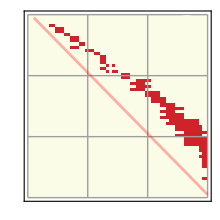
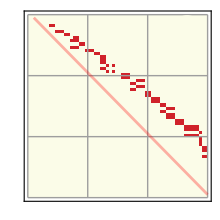
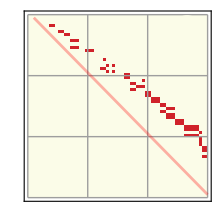
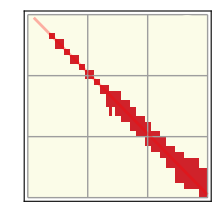
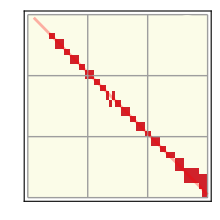
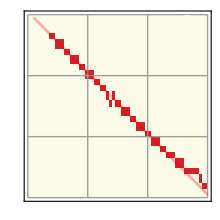
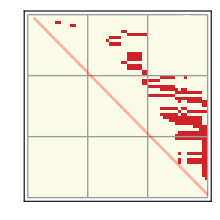
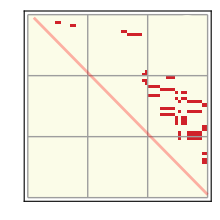
{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
labels=Partition["\\text{("<>#<>")}"&/@CharacterRange["a","z"],3];
mapfun=TubeRibbonPeakCorrelationMap[#1,Range[3],"TemperatureMap",#2,{0.2,0.5}]&;
figlist=Join[MapThread[mapfun,{lincorarrayP,labels⟦1;;2⟧}],MapThread[mapfun,{lincorarrayF,labels⟦3;;4⟧}]]
```

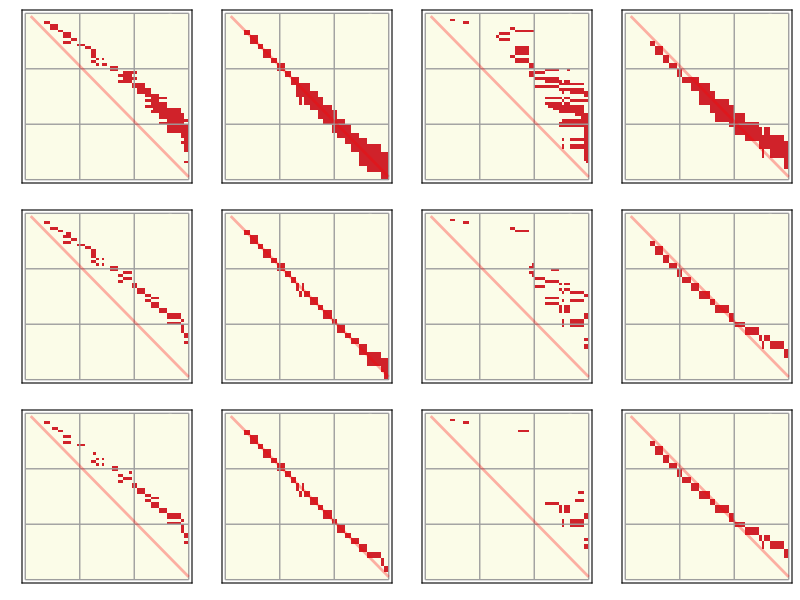

```mathematica
leftPadding=50;
rightPadding=20;
bottomPadding=50;
topPadding=20;
width=800;
height=600;
fig=MyPlotGrid[figlistᵀ,width,height,leftPadding,rightPadding,bottomPadding,topPadding]
```

```mathematica
SystemOpen[path]
```

```mathematica
path=FileNameJoin[{parentDir,"test"}];
fname="Figure_2";
Export[FileNameJoin[{path,fname<>".png"}],fig,ImageResolution-> 300];
```

[Figure 3]: Alignment coefficient based on likelihood function

Plotting functions (AlignmentArray, TubeRibbonPeakAlignmentMap)

```mathematica
(* 01/06/2019 *)
Clear[AlignmentArray]
AlignmentArray[katauraplotr_,katauraplott_,wlims_,nlims_,energyregion_]:=Module[
{
sample1,
sample2,
n,m,
lcxy
},
Table[
If[
	wind<wlims⟦1⟧||nind<nlims⟦1⟧,
	lcxy=0,
	sample1=Select[katauraplotr,(#⟦1⟧==wind&&(energyregion⟦2⟧>#⟦2⟧>energyregion⟦1⟧))&];
	sample1=sample1⟦;;,2⟧;
	sample2=Select[katauraplott,(#⟦1⟧==nind&&(energyregion⟦2⟧>#⟦2⟧>energyregion⟦1⟧))&];
	sample2=sample2⟦;;,2⟧;

	n=Length[sample1];
	m=Length[sample2];
	If[
		n==0||m==0,
		lcxy=0,
		(* likelyhood coefficient *)
		If[
			n==0||m==0,
			lcxy=0,
			lcxy=Exp[-Sum[(sample1⟦i⟧-sample2⟦i⟧)^2,{i,Min[n,m]}]/Min[n,m]]
		]
	](* end If *)
]
,{wind,wlims⟦2⟧},{nind,nlims⟦2⟧}]
](* end Module *)

(* 01/06/2019: this function is updated with cutofflist variable to produce new plots with alignment maps *)
(* 05/05/2019: this function is not universal. It is needed only to facilitate figure production *)
Clear[TubeRibbonPeakAlignmentMap]
TubeRibbonPeakAlignmentMap[alignmentarray_,irange_,colormap_,labels_,cutofflist_]:=Module[
{
ts,imagesize,
ticklen,
ticks
},
ts=MaTeX[#,FontSize->16]&;
imagesize={220,220};

ticklen={0.03,0};
ticks={#⟦1⟧,ts[#⟦2⟧],#⟦3⟧,#⟦4⟧}&/@LinTicks[0,60,20,4,MajorTickLength->ticklen,MinorTickLength->ticklen/1.7];

Table[
MatrixPlot[ImageData[Image[Binarize[Image[alignmentarray],cutofflist⟦i⟧]]],
PlotRangePadding->Scaled[0.05],
ColorFunction->ColorData["Gradients"]⟦colormap⟧,
FrameTicks->{{ticks,{#⟦1⟧,"",#⟦3⟧,#⟦4⟧}&/@ticks},{ticks,{#⟦1⟧,"",#⟦3⟧,#⟦4⟧}&/@ticks}},
FrameTicksStyle->Directive[AbsoluteThickness[1]],
FrameStyle->Directive[AbsoluteThickness[1]],
FrameLabel->ts/@{"w, \\text{ribbon}","n, \\text{tube}"},
Mesh->{{0,20,40,60},{0,20,40,60}},
Epilog->{Directive[Opacity[0.5],Red,AbsoluteThickness[2]],Line[Table[{i,-i+1+60},{i,4,60}]],
Text[ts["L_{\\mathrm{c}} >"<>ToString[cutofflist⟦i⟧]],Scaled[{0.1,0.1}],{-1,-1}],
If[i<5,{Inset[Image[alignmentarray,ImageResolution->600],Scaled[{0.8,0.8}],Scaled[{0.5,0.5}],{20,20}],

{Opacity[1],(*EdgeForm[Black],*)FaceForm[RGBColor[0.8627345000000001,0.8918285,0.820558]],Disk[{30,55},4.7]},Inset[ts[labels⟦i⟧],Scaled[{0.5,0.87}],Scaled[{0.5,0.5}]]},{Inset[Image[alignmentarray,ImageResolution->600],Scaled[{0.8,0.8}],Scaled[{0.5,0.5}],{20,20}]}]},
AspectRatio->1,
ImageSize->imagesize],
{i,irange}]

](* end Module *)
```

[Figure 3]: CNTs and ZGNRs in Reich2003 and Partoens2006 mode: Edge states removed; First peak in the tube removed (01/06/2019)

```mathematica
(*=======================================================================================*)
(* Kataura plot points ribbon: katauraplotr19May2019MyFit *)

path=FileNameJoin[{parentDir,"raw data","TB","zigzag ribbons"}];
fname="25_May_2019_data_TB_19May2019MyFit_Kataura_plot_ZGNR";
Get[fname,Path->path];
fname="26_May_2019_data_TB_19May2019MyFit_Kataura_plot_ZGNR_bulk";
Get[fname,Path->path];

(* Kataura plot points tube: katauraplottReich2002 *)
path=FileNameJoin[{parentDir,"raw data","TB","armchair tubes"}];
fname="1_Jun_2019_data_TB_Reich2002_Kataura_plot_ACNT_without_first_peak";
Get[fname,Path->path];

(*=======================================================================================*)
(* Kataura plot points ribbon: katauraplotrPartoens2006 *)
path=FileNameJoin[{parentDir,"raw data","TB","zigzag ribbons"}];
fname="25_May_2019_data_TB_Partoens2006_Kataura_plot_ZGNR";
Get[fname,Path->path];
fname="26_May_2019_data_TB_Partoens2006_Kataura_plot_ZGNR_bulk";
Get[fname,Path->path];

(* Kataura plot points tube: katauraplottPartoens2006 *)
path=FileNameJoin[{parentDir,"raw data","TB","armchair tubes"}];
fname="1_Jun_2019_data_TB_Partoens2006_Kataura_plot_ACNT_without_first_peak";
Get[fname,Path->path];

wlims={2,60};
nlims={4,60};
alignmentarrayF=AlignmentArray[katauraplotr19May2019MyFitb,katauraplottReich2002,wlims,nlims,{0,4}];
alignmentarrayP=AlignmentArray[katauraplotrPartoens2006b,katauraplottPartoens2006,wlims,nlims,{0,6}];
```

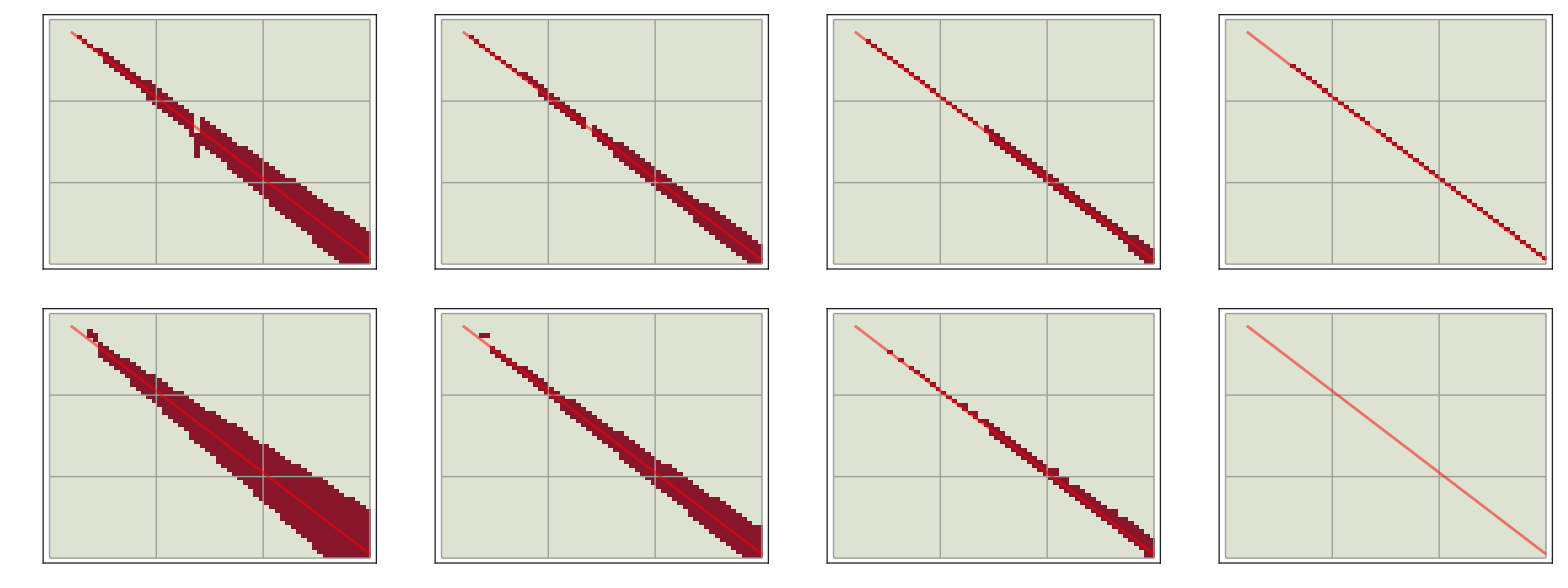

```mathematica
figlist={TubeRibbonPeakAlignmentMap[alignmentarrayP,Range[4],49,{"\\text{(a)}","\\text{(b)}","\\text{(c)}","\\text{(d)}"},{0.9,0.97,0.99,0.999}],
TubeRibbonPeakAlignmentMap[alignmentarrayF,Range[4],49,{"\\text{(e)}","\\text{(f)}","\\text{(g)}","\\text{(h)}"},{0.9,0.97,0.99,0.999}]
};

fig=Grid[figlist,Spacings->{0,0}]
```

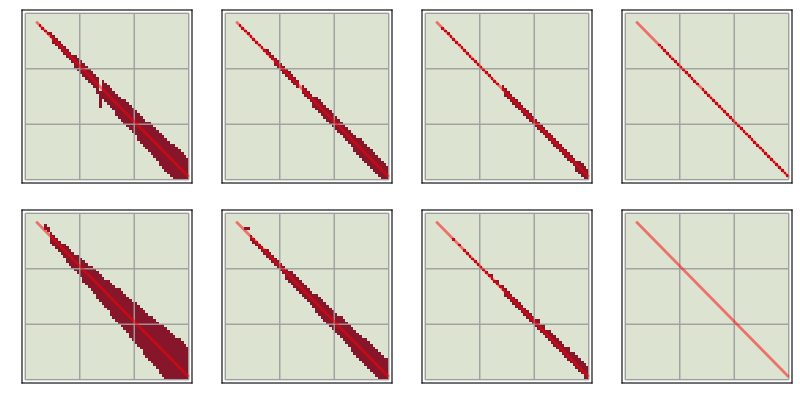

```mathematica
leftPadding=50;
rightPadding=20;
bottomPadding=50;
topPadding=20;
width=800;
height=400;
fig=MyPlotGrid[figlist,width,height,leftPadding,rightPadding,bottomPadding,topPadding]
```

```mathematica
Log[{0.90,0.97,0.99,0.999}]
```

{-0.105361,-0.0304592,-0.0100503,-0.0010005}

```mathematica
SystemOpen[path]
```

```mathematica
path=FileNameJoin[{parentDir,"test"}];
fname="Figure_3";
Export[FileNameJoin[{path,fname<>".png"}],fig,ImageResolution-> 300];
```

#### [Figure 4]: DFT vs TBM

Armchair tube decomposition into zigzag ribbons[top-right panel of Figure 4]

```mathematica
ts=MaTeX[#,FontSize->20]&;

(* ACNT(6,6) 08/12/2017 *)
quadrant[pt_]:=If[pt⟦1⟧≥0,If[pt⟦2⟧> 0,1,4],If[pt⟦2⟧≤ 0,3,2]];
imagesize=135/3{3,0.7};(* 125, 135*)

(* Nanotube picture *)
n=7;
a=2.46;

data=Nanotube[1,n,n];
tlim=8;
UnitCell=data⟦1⟧;
T=data⟦2⟧;
a0=data⟦3⟧;


Chv=√3 a n;
R=Chv/(2 π);
φ1=(3 a0)/(2 R);
φ=π-φ1;
φ0=a0/(2R);
angle=Switch[quadrant[{#1,#2}],
1,If[#1≠0,ArcTan[#2/#1],ArcTan[Infinity]],
2,π+If[#1≠0,ArcTan[#2/#1],ArcTan[Infinity]],
3,π+If[#1≠0,ArcTan[#2/#1],ArcTan[Infinity]],
4,2 π+If[#1≠0,ArcTan[#2/#1],-ArcTan[Infinity]]]&;

rQ=R φ0<R angle[#⟦1⟧,#⟦2⟧]<R (φ0+φ)&;
rrQ=R (φ0+φ+φ1)<R angle[#⟦1⟧,#⟦2⟧]<R (φ0+2 φ+φ1)&;

UnitCells=Reap[Scan[If[rQ[#],Sow[#,"a"],If[rrQ[#],Sow[#,"b"],Sow[#,"c"]]]&,UnitCell],{"a","b","c"}]⟦2⟧;
rUnitCell=UnitCells⟦1,1⟧;
rrUnitCell=UnitCells⟦2,1⟧;
rrrUnitCell=UnitCells⟦3,1⟧;

ur=Flatten[Table[#+i T&/@rUnitCell,{i,-tlim,tlim}],1];
urr=Flatten[Table[#+i T&/@rrUnitCell,{i,-tlim,tlim}],1];
urrr=Flatten[Table[#+i T&/@rrrUnitCell,{i,-tlim,tlim}],1];

(*
Graphics3D[{Red,Sphere[{0,0,0},0.4],Green,Sphere[{5,0,0},0.4],
{Blue,Sphere[rrUnitCell,0.3],Tube[BondList[rrUnitCell,a0,3],0.1]},{LightBlue,Sphere[rUnitCell,0.3],Tube[BondList[rUnitCell,a0,3],0.1]}(*MapThread[{Yellow,Text[#1,#2]}&,{list2,UnitCell}]*)}];
*)

max=(Max/@(UnitCellᵀ))⟦3⟧+tlim √(T.T);
min=(Min/@(UnitCellᵀ))⟦3⟧-tlim √(T.T);

fig1=Grid[{{ts@"\\text{(d)}",Graphics3D[{Specularity[GrayLevel[1],100],
{LightBlue,Opacity[0.7],Cylinder[{{0,0,min},{0,0,max}},R]},
{Blue,Sphere[urrr,0.3],Tube[BondListM[urrr,a0,3],0.1]},{Opacity[1],Darker[Green,0.5],Sphere[ur,0.3],Tube[BondListM[ur,a0,3],0.1]},
{Opacity[1],Darker[Magenta,0.5],Sphere[urr,0.3],Tube[BondListM[urr,a0,3],0.1]}
},Lighting->"Neutral",Boxed->False,Background->White,ImageSize->imagesize,ImageResolution->300,SphericalRegion->True,PlotRange->1.35 {{-3.690,3.690},{-3.671,3.671},0.8 {-23.066,24.296}},RotationAction->"Fit",SphericalRegion->True,TouchscreenAutoZoom->False,ViewAngle->0.07,ViewCenter->{0.5,0.5,0.5},ViewPoint->{3.0756,0.4334,1.3404},ViewRange->All,ViewVertical->{0.8456,0.5286,0.0736}]}},Spacings->0]
```

-Graphics- | -Graphics3D-

```mathematica
AbsoluteOptions[-Graphics3D-]
```

{AlignmentPoint→Center,AspectRatio→Automatic,AutomaticImageSize→False,Axes→False,AxesEdge→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→GrayLevel[1.],BaselinePosition→Automatic,BaseStyle→{},Boxed→False,BoxRatios→{0.194776,0.193773,1.},BoxStyle→{},ClipPlanes→None,ClipPlanesStyle→Automatic,ColorOutput→Automatic,ContentSelectable→Automatic,ControllerLinking→Automatic,ControllerMethod→Automatic,ControllerPath→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction→Identity,Epilog→{},FaceGrids→None,FaceGridsStyle→{},FormatType→TraditionalForm,ImageMargins→0.,ImagePadding→All,ImageSize→{278.,64.},ImageSizeRaw→Automatic,LabelStyle→{},Lighting→Neutral,Method→Automatic,PlotLabel→None,PlotRange→{{-4.9815,4.9815},{-4.95585,4.95585},{-24.9113,26.2397}},PlotRangePadding→Automatic,PlotRegion→Automatic,PreserveImageOptions→Automatic,Prolog→{},RotationAction→Fit,SphericalRegion→True,Ticks→Automatic,TicksStyle→{},TouchscreenAutoZoom→False,ViewAngle→0.08,ViewCenter→{0.5,0.5,0.5},ViewMatrix→Automatic,ViewPoint→{3.07565,0.433403,1.34049},ViewProjection→Automatic,ViewRange→All,ViewVector→Automatic,ViewVertical→{0.845666,0.528612,0.073612}}

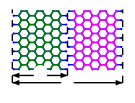

```mathematica
(* ACNT(6,6) 08/12/2017 *)
(* decomposition to ribbons *)
imagesize=135/3{3,2.3};(* 125, 135 *)
n=7;
a=2.46;

data=Nanoribbon[3,n];
tlim=3;
rm=RotationMatrix[π/2,{0,0,1}];
UnitCell=(rm.#)&/@(data⟦1⟧);
T=(rm.#)&@(data⟦2⟧);
a0=data⟦3⟧;

sft={a0/2,(√3 a0)/2,0};

u=Flatten[Table[#+i T&/@UnitCell,{i,-tlim,tlim}],1];
u0=sft+#&/@Flatten[Table[-#+i T&/@UnitCell,{i,-tlim,tlim}],1];

data=Nanoribbon[1,n-1];
tlim=3;

UnitCell=#-{-3/2 a0,(√3 a0)/2,0}&/@(data⟦1⟧);
T=(data⟦2⟧);
a0=data⟦3⟧;

u1=Flatten[Table[-#+i T&/@UnitCell,{i,-tlim,tlim}],1];
u2=sft+#&/@Flatten[Table[#+i T&/@UnitCell,{i,-tlim,tlim}],1];

xmax=Max[u⟦;;,1⟧];
xmin=Min[u⟦;;,1⟧];

rwidthar={{xmin-a0/4 ,-9.1},{xmax+a0/4,-9.1}};(* ribbon width arrow *)
as=0.07; (* arrow size *)

(* vertical dashed lines *)
line1={rwidthar⟦2⟧,{rwidthar⟦2,1⟧,-rwidthar⟦2,2⟧}};
line2={rwidthar⟦1⟧+{0,-2},{rwidthar⟦1,1⟧,-rwidthar⟦1,2⟧}};
line3={{(2 rwidthar⟦2,1⟧-rwidthar⟦1,1⟧),rwidthar⟦1,2⟧}+{0,-2},{(2 rwidthar⟦2,1⟧-rwidthar⟦1,1⟧),-rwidthar⟦1,2⟧}};

tcircumar={line2⟦1⟧,line3⟦1⟧};(* tube circumference arrow *)

fig2=Graphics[
{
{Blue,Disk[Most@#,0.3]&/@u,Line[BondListM[u,a0,2]]},
{Darker[Green,0.5],Disk[Most@#,0.3]&/@u1,Line[BondListM[u1,a0,2]]},
{Blue,Disk[Most@#,0.3]&/@u0,Line[BondListM[u0,a0,2]]},
{Magenta,Disk[Most@#,0.3]&/@u2,Line[BondListM[u2,a0,2]]},
(* Arrows *)
{Directive[AbsoluteThickness[1]],Arrowheads[{-as,as}],Arrow[rwidthar],Arrow[tcircumar]},
{Dashed,Black,AbsoluteThickness[1],Line[{line1,line2,line3}]},
{
{
White,EdgeForm[None],
Disk[(tcircumar⟦1⟧+tcircumar⟦2⟧)/2+{0,-1},2],
Disk[(rwidthar⟦1⟧+rwidthar⟦2⟧)/2+{0,1},2]
},
Black,
Text[Grid[{{MaTeX["C","FontSize"->14]}},Background->None],(tcircumar⟦1⟧+tcircumar⟦2⟧)/2+{0,-1}],
Text[Grid[{{MaTeX["\\mathcal{W}","FontSize"->14]}},Background->None],(rwidthar⟦1⟧+rwidthar⟦2⟧)/2+{0,0.5}]
}
},Background->GrayLevel[1.],ImageSize->imagesize]
```

```mathematica
fig=Column[{fig1,fig2},Alignment->Center,Frame->None,Background->White]
```

-Graphics- | -Graphics3D-
-Graphics-

[Figure 4]: LCC and AC for CNT(21,21) and ZGNR(20) (26/05/2019)

```mathematica
(* DFT data *)
(* zgnr20data *)
sample1 = {{1,1.4785},{2,2.1185},{3,2.6775},{4,3.1355},{5,3.4785},{6,3.7515},{7,3.9165},{8,3.9985},{9,4.0615}};
(* cnt21data *)
sample2 = {{1,1.4965},{2,2.1375},{3,2.6715},{4,3.1095},{5,3.4535},{6,3.7045},{7,3.8795},{8,3.9915},{9,4.0455}};

sample1=sample1⟦;;,2⟧
sample2=sample2⟦;;,2⟧

AC=AlignmentCoef[sample1,sample2]
LCC=LinearCorrelationCoef[sample1,sample2]
```

{1.4785,2.1185,2.6775,3.1355,3.4785,3.7515,3.9165,3.9985,4.0615}

{1.4965,2.1375,2.6715,3.1095,3.4535,3.7045,3.8795,3.9915,4.0455}

0.999344

0.999871

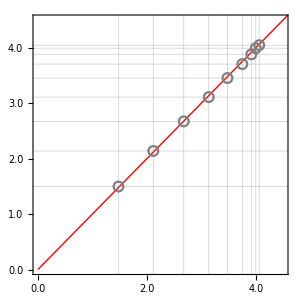

```mathematica
imagesize=300;
imagepadding={{70,2},{70,2}};
ts=MaTeX[#,FontSize->20]&;
tss=Style[#,FontSize->18,FontColor->Black]&;

tsss=MaTeX[#,FontSize->16]&;
lb=tsss[{"\\text{DFT}","\\text{TB:}","\\text{ bulk}","\\text{ full}"}];


lim=5;
pmax=4.5;(* plot max *)

ticklen=0.025;
ticks=LinTicks[0,lim,1,5,MinorTickLength->ticklen/2,MajorTickLength->ticklen,TickLabelFunction-> (tss[ToString@PaddedForm[#,{2,1}]]&),TickDirection->In];
ticks2=LinTicks[0,lim,1,5,MinorTickLength->ticklen/2,MajorTickLength->ticklen,ShowTickLabels->False];
polygon={{sample1⟦1⟧,sample2⟦1⟧},{sample1⟦1⟧,pmax},{pmax,pmax},{pmax,sample2⟦1⟧}};

imsz=33;
legend=Grid[{
{
lb⟦1⟧,
Graphics[{LightGray,EdgeForm[Directive[AbsoluteThickness[1],Black]],Rectangle[{0,0},{2,1}]},ImageSize->imsz]
},
{
lb⟦2⟧,
},
{
lb⟦3⟧,Graphics[{LightRed,EdgeForm[Directive[AbsoluteThickness[1],Black]],Rectangle[{0,0},{2,1}]},ImageSize->imsz]
},
{
lb⟦4⟧,Graphics[{White,EdgeForm[Directive[AbsoluteThickness[2],Black,Dashed]],Rectangle[{0,0},{2,1}]},ImageSize->imsz]
}
},Frame->True,FrameStyle->Black,Background->White,Alignment->Left];

p=ListPlot[MapThread[{#1,#2}&,{sample1,sample2}],PlotRange->{{0,pmax},{0,pmax}},PlotMarkers->Graphics[{Gray,Circle[]},ImageSize->10],
Axes->False,
Frame->True,
FrameStyle->Directive[AbsoluteThickness[1]],
FrameLabel->ts[{"\\text{ribbon peak energy, eV}","\\text{tube peak energy, eV}"}],
FrameTicks->{{ticks,ticks2},{ticks,ticks2}},
FrameTicksStyle->Directive[AbsoluteThickness[1]],
GridLines->{sample1,sample2},
Prolog->{Red,Line[Table[{i,i},{i,0,5,0.01}]],
Inset[ts@"\\text{(c)}",Scaled[{0.08,0.92}],Background->White]
},AspectRatio->1,
ImagePadding->imagepadding,
ImageSize->imagesize]
```

```mathematica
(* 26/05/2019:  this function is used only to facilitate plotting *)
Clear[readDFTspectrum];
readDFTspectrum[path_,fname_]:=Module[
{
data,
fun,
data2plot,
max
},
data=ReadList[FileNameJoin[{path,fname}],Word,RecordLists->True];
fun=Read[StringToStream[#],Real]&;

data2plot=(fun/@{#⟦1⟧,#⟦2⟧})&/@data;
max=Max[data2plot⟦;;,2⟧];
data2plot={#⟦1⟧,(#⟦2⟧)/max}&/@data2plot;
Chop[data2plot,10^-3]
]


(* 26/05/2019: this function is usedto read TB spectra from files; abdata variable only *)
Clear[readTBspectrum];
readTBspectrum[path_,fname_]:=Module[
{
max,data2plot
},
(* reading absorption spectrum from file *)
Get[fname,Path->path];

(* normalizing the spectrum *)
max=Max[abdata⟦;;,2⟧];
data2plot={#⟦1⟧,(#⟦2⟧)/max}&/@abdata;

Chop[data2plot,10^-3]
]
```

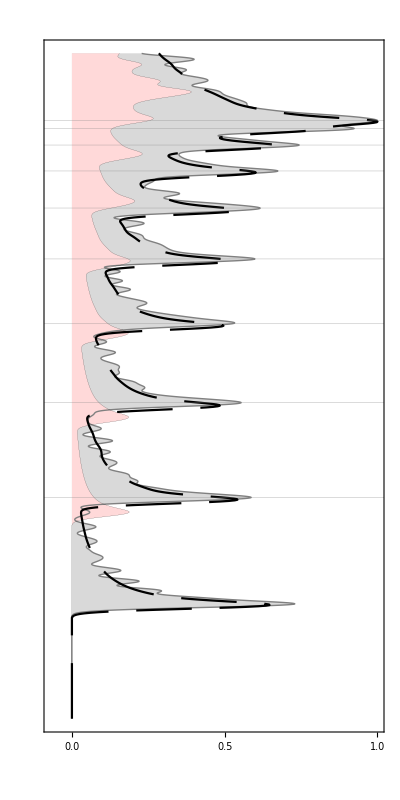

```mathematica
(* CNT(21,21) absorption specturm plotting *)
imagepadding={{2,15},{70,2}};
imagesize={Automatic,300};
ts=MaTeX[#,FontSize->20]&;
tss=Style[#,FontSize->18,FontColor->Black]&;
lim=5;
pmax=4.5;(* plot max *)


(*--------------------------- getting tspectrum from file------------------------------------------------ *)
(* 08/02/2019 *)
path=FileNameJoin[{parentDir,"raw data","DFT","CNT(21,21)"}];
fname="absorption parallel polarization.dat";
tDFTspectrum=readDFTspectrum[path,fname];
(*------------------------------------------------------------------------------------------------------*)


(*--------------------------- reading TB spectrum from file -----------------------------------------------*)
path=FileNameJoin[{parentDir,"raw data","TB","armchair tubes","2019_05_22_Reich2002"}];
fname="22_May_2019_CNT(21,21)_absorption_TB_0_8_np2000";
tTBspectrum=readTBspectrum[path,fname];
max=Max[abdata⟦;;,2⟧];

(*------------------------- reading TB bulk ribbon spectrum from file --------------------------------------------*)
path=path=FileNameJoin[{parentDir,"raw data","TB","zigzag ribbons","2019_05_26_My_averaged_fit_bulk"}];
fname="26_May_2019_ZGNR(20)_absorption_bulk_TB_0_8_np2000";
(* reading absorption spectrum from file *)
Get[fname,Path->path];
rTBbulkspectrum=Chop[{#⟦1⟧,(#⟦2⟧)/max}&/@abdata,10^-3];

xticklen=0.05;
xticks={LinTicks[0,1,0.5,5,MinorTickLength->xticklen/2,MajorTickLength->xticklen,TickLabelFunction-> (tss@ToString@PaddedForm[#,{2,1}]&),TickDirection->In,ShowFirst->True],
LinTicks[0,1,0.5,5,MinorTickLength->xticklen/2,MajorTickLength->xticklen,ShowTickLabels->False]};
yticklen=0.05;
yticks={LinTicks[0,lim,1,5,MinorTickLength->yticklen/2,MajorTickLength->yticklen,ShowTickLabels->False],LinTicks[0,lim,1,5,MinorTickLength->yticklen/2,MajorTickLength->yticklen,ShowTickLabels->False]};


tplot=ListLinePlot[{Reverse/@tDFTspectrum,Reverse/@tTBspectrum,Reverse/@rTBbulkspectrum},
PlotRange->{{-0.07,1},{0,pmax}},
PlotStyle->{Directive[AbsoluteThickness[1],Gray],Directive[Black,Dashing[{0.1,0.05}]],Directive[AbsoluteThickness[0.1],Black]},
Filling->{1->{pmax,LightGray},3->{pmax,LightRed}},
Axes->False,
Frame->True,
FrameStyle->Directive[AbsoluteThickness[1]],
FrameTicks->{yticks,xticks},
FrameTicksStyle->Directive[AbsoluteThickness[1]],
FrameLabel->ts/@{"A(\\hbar \\omega)",None},
Epilog->{(*Text[ts@"\\text{SWCNT(21,21)}",{0.65,pmax/2},{60,0},{0,-1}],*)
Inset[ts@"\\text{(b)}",Scaled[{0.14,0.92}],Background->None]},
GridLines->{None,sample2},
AspectRatio->2,
ImagePadding->imagepadding,
ImageSize->{Automatic,300}]
```

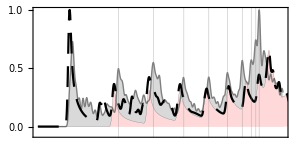

```mathematica
(* ZGNR20 absorption spectrum plotting *)
imagepadding={{70,2},{2,10}};
imagesize={300,Automatic};
ts=MaTeX[#,FontSize->20]&;
tss=Style[#,FontSize->18,FontColor->Black]&;
lim=5;
pmax=4.5;(* plot max *)


(*----------------------------- getting rspectrum form the file -----------------------------------*)
(* 08/02/2019 *)
path=FileNameJoin[{parentDir,"raw data","DFT","ZGNR_20"}];
fname="absorption parallel polarization.dat";
rDFTspectrum=readDFTspectrum[path,fname];
(*---------------------------------------------------------------------------------------------*)

(*--------------------------- reading TB spectrum from file -----------------------------------------------*)
path=FileNameJoin[{parentDir,"raw data","TB","zigzag ribbons","2019_05_21_My_averaged_fit"}];
fname="21_May_2019_ZGNR(20)_absorption_TB_0_8_np2000";
rTBspectrum=readTBspectrum[path,fname];
max=Max[abdata⟦;;,2⟧];

(*------------------------- reading TB bulk ribbon spectrum from file --------------------------------------------*)
path=FileNameJoin[{parentDir,"raw data","TB","zigzag ribbons","2019_05_26_My_averaged_fit_bulk"}];
fname="26_May_2019_ZGNR(20)_absorption_bulk_TB_0_8_np2000";
(* reading absorption spectrum from file *)
Get[fname,Path->path];
rTBbulkspectrum=Chop[{#⟦1⟧,(#⟦2⟧)/max}&/@abdata,10^-3];



xticklen=0.025;
xticks={LinTicks[0,lim,1,5,MinorTickLength->xticklen/2,MajorTickLength->xticklen,ShowTickLabels->False,TickDirection->In],
LinTicks[0,lim,1,5,MinorTickLength->xticklen/2,MajorTickLength->xticklen,ShowTickLabels->False,TickDirection->In]};
yticklen=0.025;
yticks={LinTicks[0,1,0.5,5,MinorTickLength->yticklen/2,MajorTickLength->yticklen,TickLabelFunction-> (tss[ToString@PaddedForm[#,{2,1}]]&),TickDirection->In,ShowFirst->True],LinTicks[0,1,0.5,5,MinorTickLength->yticklen/2,MajorTickLength->yticklen,ShowTickLabels->False,TickDirection->In]};


rplot=ListLinePlot[{rDFTspectrum,rTBspectrum,rTBbulkspectrum},
PlotRange->{{0,pmax},{-0.07,1}},
PlotStyle->{Directive[AbsoluteThickness[1],Gray],Directive[Black,Dashing[{0.05,0.03}]],Directive[AbsoluteThickness[0.1],Black]},
Filling->{1->{Axis,LightGray},{3->{Axis,LightRed}}},
Axes->False,
Frame->True,
FrameStyle->Directive[AbsoluteThickness[1]],
FrameTicks->{yticks,xticks},
FrameTicksStyle->Directive[AbsoluteThickness[1]],
FrameLabel->ts/@{None,"A(\\hbar \\omega)"},
Epilog->{(*Text[ts@"\\text{ZGNR(20)}",{pmax/2,0.65},{40,0},{1,0}]*)
Inset[ts@"\\text{(a)}",Scaled[{0.065,0.85}],Background->None]},
GridLines->{sample1,None},
AspectRatio->1/2,
ImagePadding->imagepadding,
ImageSize->imagesize]
```

Evaluate Section “Armchair tube decomposition into zigzag ribbons[top-right panel of Figure 4]” to get ‘fig’ variable before proceeding to the next cell

```mathematica
figg=Grid[{{rplot,fig},
{p,tplot}},Spacings->{0,0},Frame->False]
```

-Graphics- | -Graphics- | -Graphics3D-
-Graphics-
-Graphics- | -Graphics-

```mathematica
SystemOpen[path]
```

```mathematica
path=FileNameJoin[{parentDir,"test"}];
fname="Figure_4";
Export[FileNameJoin[{path,fname<>".png"}],figg,ImageResolution-> 600];
```

#### [Figure 5, Supplementary Figure 7, Supplementary Figure 8]: Mapping armchair SWCNTs optical resonances to the resonances of ZGNRs

[Supplementary Figure 7]: Linear and non-linear model fits

Data processing functions (02/06/2019)(TubeAndRibbonAlignedPeaks, AlignmentCoef, LinearCorrelationCoef)

```mathematica
Clear[TubeAndRibbonAlignedPeaks];
TubeAndRibbonAlignedPeaks[path2readTube_,path2readRibbon_,chiralindex_,widthindex_,tubepeakspec_,ribbonpeakspec_]:=Module[
{
flistTube,
flistRibbon,

fnameTube,
fnameRibbon,

max,
data2plot,
spectrumTube,
spectrumRibbon,
peaksTube,
peaksRibbon
},

SetDirectory[path2readTube];
flistTube=FileNames[];
fnameTube=Select[flistTube,StringMatchQ[#,__~~"CNT("<>ToString[chiralindex]<>","<>ToString[chiralindex]<>")"~~__]&]⟦1⟧;

SetDirectory[path2readRibbon];
flistRibbon=FileNames[];
fnameRibbon=Select[flistRibbon,StringMatchQ[#,__~~"ZGNR("<>ToString[widthindex]<>")"~~__]&]⟦1⟧;

(* reading absorption spectrum from file; tube *)
Get[fnameTube,Path->path2readTube];
(*Print[nn];*)
(* normalizing the spectrum *)
max=Max[abdata⟦;;,2⟧];
data2plot={#⟦1⟧,(#⟦2⟧)/max}&/@abdata;
spectrumTube=Chop[data2plot,10^-3];

(* reading absorption spectrum from file; ribbon *)
Get[fnameRibbon,Path->path2readRibbon];
(*Print[w];*)
(* normalizing the spectrum *)
data2plot={#⟦1⟧,(#⟦2⟧)/max}&/@abdata;
spectrumRibbon=Chop[data2plot,10^-3];


peaksTube=FindPeaksInSpectrum20190217[spectrumTube,tubepeakspec⟦1⟧,tubepeakspec⟦2⟧];
peaksTube=Select[peaksTube,#⟦1⟧<6.3&];

(* bulk transitions *)
peaksRibbon=FindPeaksInSpectrum20190217[spectrumRibbon,ribbonpeakspec⟦1⟧,ribbonpeakspec⟦2⟧];
peaksRibbon=Select[peaksRibbon,#⟦1⟧<6.3&];

{{spectrumTube,peaksTube,Rest[peaksTube⟦;;,1⟧]},{spectrumRibbon,peaksRibbon,peaksRibbon⟦;;,1⟧}}

](* end Module *)

Clear[AlignmentCoef];
AlignmentCoef[sample1_,sample2_]:=Module[
{
n,m,
lcxy
},
n=Length[sample1];
m=Length[sample2];
If[
	n==0||m==0,
	lcxy=0,
	(* likelyhood coefficient *)
	If[
		n==0||m==0,
		lcxy=0,
		lcxy=Exp[-Sum[(sample1⟦i⟧-sample2⟦i⟧)^2,{i,Min[n,m]}]/Min[n,m]]
	]
](* end If *)
](* end Module *)

Clear[LinearCorrelationCoef];
LinearCorrelationCoef[sample1_,sample2_]:=Module[
{
n,m,
rxy,

xm,ym,
demX,demY

},
n=Length[sample1];
m=Length[sample2];
If[
	n==0||m==0,
	rxy=0,
	xm=Total[sample1]/n;
	ym=Total[sample2]/m;
	demX=Chop@√Sum[(sample1⟦i⟧-xm)^2,{i,n}];
	demY=Chop@√Sum[(sample2⟦i⟧-ym)^2,{i,m}];
	(* correlation coefficient *)
	If[
		demX==0|| demY==0,
		rxy=0,
		rxy=Sum[(sample1⟦i⟧-xm) (sample2⟦i⟧-ym),{i,Min[n,m]}]/(demX demY)
	]
](* end If *)
](* end Module *)
```

[Supplementary Figure 7 (a,b) variables p1,p2]: For tube Partoens2006  and bulk ribbon Partoens2006 absorption peaks (02/06/2019)

```mathematica
path2readTube=FileNameJoin[{parentDir,"raw data","TB","armchair tubes","2019_05_22_Partoens2006"}];
path2readRibbon=FileNameJoin[{parentDir,"raw data","TB","zigzag ribbons","2019_05_26_Partoens2006_bulk"}];

tubepeakspec={0.1,0.19};
ribbonpeakspec={0.07,0.08};

baflist=Table[
chiralindex=i;
widthindex=chiralindex-1;

data=TubeAndRibbonAlignedPeaks[path2readTube,path2readRibbon,chiralindex,widthindex,tubepeakspec,ribbonpeakspec];

sample1=data⟦1,3⟧; (* tube *)
sample2=data⟦2,3⟧; (* ribbon *)

n=Min[Length[sample1],Length[sample2]];
data2fit=MapThread[{#1,#2}&,{sample1⟦1;;n⟧,sample2⟦1;;n⟧}];
lm=LinearModelFit[data2fit,x,x];

Join[{chiralindex,#}&/@lm["BestFitParameters"],{lm["Function"]}]
,{i,7,60}];

(* b+a*x *)
blist=baflist⟦;;,1⟧
alist=baflist⟦;;,2⟧
```

{{7,-0.153182},{8,-0.141525},{9,-0.102209},{10,-0.09932},{11,-0.0787786},{12,-0.0656353},{13,-0.0598783},{14,-0.0532785},{15,-0.053234},{16,-0.0452028},{17,-0.0399486},{18,-0.0371228},{19,-0.0331591},{20,-0.0319907},{21,-0.0274082},{22,-0.0289042},{23,-0.0237302},{24,-0.025239},{25,-0.0186888},{26,-0.0212535},{27,0.0000282335},{28,0.73552},{29,-0.0156552},{30,-0.0161418},{31,-0.0146856},{32,0.00385534},{33,-0.0128362},{34,0.00111724},{35,-0.0154773},{36,-0.0117422},{37,0.00917209},{38,-0.0138662},{39,0.00713784},{40,0.0115729},{41,0.0222181},{42,0.0105144},{43,0.0185477},{44,0.00645011},{45,0.0152026},{46,0.0197516},{47,0.00851694},{48,0.0184058},{49,0.0215022},{50,0.01376},{51,0.0205846},{52,0.0263665},{53,0.0171113},{54,0.0210342},{55,0.0260608},{56,0.0356895},{57,0.0405602},{58,0.029323},{59,0.0204171},{60,0.024315}}

{{7,1.01316},{8,1.01466},{9,1.00958},{10,1.01069},{11,1.00831},{12,1.00726},{13,1.00654},{14,1.00593},{15,1.00628},{16,1.00522},{17,1.005},{18,1.00455},{19,1.00405},{20,1.00433},{21,1.00349},{22,1.00402},{23,1.00287},{24,1.00348},{25,1.00215},{26,1.00296},{27,0.996069},{28,0.921503},{29,1.00212},{30,1.00225},{31,1.00187},{32,0.995729},{33,1.00172},{34,0.996758},{35,1.00247},{36,1.00162},{37,0.994322},{38,1.00197},{39,0.995463},{40,0.993401},{41,0.989947},{42,0.994297},{43,0.991507},{44,0.995597},{45,0.992854},{46,0.99089},{47,0.994892},{48,0.991839},{49,0.990202},{50,0.993369},{51,0.990981},{52,0.988754},{53,0.992271},{54,0.990589},{55,0.98847},{56,0.985568},{57,0.98333},{58,0.987885},{59,0.990972},{60,0.989402}}

FittedModel[0.0448097-1.45134/x]

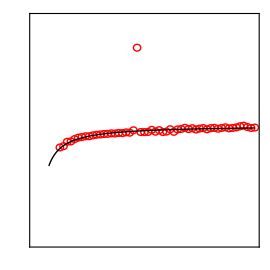

```mathematica
(* ListPlot parameters *)
ts=MaTeX[#,FontSize->20]&;
tss=MaTeX[#,FontSize->18]&;
imagesize=270;
imagepadding={{75,10},{60,10}};


Clear[α,β];
bblist=Delete[Drop[blist,3],19];
bnlm=NonlinearModelFit[bblist,α/x+β,{α,β},x]

ticklen={0.03,0};
yticklen={0.03,0};
xticks={#⟦1⟧,ts[#⟦2⟧],#⟦3⟧,#⟦4⟧}&/@LinTicks[0,60,20,4,MajorTickLength->ticklen,MinorTickLength->ticklen/1.7];
yticks=LinTicks[-1,1,0.5,5,MajorTickLength->yticklen,MinorTickLength->yticklen/1.7,TickLabelFunction->(ts[PaddedForm[#,{2,1}]]&)];


p1=Plot[bnlm[x],{x,4,60},
PlotRange->{{0,60},{-1,1}},
PlotStyle->Directive[AbsoluteThickness[1],Black],
PlotRangePadding->Scaled[0.04],
Prolog->{Red,Circle[#,{1,0.03}]&/@blist},
Axes->False,
Frame->True,
FrameLabel->tss/@{"n, \\text{diameter index}","b_{\\text{P}}(n) \\text{, eV}"},
FrameStyle->Directive[AbsoluteThickness[1],Black],
FrameTicks->{{yticks,{#⟦1⟧,,#⟦3⟧,#⟦4⟧}&/@yticks},{xticks,{#⟦1⟧,,#⟦3⟧,#⟦4⟧}&/@xticks}},
FrameTicksStyle->Directive[AbsoluteThickness[1],Black],
Epilog->{Inset[ts["\\text{(b)}"],Scaled[{0.55,0.87}],Scaled[{0.5,0.5}]]},
AspectRatio->1,
ImagePadding->imagepadding,
ImageSize->imagesize]
```

FittedModel[0.987621+0.278462/x]

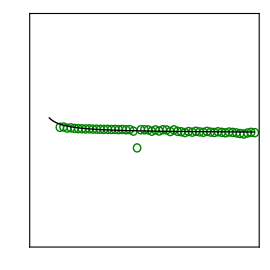

```mathematica
(* ListPlot parameters *)
ts=MaTeX[#,FontSize->20]&;
tss=MaTeX[#,FontSize->18]&;
imagesize=270;
imagepadding={{75,10},{60,10}};


Clear[α,β];
aalist=Delete[Drop[alist,3],19];
anlm=NonlinearModelFit[aalist,α/x+β,{α,β},x]

ticklen={0.03,0};
yticklen={0.03,0};
xticks={#⟦1⟧,ts[#⟦2⟧],#⟦3⟧,#⟦4⟧}&/@LinTicks[0,60,20,4,MajorTickLength->ticklen,MinorTickLength->ticklen/1.7];
yticks=LinTicks[0.5,1.5,0.5,10,MajorTickLength->yticklen,MinorTickLength->yticklen/1.7,TickLabelFunction->(ts[PaddedForm[#,{2,1}]]&)];


p2=Plot[anlm[x],{x,4,60},
PlotRange->{{0,60},{0.5,1.5}},
PlotStyle->Directive[AbsoluteThickness[1],Black],
PlotRangePadding->Scaled[0.035],
Prolog->{Darker[Green,0.5],Circle[#,{1,0.018}]&/@alist},
Axes->False,
Frame->True,
FrameLabel->tss/@{"n, \\text{diameter index}","a_{\\text{P}}(n)"},
FrameStyle->Directive[AbsoluteThickness[1],Black],
FrameTicks->{{yticks,{#⟦1⟧,,#⟦3⟧,#⟦4⟧}&/@yticks},{xticks,{#⟦1⟧,,#⟦3⟧,#⟦4⟧}&/@xticks}},
FrameTicksStyle->Directive[AbsoluteThickness[1],Black],
Epilog->{Inset[ts["\\text{(a)}"],Scaled[{0.5,0.87}],Scaled[{0.5,0.5}]]},
AspectRatio->1,
ImagePadding->imagepadding,
ImageSize->imagesize]
```

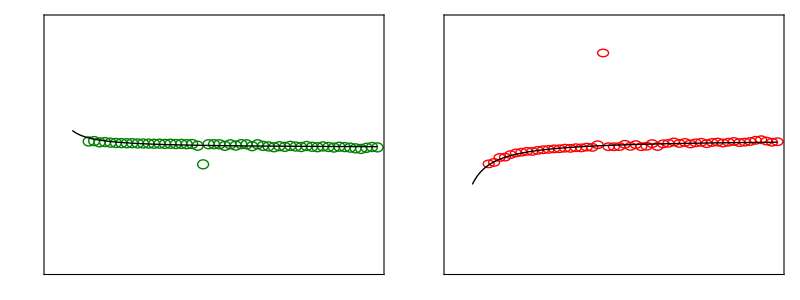

```mathematica
fig1=Grid[{{p2,p1}}]
```

```mathematica
SystemOpen[path]
```

```mathematica
path=FileNameJoin[{parentDir,"test"}];
fname="Figure_S7ab";
Export[FileNameJoin[{path,fname<>".png"}],fig1,ImageResolution-> 300];
```

```mathematica
bnlm["BestFitParameters"]
anlm["BestFitParameters"]
{αb,βb}=bnlm["BestFitParameters"]⟦;;,2⟧
{αa,βa}=anlm["BestFitParameters"]⟦;;,2⟧
```

{α→-1.45134,β→0.0448097}

{α→0.278462,β→0.987621}

{-1.45134,0.0448097}

{0.278462,0.987621}

[Supplementary Figure 7 (c,d) variables p3,p4]: For tube Reich2003  and bulk ribbon 19May2019MyFit absorption peaks (02/06/2019)

```mathematica
path2readTube=FileNameJoin[{parentDir,"raw data","TB","armchair tubes","2019_05_22_Reich2002"}];
path2readRibbon=FileNameJoin[{parentDir,"raw data","TB","zigzag ribbons","2019_05_26_My_averaged_fit_bulk"}];

tubepeakspec={0.05,0.07};
ribbonpeakspec={0.1,0.04};

baflist=Table[
chiralindex=i;
widthindex=chiralindex-1;

data=TubeAndRibbonAlignedPeaks[path2readTube,path2readRibbon,chiralindex,widthindex,tubepeakspec,ribbonpeakspec];

sample1=data⟦1,3⟧; (* tube *)
sample2=data⟦2,3⟧; (* ribbon *)

n=Min[Length[sample1],Length[sample2]];
data2fit=MapThread[{#1,#2}&,{sample1⟦1;;n⟧,sample2⟦1;;n⟧}];
lm=LinearModelFit[data2fit,x,x];

Join[{chiralindex,#}&/@lm["BestFitParameters"],{lm["Function"]}]
,{i,6,60}];

(* b+a*x *)
blist=baflist⟦;;,1⟧
alist=baflist⟦;;,2⟧
```

{{6,3.08525},{7,3.02273},{8,0.678314},{9,-0.312029},{10,-0.663325},{11,-0.609105},{12,-0.675874},{13,-0.503072},{14,-0.419747},{15,-0.449479},{16,-0.386125},{17,-0.480353},{18,-0.351725},{19,-0.344091},{20,-0.345106},{21,-0.318011},{22,-0.400134},{23,-0.307675},{24,-0.288306},{25,-0.2892},{26,-0.27219},{27,-0.259063},{28,-0.260621},{29,-0.251632},{30,-0.207715},{31,-0.183467},{32,-0.231225},{33,-0.186505},{34,-0.222307},{35,-0.191209},{36,-0.171039},{37,-0.152393},{38,-0.136602},{39,-0.158678},{40,-0.142977},{41,-0.162607},{42,-0.152093},{43,-0.136484},{44,-0.123632},{45,-0.140755},{46,-0.128468},{47,-0.113898},{48,-0.103721},{49,-0.0918996},{50,-0.113321},{51,-0.129364},{52,-0.0910227},{53,-0.0789722},{54,-0.0987131},{55,-0.087468},{56,-0.0801138},{57,-0.0703572},{58,-0.0594978},{59,-0.0782828},{60,-0.0693654}}

{{6,0.195122},{7,0.130435},{8,0.663143},{9,0.980053},{10,1.23245},{11,1.21617},{12,1.24248},{13,1.18235},{14,1.15264},{15,1.16499},{16,1.14097},{17,1.1806},{18,1.13001},{19,1.12734},{20,1.12977},{21,1.11905},{22,1.15621},{23,1.1158},{24,1.10868},{25,1.11006},{26,1.1037},{27,1.09854},{28,1.09977},{29,1.0963},{30,1.0761},{31,1.06467},{32,1.08849},{33,1.06732},{34,1.08591},{35,1.07042},{36,1.06123},{37,1.05207},{38,1.04392},{39,1.05544},{40,1.04823},{41,1.05872},{42,1.05277},{43,1.04493},{44,1.03825},{45,1.04799},{46,1.04189},{47,1.03454},{48,1.02892},{49,1.02219},{50,1.03378},{51,1.04284},{52,1.022},{53,1.01557},{54,1.02681},{55,1.02061},{56,1.01577},{57,1.01065},{58,1.00449},{59,1.01565},{60,1.01074}}

FittedModel[0.0347281-7.42347/x]

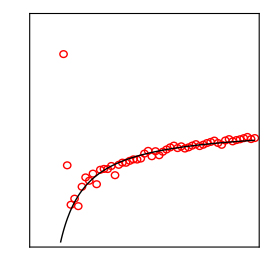

```mathematica
(* ListPlot parameters *)
ts=MaTeX[#,FontSize->20]&;
tss=MaTeX[#,FontSize->18]&;
imagesize=270;
imagepadding={{75,10},{60,10}};


Clear[α,β]
bnlm=NonlinearModelFit[Drop[blist,4],α/x+β,{α,β},x]

ticklen={0.03,0};
yticklen={0.03,0};
xticks={#⟦1⟧,ts[#⟦2⟧],#⟦3⟧,#⟦4⟧}&/@LinTicks[0,60,20,4,MajorTickLength->ticklen,MinorTickLength->ticklen/1.7];
yticks=LinTicks[-1,1,0.5,5,MajorTickLength->yticklen,MinorTickLength->yticklen/1.7,TickLabelFunction->(ts[PaddedForm[#,{2,1}]]&)];


p3=Plot[bnlm[x],{x,4,60},
PlotRange->{{0,60},{-1,1}},
PlotStyle->Directive[AbsoluteThickness[1],Black],
PlotRangePadding->Scaled[0.04],
Prolog->{Red,Circle[#,{1,0.03}]&/@blist},
Axes->False,
Frame->True,
FrameLabel->tss/@{"n, \\text{diameter index}","b_{\\text{R}}(n) \\text{, eV}"},
FrameStyle->Directive[AbsoluteThickness[1],Black],
FrameTicks->{{yticks,{#⟦1⟧,,#⟦3⟧,#⟦4⟧}&/@yticks},{xticks,{#⟦1⟧,,#⟦3⟧,#⟦4⟧}&/@xticks}},
FrameTicksStyle->Directive[AbsoluteThickness[1],Black],
Epilog->{Inset[ts["\\text{(d)}"],Scaled[{0.5,0.87}],Scaled[{0.5,0.5}]]},
AspectRatio->1,
ImagePadding->imagepadding,
ImageSize->270]
```

FittedModel[0.980033+2.82516/x]

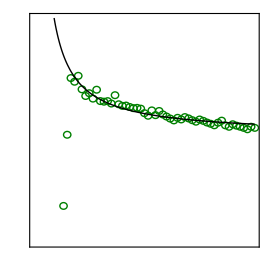

```mathematica
(* ListPlot parameters *)
ts=MaTeX[#,FontSize->20]&;
tss=MaTeX[#,FontSize->18]&;
imagesize=270;
imagepadding={{75,10},{60,10}};


Clear[α,β]
anlm=NonlinearModelFit[Drop[alist,4],α/x+β,{α,β},x]

ticklen={0.03,0};
yticklen={0.03,0};
xticks={#⟦1⟧,ts[#⟦2⟧],#⟦3⟧,#⟦4⟧}&/@LinTicks[0,60,20,4,MajorTickLength->ticklen,MinorTickLength->ticklen/1.7];
yticks=LinTicks[0.5,1.5,0.5,10,MajorTickLength->yticklen,MinorTickLength->yticklen/1.7,TickLabelFunction->(ts[PaddedForm[#,{2,1}]]&)];


p4=Plot[anlm[x],{x,4,60},
PlotRange->{{0,60},{0.5,1.5}},
PlotStyle->Directive[AbsoluteThickness[1],Black],
PlotRangePadding->Scaled[0.035],
Prolog->{Darker[Green,0.5],Circle[#,{1,0.034/2.3}]&/@alist},
Axes->False,
Frame->True,
FrameLabel->tss/@{"n, \\text{diameter index}","a_{\\text{R}}(n)"},
FrameStyle->Directive[AbsoluteThickness[1],Black],
FrameTicks->{{yticks,{#⟦1⟧,,#⟦3⟧,#⟦4⟧}&/@yticks},{xticks,{#⟦1⟧,,#⟦3⟧,#⟦4⟧}&/@xticks}},
FrameTicksStyle->Directive[AbsoluteThickness[1],Black],
Epilog->{Inset[ts["\\text{(c)}"],Scaled[{0.5,0.87}],Scaled[{0.5,0.5}]]},
AspectRatio->1,
ImagePadding->imagepadding,
ImageSize->imagesize]
```

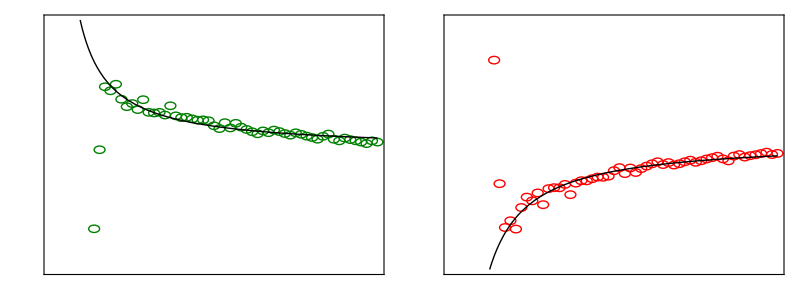

```mathematica
fig=Grid[{{p4,p3}}]
```

```mathematica
SystemOpen[path]
```

```mathematica
path=FileNameJoin[{parentDir,"test"}];
fname="Figure_S7cd";
Export[FileNameJoin[{path,fname<>".png"}],fig,ImageResolution-> 300];
```

```mathematica
bnlm["BestFitParameters"]
anlm["BestFitParameters"]
{αb,βb}=bnlm["BestFitParameters"]⟦;;,2⟧
{αa,βa}=anlm["BestFitParameters"]⟦;;,2⟧
```

{α→-7.42347,β→0.0347281}

{α→2.82516,β→0.980033}

{-7.42347,0.0347281}

{2.82516,0.980033}

[Supplementary Figure 7]: Linear fitting: Summary  (15/06/2019)

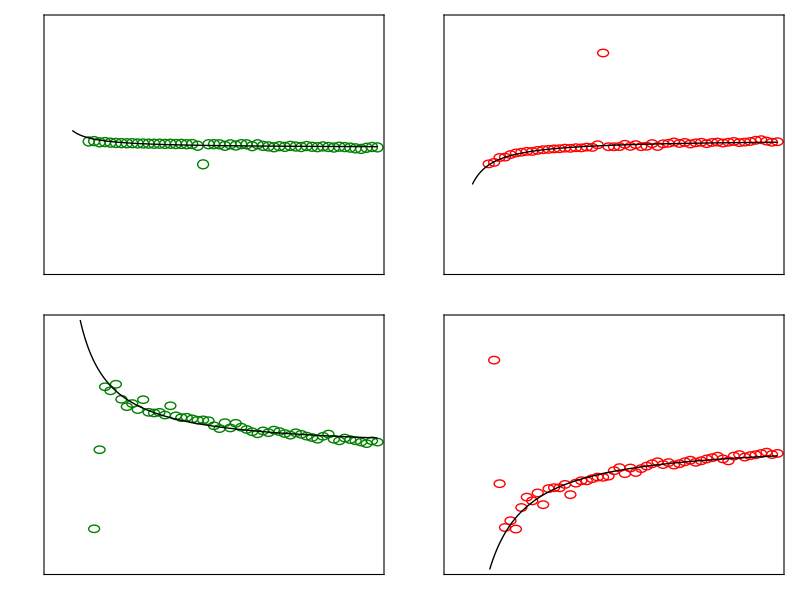

```mathematica
fig=Grid[{{p2,p1},{p4,p3}}]
```

```mathematica
path=FileNameJoin[{parentDir,"test"}];
fname="Figure_S7";
Export[FileNameJoin[{path,fname<>".png"}],fig,ImageResolution-> 300];
```

[Supplementary Figure 8]:Comparing Kataura-type plots in different models (15/06/2019)

Functions: EiiWei2016, EiiAraujo2007, EiiLiu2012

```mathematica
Clear[EiiWei2016];
EiiWei2016[p_,n_,m_]:=Catch[Module[
{
(*
X.Wei,T.Tanaka,Y.Yomogida,N.Sato,R.Saito,and H.Kataura,Nat.Commun.7,12899 (2016). See Supplementary Fig. 12 caption.
*)
ind,β,
d=0.142√(3(n^2+m^2+n m))/π (* nm *),
θ=ArcTan[(√3 m)/(2 n+m)],
a,b,c
},
EiiWei2016::pval="The value `1` is not allowed for p parameter in a semiconducting nanotube";
(* for p=3 one can use p=1,2 or p=4,5 parameters this results in slightly different curves. The former is close to the Araujo2007 results while the later deviates from Araujo2007 curve. I have tried both. *)
If[p>3,
a=1.079 (* eV*nm *);
b=0.668;
c=1.467 (* nm^-1 *),
a=0.970 (* eV*nm *);
b=0.497;
c=1.154 (* nm^-1 *)
];
ind=Mod[n-m,3];
If[
ind≠0,
β={{-0.07,0.05},{-0.19,0.17},{"x","x"},{-0.28,0.42},{-0.40,0.42}}⟦p,ind⟧(* eV*nm^2 *);
If[β==="x",Throw[Message[EiiWei2016::pval,p]]]
,
β=0
];
a p/d(1+b Log10[(c d)/p])+(β Cos[3 θ])/d^2 
](* end Module *)](* end Catch *)



Clear[EiiAraujo2007];
EiiAraujo2007[p_,n_,m_]:=Catch[Module[
{
(*
P.T.Araujo,S.K.Doorn,S.Kilina,S.Tretiak,E.Einarsson,S.Maruyama,H.Chacham,M.A.Pimenta,and A.Jorio,Phys.Rev.Lett.98,1 (2007). See Fig. 1 caption.
*)
ind,β,
a=1.049 (* eV*nm *),
b=0.456,
c=0.812 (* nm^-1 *),
d=0.142√(3(n^2+m^2+n m))/π (* nm *),
θ=ArcTan[(√3 m)/(2 n+m)]
},

EiiAraujo2007::pval="The value `1` is not allowed for p parameter in a semiconducting nanotube";
ind=Mod[n-m,3];
If[
ind≠0,
β={{-0.07,0.05},{-0.19,0.14},{"x","x"},{-0.42,0.42},{-0.4,0.4}}⟦p,ind⟧(* eV*nm^2 *);
If[β==="x",Throw[Message[EiiAraujo2007::pval,p]]],
β=-0.19(* two transitions exist for metallic tubes, the parameter, however, is given for only one. In armchair tubes these two transitions have the same energy, so the absence of the second value does not affect our plots for armchair tubes. Moreover, cos3θ=3 so the actual value of β is of no importance for armchair tubes. *)];
a p/d(1+b Log10[(c d)/p])+(β Cos[3 θ])/d^2 
](* end Module *)](* end Catch *)



Clear[EiiLiu2012];
(* Interpolation formula given by Eq. (1) in K.Liu,J.Deslippe,F.Xiao,R.B.Capaz,X.Hong,S.Aloni,A.Zettl,W.Wang,X.Bai,S.G.Louie,E.Wang,and F.Wang,Nat.Nanotechnol.7,325 (2012).*)
EiiLiu2012[p_,n_,m_]:=Catch[
Module[
{
type,i,
α,
ℏ=(6.63 10^-34)/(2 π 1.6 10^-19) (* eV*s *),
k=1/3 (2 π p)/(√3 0.142 √(n^2+m^2+n m))(* nm^-1 *),
θ=ArcTan[(√3 m)/(2 n+m)],
vF=(1.277-0.267/p) 10^15 (* nm/s *),
β=-0.173 (* eV*nm^2 *),
η=(50+180/p^2) 10^-3(* eV*nm^2 *)
},

EiiLiu2012::pvalsem="The value `1` is not allowed for p parameter in a semiconducting nanotube";
EiiLiu2012::pvalmet="The value `1` is not allowed for p parameter in a metallic nanotube";

type=Mod[n-m,3];
Switch[type,
1,If[Mod[p,3]==0,Throw[Message[EiiLiu2012::pvalsem,p]]];
i=p-Floor[p/3];
α=θ+i π; 
2 ℏ vF k+β k^2+η k^2 Cos[3 α],
2,If[Mod[p,3]==0,Throw[Message[EiiLiu2012::pvalsem,p]]];
α=θ+(i+1) π;
2 ℏ vF k+β k^2+η k^2 Cos[3 α],
0,If[Mod[p,3]≠0,Throw[Message[EiiLiu2012::pvalmet,p]]];
{2 ℏ vF k+β k^2+η k^2 Cos[3 θ],2 ℏ vF k+β k^2+η k^2 Cos[3 (θ+π)]}
]

](* end Module *)](* end Catch *)
```

[Supplementary Figure 8a, p1]: Kataura plots tubes vs ribbons Partoens2006

```mathematica
Clear[ZGNRpeakPartoens2006];
ZGNRpeakPartoens2006[chiralindex_,tubepeak_]:=Module[
{
ξa=0.28,
ζa=0.99,
ξb=-1.45,
ζb=0.04
},
{chiralindex-1,(ξa/chiralindex+ζa) tubepeak+(ξb/chiralindex+ζb)}
](* end Module *)
```

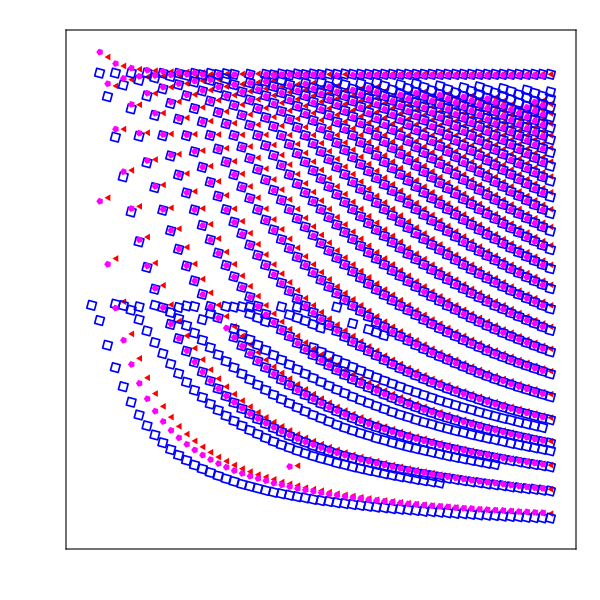

```mathematica
ts=MaTeX[#,FontSize->26]&;
tss=MaTeX[#,FontSize->30]&;
imagesize=600;


(* Kataura plot points *)
(* tube *)
path=FileNameJoin[{parentDir,"raw data","TB","armchair tubes"}];
fname="25_May_2019_data_TB_Partoens2006_Kataura_plot_ACNT";
Get[fname,Path->path];

(* ribbon *)
path=FileNameJoin[{parentDir,"raw data","TB","zigzag ribbons"}];
fname="25_May_2019_data_TB_Partoens2006_Kataura_plot_ZGNR";
Get[fname,Path->path];


katauraplotrProjected=ZGNRpeakPartoens2006[#⟦1⟧,#⟦2⟧]&/@katauraplottPartoens2006;


pstyle={Red,Blue,Magenta,Darker[Green,0.5]};
pfun=Polygon[CirclePoints[{1,π/3 #},If[#==4,36,#+2]]]&;
plotmarkers=Table[{Graphics[{If[i==2||i==4,{EdgeForm[Directive[AbsoluteThickness[1.2],Opacity[1],pstyle⟦i⟧]],FaceForm[None],pfun[i]},{pstyle⟦i⟧,pfun[i]}]}],If[i==2||i==4,10,7]},{i,4}];



ticklen={0.02,0};
xticks={#⟦1⟧,ts[#⟦2⟧],#⟦3⟧,#⟦4⟧}&/@LinTicks[0,60,20,4,MajorTickLength->ticklen,MinorTickLength->ticklen/1.7];
yticks={#⟦1⟧,ts[#⟦2⟧],#⟦3⟧,#⟦4⟧}&/@LinTicks[0,7,1,5,MajorTickLength->ticklen,MinorTickLength->ticklen/1.7];




fig=ListPlot[{katauraplottPartoens2006,katauraplotrPartoens2006,katauraplotrProjected},PlotRange->{{0,62},{0,6.7}},PlotStyle->pstyle,PlotMarkers->plotmarkers,
PlotLegends->Placed[PointLegend[pstyle,MaTeX["\\text{"<>#<>"}",FontSize->20]&/@{"tube Partoens2006 TBM","ribbon Partoens2006 TBM","ribbon by mapping"},LegendMarkerSize->15,Background->White],{Right,Top}],
AspectRatio->1,
PlotLabel->ts["\\text{Armchair SWCNTs vs ZGNRs}"],
GridLines->Automatic,
Axes->False,
Frame->True,
FrameLabel->ts/@{"n (\\text{or } w) \\text{, diameter (or width) index}","\\hbar \\omega \\text{, eV}"},
FrameStyle->Directive[AbsoluteThickness[1]],
FrameTicks->{{yticks,{#⟦1⟧,"",#⟦3⟧,#⟦4⟧}&/@yticks},{xticks,{#⟦1⟧,"",#⟦3⟧,#⟦4⟧}&/@xticks}},
FrameTicksStyle->Directive[{AbsoluteThickness[1],FontSize->15}],
Epilog->{
{(*EdgeForm[Black],*)FaceForm[White],Disk[{5,0.5},{2,0.25}]},
Inset[tss["\\text{(a)}"],Scaled[{0.08,0.075}],Scaled[{0.5,0.5}]]
},
AspectRatio->1,
ImageSize->imagesize
]
p1=fig;
```

```mathematica
SystemOpen[path]
```

```mathematica
path=FileNameJoin[{parentDir,"test"}];
fname="Figure_S8a";
Export[FileNameJoin[{path,fname<>".png"}],fig,ImageResolution-> 300];
```

[Supplementary Figure 8b, p2]: Kataura plots tubes Reich2003 vs ribbons 19May2019MyFit

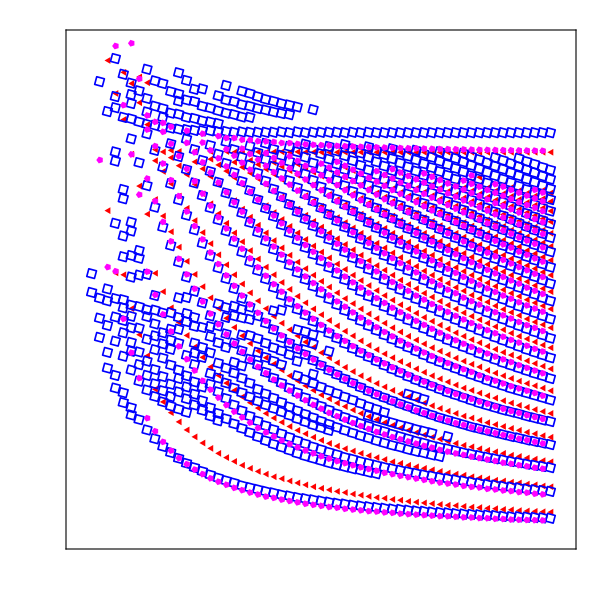

```mathematica
ts=MaTeX[#,FontSize->26]&;
tss=MaTeX[#,FontSize->30]&;
imagesize=600;

(* Kataura plot points *)
(* tube *)
path=FileNameJoin[{parentDir,"raw data","TB","armchair tubes"}];
fname="25_May_2019_data_TB_Reich2002_Kataura_plot_ACNT";
Get[fname,Path->path];

(* ribbon *)
path=FileNameJoin[{parentDir,"raw data","TB","zigzag ribbons"}];
fname="25_May_2019_data_TB_19May2019MyFit_Kataura_plot_ZGNR";
Get[fname,Path->path];



katauraplotrProjected=ZGNRpeakFitted[#⟦1⟧,#⟦2⟧]&/@katauraplottReich2002;

pstyle={Red,Blue,Magenta,Darker[Green,0.5]};
pfun=Polygon[CirclePoints[{1,π/3 #},If[#==4,36,#+2]]]&;
plotmarkers=Table[{Graphics[{
If[i==2||i==4,{EdgeForm[Directive[AbsoluteThickness[1.2],Opacity[1],pstyle⟦i⟧]],FaceForm[None],pfun[i]},{pstyle⟦i⟧,pfun[i]}]}],If[i==2||i==4,10,7]},{i,4}];



ticklen={0.02,0};
xticks={#⟦1⟧,ts[#⟦2⟧],#⟦3⟧,#⟦4⟧}&/@LinTicks[0,60,20,4,MajorTickLength->ticklen,MinorTickLength->ticklen/1.7];
yticks={#⟦1⟧,ts[#⟦2⟧],#⟦3⟧,#⟦4⟧}&/@LinTicks[0,5,1,5,MajorTickLength->ticklen,MinorTickLength->ticklen/1.7];




fig=ListPlot[{katauraplottReich2002,katauraplotr19May2019MyFit,katauraplotrProjected},PlotRange->{{0,62},{0,5.2}},PlotStyle->pstyle,PlotMarkers->plotmarkers,
PlotLegends->Placed[PointLegend[pstyle,MaTeX["\\text{"<>#<>"}",FontSize->20]&/@{"Reich2002 TBM","ZGNRs(av.)","ribbon by mapping"},LegendMarkerSize->15,Background->White],{Right,Top}],
AspectRatio->1,
PlotLabel->ts["\\text{Armchair SWCNTs vs ZGNRs}"],
GridLines->Automatic,
Axes->False,
Frame->True,
FrameLabel->ts/@{"n (\\text{or } w) \\text{, diameter (or width) index}","\\hbar \\omega \\text{, eV}"},
FrameStyle->Directive[AbsoluteThickness[1]],
FrameTicks->{{yticks,{#⟦1⟧,"",#⟦3⟧,#⟦4⟧}&/@yticks},{xticks,{#⟦1⟧,"",#⟦3⟧,#⟦4⟧}&/@xticks}},
FrameTicksStyle->Directive[{AbsoluteThickness[1],FontSize->15}],
Epilog->{
{(*EdgeForm[Black],*)FaceForm[White],Disk[{5,0.5},{2,0.25}]},
Inset[tss["\\text{(b)}"],Scaled[{0.08,0.075}],Scaled[{0.5,0.5}]]
},
AspectRatio->1,
ImageSize->imagesize
]
p2=fig;
```

```mathematica
SystemOpen[path]
```

```mathematica
path=FileNameJoin[{parentDir,"test"}];
fname="Figure_S8b";
Export[FileNameJoin[{path,fname<>".png"}],fig,ImageResolution-> 600];
```

[Supplementary Figure 8c, p3]: Kataura plots Reich2003 vs Araujo2007, Wei2016 and Liu2012

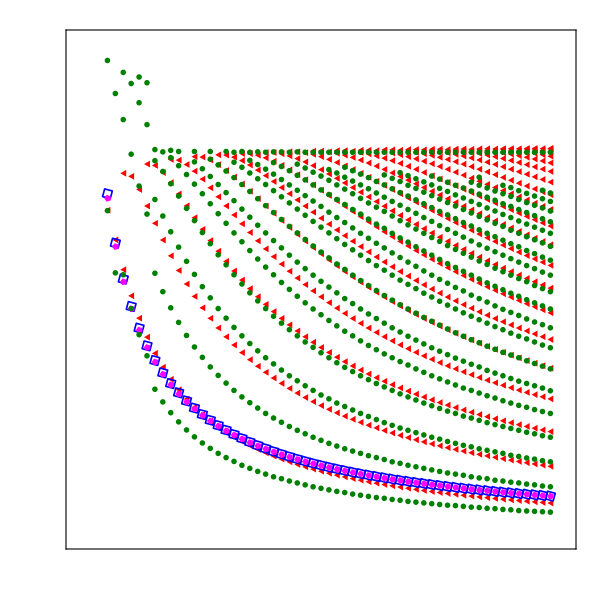

```mathematica
ts=MaTeX[#,FontSize->26]&;
imagesize=600;

(* Kataura plot Reich2002 TBM *)
path=FileNameJoin[{parentDir,"raw data","TB","armchair tubes"}];
fname="25_May_2019_data_TB_Reich2002_Kataura_plot_ACNT";
Get[fname,Path->path];

(* Kataura plots from interpolating formulas *)
katauraplottAraujo2007=Flatten[Table[{n,EiiAraujo2007[p,n,n]},{n,4,60},{p,{3}}],1];
katauraplottWei2016=Flatten[Table[{n,EiiWei2016[p,n,n]},{n,4,60},{p,{3}}],1];
katauraplottLiu2012=Flatten[Table[{n,EiiLiu2012[3 p,n,n]⟦1⟧},{n,4,60},{p,1,n/3}],1];

pstyle={Red,Blue,Magenta,Darker[Green,0.5]};
pfun=Polygon[CirclePoints[{1,π/3 #},If[#==4,36,#+2]]]&;
plotmarkers=Table[{Graphics[{If[i==2||i==4,{EdgeForm[Directive[AbsoluteThickness[1.2],Opacity[1],pstyle⟦i⟧]],FaceForm[None],pfun[i]},{pstyle⟦i⟧,pfun[i]}]}],If[i==2||i==4,10,7]},{i,4}];



ticklen={0.02,0};
xticks={#⟦1⟧,ts[#⟦2⟧],#⟦3⟧,#⟦4⟧}&/@LinTicks[0,60,20,4,MajorTickLength->ticklen,MinorTickLength->ticklen/1.7];
yticks={#⟦1⟧,ts[#⟦2⟧],#⟦3⟧,#⟦4⟧}&/@LinTicks[0,5,1,5,MajorTickLength->ticklen,MinorTickLength->ticklen/1.7];




fig=ListPlot[{katauraplottLiu2012,katauraplottAraujo2007,katauraplottWei2016,katauraplottReich2002},PlotRange->{{0,62},{0,5.2}},PlotStyle->pstyle,PlotMarkers->plotmarkers,
PlotLegends->Placed[PointLegend[pstyle,MaTeX["\\text{"<>#<>"}",FontSize->20]&/@{"Liu2012","Araujo2007","Wei2016","Reich2002 TBM"},LegendMarkerSize->15,Background->White],{Right,Top}],
AspectRatio->1,
PlotLabel->ts["\\text{Armchair SWCNTs}"],
GridLines->Automatic,
Axes->False,
Frame->True,
FrameLabel->ts/@{"n \\text{, diameter index}","\\hbar \\omega \\text{, eV}"},
FrameStyle->Directive[AbsoluteThickness[1]],
FrameTicks->{{yticks,{#⟦1⟧,"",#⟦3⟧,#⟦4⟧}&/@yticks},{xticks,{#⟦1⟧,"",#⟦3⟧,#⟦4⟧}&/@xticks}},
FrameTicksStyle->Directive[{AbsoluteThickness[1],FontSize->15}],
Epilog->{
{(*EdgeForm[Black],*)FaceForm[White],Disk[{5,0.5},{2,0.25}]},
Inset[tss["\\text{(c)}"],Scaled[{0.08,0.075}],Scaled[{0.5,0.5}]]
},
AspectRatio->1,
ImageSize->imagesize
]
p3=fig;
```

```mathematica
SystemOpen[path]
```

```mathematica
path=FileNameJoin[{parentDir,"test"}];
fname="Figure_S8c";
Export[FileNameJoin[{path,fname<>".png"}],fig,ImageResolution-> 600];
```

[Supplementary Figure 8d, p4]: Kataura plots Saroka2017 vs Liu2012

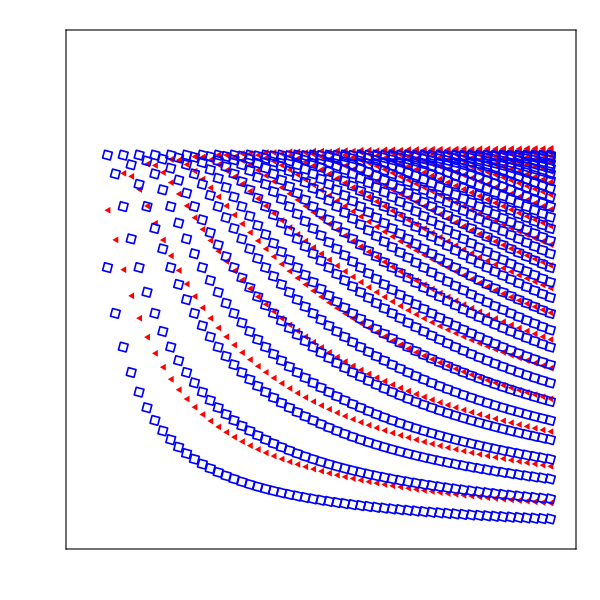

```mathematica
ts=MaTeX[#,FontSize->26]&;
imagesize=600;
(* Kataura plots *)
katauraplottLiu2012=Flatten[Table[{n,EiiLiu2012[3 p,n,n]⟦1⟧},{n,4,60},{p,1,n/3}],1];
katauraplottSaroka2017=Flatten[Table[{n,2 2 Sin[(π p)/n]},{n,4,60},{p,1,n/2}],1];

pstyle={Red,Blue,Magenta,Darker[Green,0.5]};
pfun=Polygon[CirclePoints[{1,π/3 #},If[#==4,36,#+2]]]&;
plotmarkers=Table[{Graphics[{If[i==2||i==4,{EdgeForm[Directive[AbsoluteThickness[1.2],Opacity[1],pstyle⟦i⟧]],FaceForm[None],pfun[i]},{pstyle⟦i⟧,pfun[i]}]}],If[i==2||i==4,10,7]},{i,4}];



ticklen={0.02,0};
xticks={#⟦1⟧,ts[#⟦2⟧],#⟦3⟧,#⟦4⟧}&/@LinTicks[0,60,20,4,MajorTickLength->ticklen,MinorTickLength->ticklen/1.7];
yticks={#⟦1⟧,ts[#⟦2⟧],#⟦3⟧,#⟦4⟧}&/@LinTicks[0,5,1,5,MajorTickLength->ticklen,MinorTickLength->ticklen/1.7];


f1=MaTeX["\\text{"<>#<>"}",FontSize->20]&;
f2=MaTeX[#,FontSize->20]&;

fig=ListPlot[{katauraplottLiu2012,katauraplottSaroka2017},PlotRange->{{0,62},{0,5.2}},PlotStyle->pstyle,PlotMarkers->plotmarkers,
PlotLegends->Placed[PointLegend[pstyle,{f1@"Liu2012",f2@"4 \\sin \\left[\\dfrac{\\pi p}{n}\\right]"},LegendMarkerSize->15,Background->White],{Right,Top}],
AspectRatio->1,
PlotLabel->ts["\\text{Armchair SWCNTs}"],
GridLines->Automatic,
Axes->False,
Frame->True,
FrameLabel->ts/@{"n \\text{, diameter index}","\\hbar \\omega \\text{, eV}"},
FrameStyle->Directive[AbsoluteThickness[1]],
FrameTicks->{{yticks,{#⟦1⟧,"",#⟦3⟧,#⟦4⟧}&/@yticks},{xticks,{#⟦1⟧,"",#⟦3⟧,#⟦4⟧}&/@xticks}},
FrameTicksStyle->Directive[{AbsoluteThickness[1],FontSize->15}],
Epilog->{
{(*EdgeForm[Black],*)FaceForm[White],Disk[{5,0.5},{2,0.25}]},
Inset[tss["\\text{(d)}"],Scaled[{0.08,0.075}],Scaled[{0.5,0.5}]]
},
AspectRatio->1,
ImageSize->imagesize
]
p4=fig;
```

```mathematica
SystemOpen[path]
```

```mathematica
path=FileNameJoin[{parentDir,"test"}];
fname="Figure_S8d";
Export[FileNameJoin[{path,fname<>".png"}],fig,ImageResolution-> 600];
```

[Supplementary Figure 8, p1,p2,p3,p4]: Kataura plots: Summary

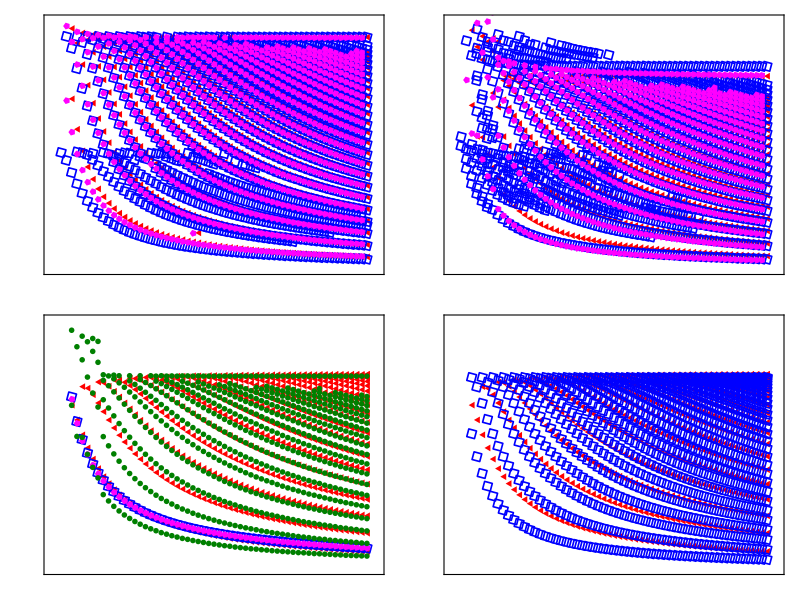

```mathematica
figg=Grid[{{p1,p2},{p3,p4}}]
```

```mathematica
path=FileNameJoin[{parentDir,"test"}];
fname="Figure_S8";
Export[FileNameJoin[{path,fname<>".pdf"}],figg,ImageResolution-> 600];
```

[Figure 5]:An atlas of ZGNRs optical resonances vs Kataura plots and Jiang2008 approach (02/06/2019)

```mathematica
Clear[ZGNRpeakFitted];
ZGNRpeakFitted[chiralindex_,tubepeak_]:=Module[
{
ξa=2.83,
ζa=0.98,
ξb=-7.42,
ζb=0.03(* 26/06/2019: 0.04 *)

},
{chiralindex-1,(ξa/chiralindex+ζa) tubepeak+(ξb/chiralindex+ζb)}
](* end Module *)
```

```mathematica
Clear[EiiZGNRJiang2008];
EiiZGNRJiang2008[W_,i_]:=Module[
{
c1={5.38,9.49,13.51,17.80},
c2={-2.83,-7.96,-15.51,-26,91},
c3={0.63,2.61,6.92,15.85}
},
c1⟦i⟧/W+c2⟦i⟧/W^2+c3⟦i⟧/W^3 
](* end Module *)
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

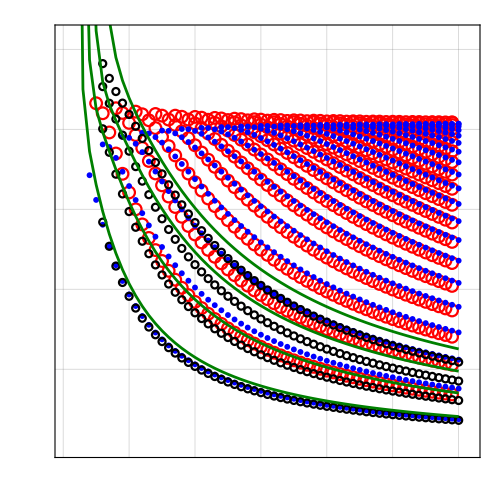
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics-

```mathematica
ts=MaTeX[#,FontSize->26]&;
tss=MaTeX[#,FontSize->30]&;
imagesize=600;

katauraplott1=Flatten[Table[{n,EiiLiu2012[3 p,n,n]⟦1⟧},{n,4,60},{p,2,n/3}],1];
katauraplott2=Flatten[Table[{n,EiiLiu2012[3 p,n,n]⟦1⟧},{n,4,60},{p,n/3}],1];

ZGNRKatauraPlotProjected=ZGNRpeakFitted[#⟦1⟧,#⟦2⟧]&/@katauraplott1;


ticklen={0.02,0};
xticks={#⟦1⟧,ts[#⟦2⟧],#⟦3⟧,#⟦4⟧}&/@LinTicks[0,60,20,4,MajorTickLength->ticklen,MinorTickLength->ticklen/1.7];
yticks={#⟦1⟧,ts[#⟦2⟧],#⟦3⟧,#⟦4⟧}&/@LinTicks[0,5,1,5,MajorTickLength->ticklen,MinorTickLength->ticklen/1.7];

plotstyle={Red,Blue,Black};
sz=10;
ims=15;
legend=Grid[{
{
Graphics[{plotstyle⟦1⟧,Circle[{0,0},sz]},ImageSize->ims],
MaTeX["\\text{ZGNR atlas}",FontSize->20]
},
{
Graphics[{plotstyle⟦2⟧,Disk[{0,0},sz/4]},ImageSize->ims/1.4],
MaTeX["\\text{Liu et al.}",FontSize->20]
},
{
Graphics[{Darker[Green,0.5],AbsoluteThickness[3],Line[{{0,0},{sz,0}}]},ImageSize->1.5 ims],MaTeX["\\text{Jiang et al.}",FontSize->20]
},
{
Graphics[{Black,AbsoluteThickness[1],Circle[{0,0},sz]},ImageSize->0.7 ims],MaTeX["\\text{van Hove sym.}",FontSize->20]
}
}ᵀ,Frame->False]

path=FileNameJoin[{parentDir,"raw data","TB","zigzag ribbons","2019_06_28_My_averaged_fit_Jiang2008_approach"}];
fname="28_Jun_2019_ZGNR_bulk_van_Hove_singularities_TB";
Get[fname,Path->path];

a=0.246;(* nm *)
 
Jiang2008lines=Table[{w,EiiZGNRJiang2008[(3 w-2)/(2 √3) a ,i]},{i,4},{w,2,60}];


fig=Column[{legend,ListPlot[{ZGNRKatauraPlotProjected,katauraplott2,ZGNRBulkVanHoveSingularitesDifferences},
PlotRange->{{0,62},{0,5.2}},
PlotStyle->plotstyle,
PlotMarkers->{{Graphics[{Circle[{0,0},1]}],12},{Graphics[{Disk[{0,0},1]}],6},{Graphics[{Circle[{0,0},1]}],7.2}},
Axes->False,
Frame->True,
FrameLabel->ts/@{"n (\\text{or } w) \\text{, diameter (or width) index}","\\hbar \\omega \\text{, eV}"},
FrameStyle->Directive[AbsoluteThickness[1]],
FrameTicks->{{yticks,{#⟦1⟧,"",#⟦3⟧,#⟦4⟧}&/@yticks},{xticks,{#⟦1⟧,"",#⟦3⟧,#⟦4⟧}&/@xticks}},
FrameTicksStyle->Directive[{AbsoluteThickness[1],FontSize->15}],

GridLines->{Range[0,60,10],Range[5]},
Epilog->{{Darker[Green,0.5],AbsoluteThickness[2],Line[Jiang2008lines]}},
AspectRatio->1,
ImageSize->500]},Alignment->{Right,0},Frame->False]
```

```mathematica
SystemOpen[path]
```

```mathematica
path=FileNameJoin[{parentDir,"test"}];
fname="Figure_5";
Export[FileNameJoin[{path,fname<>".png"}],fig,ImageResolution-> 300];
```